## Part b : Regression

```mathematica
(*originalData = Import["C:\\Users\\joshu\\Desktop\\archive\\train.csv"];*)
originalData = Import["C:\\Users\\dylan\\Downloads\\archive\\train.csv"];


Print["Sample: ",MatrixForm[Take[originalData,10]],Length[originalData]-1];
```

Sample: (Id | MSSubClass | MSZoning | LotFrontage | LotArea | Street | Alley | LotShape | LandContour | Utilities | LotConfig | LandSlope | Neighborhood | Condition1 | Condition2 | BldgType | HouseStyle | OverallQual | OverallCond | YearBuilt | YearRemodAdd | RoofStyle | RoofMatl | Exterior1st | Exterior2nd | MasVnrType | MasVnrArea | ExterQual | ExterCond | Foundation | BsmtQual | BsmtCond | BsmtExposure | BsmtFinType1 | BsmtFinSF1 | BsmtFinType2 | BsmtFinSF2 | BsmtUnfSF | TotalBsmtSF | Heating | HeatingQC | CentralAir | Electrical | 1stFlrSF | 2ndFlrSF | LowQualFinSF | GrLivArea | BsmtFullBath | BsmtHalfBath | FullBath | HalfBath | BedroomAbvGr | KitchenAbvGr | KitchenQual | TotRmsAbvGrd | Functional | Fireplaces | FireplaceQu | GarageType | GarageYrBlt | GarageFinish | GarageCars | GarageArea | GarageQual | GarageCond | PavedDrive | WoodDeckSF | OpenPorchSF | EnclosedPorch | 3SsnPorch | ScreenPorch | PoolArea | PoolQC | Fence | MiscFeature | MiscVal | MoSold | YrSold | SaleType | SaleCondition | SalePrice
1 | 60 | RL | 65 | 8450 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | Inside | Gtl | CollgCr | Norm | Norm | 1Fam | 2Story | 7 | 5 | 2003 | 2003 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 196 | Gd | TA | PConc | Gd | TA | No | GLQ | 706 | Unf | 0 | 150 | 856 | GasA | Ex | Y | SBrkr | 856 | 854 | 0 | 1710 | 1 | 0 | 2 | 1 | 3 | 1 | Gd | 8 | Typ | 0 | Missing[NotAvailable] | Attchd | 2003 | RFn | 2 | 548 | TA | TA | Y | 0 | 61 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 2 | 2008 | WD | Normal | 208500
2 | 20 | RL | 80 | 9600 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | FR2 | Gtl | Veenker | Feedr | Norm | 1Fam | 1Story | 6 | 8 | 1976 | 1976 | Gable | CompShg | MetalSd | MetalSd | None | 0 | TA | TA | CBlock | Gd | TA | Gd | ALQ | 978 | Unf | 0 | 284 | 1262 | GasA | Ex | Y | SBrkr | 1262 | 0 | 0 | 1262 | 0 | 1 | 2 | 0 | 3 | 1 | TA | 6 | Typ | 1 | TA | Attchd | 1976 | RFn | 2 | 460 | TA | TA | Y | 298 | 0 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 5 | 2007 | WD | Normal | 181500
3 | 60 | RL | 68 | 11250 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | Inside | Gtl | CollgCr | Norm | Norm | 1Fam | 2Story | 7 | 5 | 2001 | 2002 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 162 | Gd | TA | PConc | Gd | TA | Mn | GLQ | 486 | Unf | 0 | 434 | 920 | GasA | Ex | Y | SBrkr | 920 | 866 | 0 | 1786 | 1 | 0 | 2 | 1 | 3 | 1 | Gd | 6 | Typ | 1 | TA | Attchd | 2001 | RFn | 2 | 608 | TA | TA | Y | 0 | 42 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 9 | 2008 | WD | Normal | 223500
4 | 70 | RL | 60 | 9550 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | Corner | Gtl | Crawfor | Norm | Norm | 1Fam | 2Story | 7 | 5 | 1915 | 1970 | Gable | CompShg | Wd Sdng | Wd Shng | None | 0 | TA | TA | BrkTil | TA | Gd | No | ALQ | 216 | Unf | 0 | 540 | 756 | GasA | Gd | Y | SBrkr | 961 | 756 | 0 | 1717 | 1 | 0 | 1 | 0 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Detchd | 1998 | Unf | 3 | 642 | TA | TA | Y | 0 | 35 | 272 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 2 | 2006 | WD | Abnorml | 140000
5 | 60 | RL | 84 | 14260 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | FR2 | Gtl | NoRidge | Norm | Norm | 1Fam | 2Story | 8 | 5 | 2000 | 2000 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 350 | Gd | TA | PConc | Gd | TA | Av | GLQ | 655 | Unf | 0 | 490 | 1145 | GasA | Ex | Y | SBrkr | 1145 | 1053 | 0 | 2198 | 1 | 0 | 2 | 1 | 4 | 1 | Gd | 9 | Typ | 1 | TA | Attchd | 2000 | RFn | 3 | 836 | TA | TA | Y | 192 | 84 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 12 | 2008 | WD | Normal | 250000
6 | 50 | RL | 85 | 14115 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | Inside | Gtl | Mitchel | Norm | Norm | 1Fam | 1.5Fin | 5 | 5 | 1993 | 1995 | Gable | CompShg | VinylSd | VinylSd | None | 0 | TA | TA | Wood | Gd | TA | No | GLQ | 732 | Unf | 0 | 64 | 796 | GasA | Ex | Y | SBrkr | 796 | 566 | 0 | 1362 | 1 | 0 | 1 | 1 | 1 | 1 | TA | 5 | Typ | 0 | Missing[NotAvailable] | Attchd | 1993 | Unf | 2 | 480 | TA | TA | Y | 40 | 30 | 0 | 320 | 0 | 0 | Missing[NotAvailable] | MnPrv | Shed | 700 | 10 | 2009 | WD | Normal | 143000
7 | 20 | RL | 75 | 10084 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | Inside | Gtl | Somerst | Norm | Norm | 1Fam | 1Story | 8 | 5 | 2004 | 2005 | Gable | CompShg | VinylSd | VinylSd | Stone | 186 | Gd | TA | PConc | Ex | TA | Av | GLQ | 1369 | Unf | 0 | 317 | 1686 | GasA | Ex | Y | SBrkr | 1694 | 0 | 0 | 1694 | 1 | 0 | 2 | 0 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Attchd | 2004 | RFn | 2 | 636 | TA | TA | Y | 255 | 57 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 8 | 2007 | WD | Normal | 307000
8 | 60 | RL | Missing[NotAvailable] | 10382 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | Corner | Gtl | NWAmes | PosN | Norm | 1Fam | 2Story | 7 | 6 | 1973 | 1973 | Gable | CompShg | HdBoard | HdBoard | Stone | 240 | TA | TA | CBlock | Gd | TA | Mn | ALQ | 859 | BLQ | 32 | 216 | 1107 | GasA | Ex | Y | SBrkr | 1107 | 983 | 0 | 2090 | 1 | 0 | 2 | 1 | 3 | 1 | TA | 7 | Typ | 2 | TA | Attchd | 1973 | RFn | 2 | 484 | TA | TA | Y | 235 | 204 | 228 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Shed | 350 | 11 | 2009 | WD | Normal | 200000
9 | 50 | RM | 51 | 6120 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | Inside | Gtl | OldTown | Artery | Norm | 1Fam | 1.5Fin | 7 | 5 | 1931 | 1950 | Gable | CompShg | BrkFace | Wd Shng | None | 0 | TA | TA | BrkTil | TA | TA | No | Unf | 0 | Unf | 0 | 952 | 952 | GasA | Gd | Y | FuseF | 1022 | 752 | 0 | 1774 | 0 | 0 | 2 | 0 | 2 | 2 | TA | 8 | Min1 | 2 | TA | Detchd | 1931 | Unf | 2 | 468 | Fa | TA | Y | 90 | 0 | 205 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 4 | 2008 | WD | Abnorml | 129900)1460

## Feature Extraction and Generation

```mathematica
ClearAll[x,y,m,n,ny,y,xNames,xLabels,yNames,yLabels];

safeNum[val_] := If[NumberQ[val], val, 0];

encodeQual[val_]:=Lookup[<|"Ex"->5,"Gd"->4,"TA"->3,"Fa"->2,"Po"->1,"NA"->0|>,ToString[val],0];

x = {1,#[[2]],#[[4]],#[[5]],#[[18]],#[[19]],#[[20]],#[[21]],#[[27]],#[[35]],#[[37]],#[[38]],

(*Ordinal Quality Columns:ExterQual (#28),BsmtQual (#31),HeatingQC (#41),KitchenQual (#54),GarageQual (#64)*)encodeQual[#[[28]]],encodeQual[#[[31]]],encodeQual[#[[41]]],encodeQual[#[[54]]],encodeQual[#[[64]]],

(*TotalSF=TotalBsmtSF (#39)+1stFlrSF (#44)+2ndFlrSF (#45)*)
safeNum[#[[39]]]+safeNum[#[[44]]]+safeNum[#[[45]]],

#[[46]],

(*TotalBathrooms=FullBath (#50)+0.5*HalfBath (#51)+BsmtFullBath (#48)+0.5*BsmtHalfBath (#49)*)
safeNum[#[[50]]]+0.5*safeNum[#[[51]]]+safeNum[#[[48]]]+0.5*safeNum[#[[49]]],

#[[52]],#[[53]],#[[55]],#[[57]],#[[60]],#[[62]],#[[63]],#[[67]],#[[68]],#[[69]],#[[70]],#[[71]],#[[72]],#[[76]],#[[77]],#[[78]]}& /@  Drop[originalData,1];
y = {#[[81]]}      & /@  Drop[originalData,1];

m = Length[x];
n = Length[x[[1]]]-1;
ny = Length[y[[1]]];

replaceNAWithMean[colData_]:=Module[{meanNumber,numericData},numericData=Select[colData,NumberQ[#]&];
If[Length[numericData]==0,colData,meanNumber=1.0 Mean[numericData];
Map[If[#==="NA",meanNumber,#]&,colData]]];

cleanedX=Transpose[Map[replaceNAWithMean,Transpose[x]]];
x=cleanedX;

disp = Min[10,m];

Print["Sample: ",MatrixForm[Take[originalData,disp+1]],"   x: ",MatrixForm[Take[x,disp]],"   y: ",MatrixForm[Take[y,disp]]];

i=disp;

Print[Superscript["x","("<>ToString[i]<>")"]," = ", x[[i]]];
Print[Superscript["y","("<>ToString[i]<>")"]," = ", y[[i]]];
Print["

"];
xNames = Table[Subscript["x",ToString[i]],{i,0,n}];
xLabels = Table[Subsuperscript["x",ToString[j],"("<>ToString[i]<>")"],{i,1,m},{j,0,n}];
Print["xNames = ",xNames];
Print["x = ",MatrixForm[Prepend[Take[x,disp],xNames]]," = ",MatrixForm[Prepend[Take[xLabels,disp],xNames]]];
```

Sample: (Id | MSSubClass | MSZoning | LotFrontage | LotArea | Street | Alley | LotShape | LandContour | Utilities | LotConfig | LandSlope | Neighborhood | Condition1 | Condition2 | BldgType | HouseStyle | OverallQual | OverallCond | YearBuilt | YearRemodAdd | RoofStyle | RoofMatl | Exterior1st | Exterior2nd | MasVnrType | MasVnrArea | ExterQual | ExterCond | Foundation | BsmtQual | BsmtCond | BsmtExposure | BsmtFinType1 | BsmtFinSF1 | BsmtFinType2 | BsmtFinSF2 | BsmtUnfSF | TotalBsmtSF | Heating | HeatingQC | CentralAir | Electrical | 1stFlrSF | 2ndFlrSF | LowQualFinSF | GrLivArea | BsmtFullBath | BsmtHalfBath | FullBath | HalfBath | BedroomAbvGr | KitchenAbvGr | KitchenQual | TotRmsAbvGrd | Functional | Fireplaces | FireplaceQu | GarageType | GarageYrBlt | GarageFinish | GarageCars | GarageArea | GarageQual | GarageCond | PavedDrive | WoodDeckSF | OpenPorchSF | EnclosedPorch | 3SsnPorch | ScreenPorch | PoolArea | PoolQC | Fence | MiscFeature | MiscVal | MoSold | YrSold | SaleType | SaleCondition | SalePrice
1 | 60 | RL | 65 | 8450 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | Inside | Gtl | CollgCr | Norm | Norm | 1Fam | 2Story | 7 | 5 | 2003 | 2003 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 196 | Gd | TA | PConc | Gd | TA | No | GLQ | 706 | Unf | 0 | 150 | 856 | GasA | Ex | Y | SBrkr | 856 | 854 | 0 | 1710 | 1 | 0 | 2 | 1 | 3 | 1 | Gd | 8 | Typ | 0 | Missing[NotAvailable] | Attchd | 2003 | RFn | 2 | 548 | TA | TA | Y | 0 | 61 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 2 | 2008 | WD | Normal | 208500
2 | 20 | RL | 80 | 9600 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | FR2 | Gtl | Veenker | Feedr | Norm | 1Fam | 1Story | 6 | 8 | 1976 | 1976 | Gable | CompShg | MetalSd | MetalSd | None | 0 | TA | TA | CBlock | Gd | TA | Gd | ALQ | 978 | Unf | 0 | 284 | 1262 | GasA | Ex | Y | SBrkr | 1262 | 0 | 0 | 1262 | 0 | 1 | 2 | 0 | 3 | 1 | TA | 6 | Typ | 1 | TA | Attchd | 1976 | RFn | 2 | 460 | TA | TA | Y | 298 | 0 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 5 | 2007 | WD | Normal | 181500
3 | 60 | RL | 68 | 11250 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | Inside | Gtl | CollgCr | Norm | Norm | 1Fam | 2Story | 7 | 5 | 2001 | 2002 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 162 | Gd | TA | PConc | Gd | TA | Mn | GLQ | 486 | Unf | 0 | 434 | 920 | GasA | Ex | Y | SBrkr | 920 | 866 | 0 | 1786 | 1 | 0 | 2 | 1 | 3 | 1 | Gd | 6 | Typ | 1 | TA | Attchd | 2001 | RFn | 2 | 608 | TA | TA | Y | 0 | 42 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 9 | 2008 | WD | Normal | 223500
4 | 70 | RL | 60 | 9550 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | Corner | Gtl | Crawfor | Norm | Norm | 1Fam | 2Story | 7 | 5 | 1915 | 1970 | Gable | CompShg | Wd Sdng | Wd Shng | None | 0 | TA | TA | BrkTil | TA | Gd | No | ALQ | 216 | Unf | 0 | 540 | 756 | GasA | Gd | Y | SBrkr | 961 | 756 | 0 | 1717 | 1 | 0 | 1 | 0 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Detchd | 1998 | Unf | 3 | 642 | TA | TA | Y | 0 | 35 | 272 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 2 | 2006 | WD | Abnorml | 140000
5 | 60 | RL | 84 | 14260 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | FR2 | Gtl | NoRidge | Norm | Norm | 1Fam | 2Story | 8 | 5 | 2000 | 2000 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 350 | Gd | TA | PConc | Gd | TA | Av | GLQ | 655 | Unf | 0 | 490 | 1145 | GasA | Ex | Y | SBrkr | 1145 | 1053 | 0 | 2198 | 1 | 0 | 2 | 1 | 4 | 1 | Gd | 9 | Typ | 1 | TA | Attchd | 2000 | RFn | 3 | 836 | TA | TA | Y | 192 | 84 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 12 | 2008 | WD | Normal | 250000
6 | 50 | RL | 85 | 14115 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | Inside | Gtl | Mitchel | Norm | Norm | 1Fam | 1.5Fin | 5 | 5 | 1993 | 1995 | Gable | CompShg | VinylSd | VinylSd | None | 0 | TA | TA | Wood | Gd | TA | No | GLQ | 732 | Unf | 0 | 64 | 796 | GasA | Ex | Y | SBrkr | 796 | 566 | 0 | 1362 | 1 | 0 | 1 | 1 | 1 | 1 | TA | 5 | Typ | 0 | Missing[NotAvailable] | Attchd | 1993 | Unf | 2 | 480 | TA | TA | Y | 40 | 30 | 0 | 320 | 0 | 0 | Missing[NotAvailable] | MnPrv | Shed | 700 | 10 | 2009 | WD | Normal | 143000
7 | 20 | RL | 75 | 10084 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | Inside | Gtl | Somerst | Norm | Norm | 1Fam | 1Story | 8 | 5 | 2004 | 2005 | Gable | CompShg | VinylSd | VinylSd | Stone | 186 | Gd | TA | PConc | Ex | TA | Av | GLQ | 1369 | Unf | 0 | 317 | 1686 | GasA | Ex | Y | SBrkr | 1694 | 0 | 0 | 1694 | 1 | 0 | 2 | 0 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Attchd | 2004 | RFn | 2 | 636 | TA | TA | Y | 255 | 57 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 8 | 2007 | WD | Normal | 307000
8 | 60 | RL | Missing[NotAvailable] | 10382 | Pave | Missing[NotAvailable] | IR1 | Lvl | AllPub | Corner | Gtl | NWAmes | PosN | Norm | 1Fam | 2Story | 7 | 6 | 1973 | 1973 | Gable | CompShg | HdBoard | HdBoard | Stone | 240 | TA | TA | CBlock | Gd | TA | Mn | ALQ | 859 | BLQ | 32 | 216 | 1107 | GasA | Ex | Y | SBrkr | 1107 | 983 | 0 | 2090 | 1 | 0 | 2 | 1 | 3 | 1 | TA | 7 | Typ | 2 | TA | Attchd | 1973 | RFn | 2 | 484 | TA | TA | Y | 235 | 204 | 228 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Shed | 350 | 11 | 2009 | WD | Normal | 200000
9 | 50 | RM | 51 | 6120 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | Inside | Gtl | OldTown | Artery | Norm | 1Fam | 1.5Fin | 7 | 5 | 1931 | 1950 | Gable | CompShg | BrkFace | Wd Shng | None | 0 | TA | TA | BrkTil | TA | TA | No | Unf | 0 | Unf | 0 | 952 | 952 | GasA | Gd | Y | FuseF | 1022 | 752 | 0 | 1774 | 0 | 0 | 2 | 0 | 2 | 2 | TA | 8 | Min1 | 2 | TA | Detchd | 1931 | Unf | 2 | 468 | Fa | TA | Y | 90 | 0 | 205 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 4 | 2008 | WD | Abnorml | 129900
10 | 190 | RL | 50 | 7420 | Pave | Missing[NotAvailable] | Reg | Lvl | AllPub | Corner | Gtl | BrkSide | Artery | Artery | 2fmCon | 1.5Unf | 5 | 6 | 1939 | 1950 | Gable | CompShg | MetalSd | MetalSd | None | 0 | TA | TA | BrkTil | TA | TA | No | GLQ | 851 | Unf | 0 | 140 | 991 | GasA | Ex | Y | SBrkr | 1077 | 0 | 0 | 1077 | 1 | 0 | 1 | 0 | 2 | 2 | TA | 5 | Typ | 2 | TA | Attchd | 1939 | RFn | 1 | 205 | Gd | TA | Y | 0 | 4 | 0 | 0 | 0 | 0 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 0 | 1 | 2008 | WD | Normal | 118000)   x: (1 | 60 | 65 | 8450 | 7 | 5 | 2003 | 2003 | 196 | 706 | 0 | 150 | 4 | 4 | 5 | 4 | 3 | 2566 | 0 | 3.5 | 3 | 1 | 8 | 0 | 2003 | 2 | 548 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 2 | 2008
1 | 20 | 80 | 9600 | 6 | 8 | 1976 | 1976 | 0 | 978 | 0 | 284 | 3 | 4 | 5 | 3 | 3 | 2524 | 0 | 2.5 | 3 | 1 | 6 | 1 | 1976 | 2 | 460 | 298 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 2007
1 | 60 | 68 | 11250 | 7 | 5 | 2001 | 2002 | 162 | 486 | 0 | 434 | 4 | 4 | 5 | 4 | 3 | 2706 | 0 | 3.5 | 3 | 1 | 6 | 1 | 2001 | 2 | 608 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 9 | 2008
1 | 70 | 60 | 9550 | 7 | 5 | 1915 | 1970 | 0 | 216 | 0 | 540 | 3 | 3 | 4 | 4 | 3 | 2473 | 0 | 2. | 3 | 1 | 7 | 1 | 1998 | 3 | 642 | 0 | 35 | 272 | 0 | 0 | 0 | 0 | 2 | 2006
1 | 60 | 84 | 14260 | 8 | 5 | 2000 | 2000 | 350 | 655 | 0 | 490 | 4 | 4 | 5 | 4 | 3 | 3343 | 0 | 3.5 | 4 | 1 | 9 | 1 | 2000 | 3 | 836 | 192 | 84 | 0 | 0 | 0 | 0 | 0 | 12 | 2008
1 | 50 | 85 | 14115 | 5 | 5 | 1993 | 1995 | 0 | 732 | 0 | 64 | 3 | 4 | 5 | 3 | 3 | 2158 | 0 | 2.5 | 1 | 1 | 5 | 0 | 1993 | 2 | 480 | 40 | 30 | 0 | 320 | 0 | 0 | 700 | 10 | 2009
1 | 20 | 75 | 10084 | 8 | 5 | 2004 | 2005 | 186 | 1369 | 0 | 317 | 4 | 5 | 5 | 4 | 3 | 3380 | 0 | 3. | 3 | 1 | 7 | 1 | 2004 | 2 | 636 | 255 | 57 | 0 | 0 | 0 | 0 | 0 | 8 | 2007
1 | 60 | Missing[NotAvailable] | 10382 | 7 | 6 | 1973 | 1973 | 240 | 859 | 32 | 216 | 3 | 4 | 5 | 3 | 3 | 3197 | 0 | 3.5 | 3 | 1 | 7 | 2 | 1973 | 2 | 484 | 235 | 204 | 228 | 0 | 0 | 0 | 350 | 11 | 2009
1 | 50 | 51 | 6120 | 7 | 5 | 1931 | 1950 | 0 | 0 | 0 | 952 | 3 | 3 | 4 | 3 | 2 | 2726 | 0 | 2. | 2 | 2 | 8 | 2 | 1931 | 2 | 468 | 90 | 0 | 205 | 0 | 0 | 0 | 0 | 4 | 2008
1 | 190 | 50 | 7420 | 5 | 6 | 1939 | 1950 | 0 | 851 | 0 | 140 | 3 | 3 | 5 | 3 | 4 | 2068 | 0 | 2. | 2 | 2 | 5 | 2 | 1939 | 1 | 205 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 2008)   y: (208500
181500
223500
140000
250000
143000
307000
200000
129900
118000)

x^(10) = {1,190,50,7420,5,6,1939,1950,0,851,0,140,3,3,5,3,4,2068,0,2.,2,2,5,2,1939,1,205,0,4,0,0,0,0,0,1,2008}

y^(10) = {118000}

xNames = {x_0,x_1,x_2,x_3,x_4,x_5,x_6,x_7,x_8,x_9,x_10,x_11,x_12,x_13,x_14,x_15,x_16,x_17,x_18,x_19,x_20,x_21,x_22,x_23,x_24,x_25,x_26,x_27,x_28,x_29,x_30,x_31,x_32,x_33,x_34,x_35}

x = (x_0 | x_1 | x_2 | x_3 | x_4 | x_5 | x_6 | x_7 | x_8 | x_9 | x_10 | x_11 | x_12 | x_13 | x_14 | x_15 | x_16 | x_17 | x_18 | x_19 | x_20 | x_21 | x_22 | x_23 | x_24 | x_25 | x_26 | x_27 | x_28 | x_29 | x_30 | x_31 | x_32 | x_33 | x_34 | x_35
1 | 60 | 65 | 8450 | 7 | 5 | 2003 | 2003 | 196 | 706 | 0 | 150 | 4 | 4 | 5 | 4 | 3 | 2566 | 0 | 3.5 | 3 | 1 | 8 | 0 | 2003 | 2 | 548 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 2 | 2008
1 | 20 | 80 | 9600 | 6 | 8 | 1976 | 1976 | 0 | 978 | 0 | 284 | 3 | 4 | 5 | 3 | 3 | 2524 | 0 | 2.5 | 3 | 1 | 6 | 1 | 1976 | 2 | 460 | 298 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 2007
1 | 60 | 68 | 11250 | 7 | 5 | 2001 | 2002 | 162 | 486 | 0 | 434 | 4 | 4 | 5 | 4 | 3 | 2706 | 0 | 3.5 | 3 | 1 | 6 | 1 | 2001 | 2 | 608 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 9 | 2008
1 | 70 | 60 | 9550 | 7 | 5 | 1915 | 1970 | 0 | 216 | 0 | 540 | 3 | 3 | 4 | 4 | 3 | 2473 | 0 | 2. | 3 | 1 | 7 | 1 | 1998 | 3 | 642 | 0 | 35 | 272 | 0 | 0 | 0 | 0 | 2 | 2006
1 | 60 | 84 | 14260 | 8 | 5 | 2000 | 2000 | 350 | 655 | 0 | 490 | 4 | 4 | 5 | 4 | 3 | 3343 | 0 | 3.5 | 4 | 1 | 9 | 1 | 2000 | 3 | 836 | 192 | 84 | 0 | 0 | 0 | 0 | 0 | 12 | 2008
1 | 50 | 85 | 14115 | 5 | 5 | 1993 | 1995 | 0 | 732 | 0 | 64 | 3 | 4 | 5 | 3 | 3 | 2158 | 0 | 2.5 | 1 | 1 | 5 | 0 | 1993 | 2 | 480 | 40 | 30 | 0 | 320 | 0 | 0 | 700 | 10 | 2009
1 | 20 | 75 | 10084 | 8 | 5 | 2004 | 2005 | 186 | 1369 | 0 | 317 | 4 | 5 | 5 | 4 | 3 | 3380 | 0 | 3. | 3 | 1 | 7 | 1 | 2004 | 2 | 636 | 255 | 57 | 0 | 0 | 0 | 0 | 0 | 8 | 2007
1 | 60 | Missing[NotAvailable] | 10382 | 7 | 6 | 1973 | 1973 | 240 | 859 | 32 | 216 | 3 | 4 | 5 | 3 | 3 | 3197 | 0 | 3.5 | 3 | 1 | 7 | 2 | 1973 | 2 | 484 | 235 | 204 | 228 | 0 | 0 | 0 | 350 | 11 | 2009
1 | 50 | 51 | 6120 | 7 | 5 | 1931 | 1950 | 0 | 0 | 0 | 952 | 3 | 3 | 4 | 3 | 2 | 2726 | 0 | 2. | 2 | 2 | 8 | 2 | 1931 | 2 | 468 | 90 | 0 | 205 | 0 | 0 | 0 | 0 | 4 | 2008
1 | 190 | 50 | 7420 | 5 | 6 | 1939 | 1950 | 0 | 851 | 0 | 140 | 3 | 3 | 5 | 3 | 4 | 2068 | 0 | 2. | 2 | 2 | 5 | 2 | 1939 | 1 | 205 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 2008) = (x_0 | x_1 | x_2 | x_3 | x_4 | x_5 | x_6 | x_7 | x_8 | x_9 | x_10 | x_11 | x_12 | x_13 | x_14 | x_15 | x_16 | x_17 | x_18 | x_19 | x_20 | x_21 | x_22 | x_23 | x_24 | x_25 | x_26 | x_27 | x_28 | x_29 | x_30 | x_31 | x_32 | x_33 | x_34 | x_35
x_0^(1) | x_1^(1) | x_2^(1) | x_3^(1) | x_4^(1) | x_5^(1) | x_6^(1) | x_7^(1) | x_8^(1) | x_9^(1) | x_10^(1) | x_11^(1) | x_12^(1) | x_13^(1) | x_14^(1) | x_15^(1) | x_16^(1) | x_17^(1) | x_18^(1) | x_19^(1) | x_20^(1) | x_21^(1) | x_22^(1) | x_23^(1) | x_24^(1) | x_25^(1) | x_26^(1) | x_27^(1) | x_28^(1) | x_29^(1) | x_30^(1) | x_31^(1) | x_32^(1) | x_33^(1) | x_34^(1) | x_35^(1)
x_0^(2) | x_1^(2) | x_2^(2) | x_3^(2) | x_4^(2) | x_5^(2) | x_6^(2) | x_7^(2) | x_8^(2) | x_9^(2) | x_10^(2) | x_11^(2) | x_12^(2) | x_13^(2) | x_14^(2) | x_15^(2) | x_16^(2) | x_17^(2) | x_18^(2) | x_19^(2) | x_20^(2) | x_21^(2) | x_22^(2) | x_23^(2) | x_24^(2) | x_25^(2) | x_26^(2) | x_27^(2) | x_28^(2) | x_29^(2) | x_30^(2) | x_31^(2) | x_32^(2) | x_33^(2) | x_34^(2) | x_35^(2)
x_0^(3) | x_1^(3) | x_2^(3) | x_3^(3) | x_4^(3) | x_5^(3) | x_6^(3) | x_7^(3) | x_8^(3) | x_9^(3) | x_10^(3) | x_11^(3) | x_12^(3) | x_13^(3) | x_14^(3) | x_15^(3) | x_16^(3) | x_17^(3) | x_18^(3) | x_19^(3) | x_20^(3) | x_21^(3) | x_22^(3) | x_23^(3) | x_24^(3) | x_25^(3) | x_26^(3) | x_27^(3) | x_28^(3) | x_29^(3) | x_30^(3) | x_31^(3) | x_32^(3) | x_33^(3) | x_34^(3) | x_35^(3)
x_0^(4) | x_1^(4) | x_2^(4) | x_3^(4) | x_4^(4) | x_5^(4) | x_6^(4) | x_7^(4) | x_8^(4) | x_9^(4) | x_10^(4) | x_11^(4) | x_12^(4) | x_13^(4) | x_14^(4) | x_15^(4) | x_16^(4) | x_17^(4) | x_18^(4) | x_19^(4) | x_20^(4) | x_21^(4) | x_22^(4) | x_23^(4) | x_24^(4) | x_25^(4) | x_26^(4) | x_27^(4) | x_28^(4) | x_29^(4) | x_30^(4) | x_31^(4) | x_32^(4) | x_33^(4) | x_34^(4) | x_35^(4)
x_0^(5) | x_1^(5) | x_2^(5) | x_3^(5) | x_4^(5) | x_5^(5) | x_6^(5) | x_7^(5) | x_8^(5) | x_9^(5) | x_10^(5) | x_11^(5) | x_12^(5) | x_13^(5) | x_14^(5) | x_15^(5) | x_16^(5) | x_17^(5) | x_18^(5) | x_19^(5) | x_20^(5) | x_21^(5) | x_22^(5) | x_23^(5) | x_24^(5) | x_25^(5) | x_26^(5) | x_27^(5) | x_28^(5) | x_29^(5) | x_30^(5) | x_31^(5) | x_32^(5) | x_33^(5) | x_34^(5) | x_35^(5)
x_0^(6) | x_1^(6) | x_2^(6) | x_3^(6) | x_4^(6) | x_5^(6) | x_6^(6) | x_7^(6) | x_8^(6) | x_9^(6) | x_10^(6) | x_11^(6) | x_12^(6) | x_13^(6) | x_14^(6) | x_15^(6) | x_16^(6) | x_17^(6) | x_18^(6) | x_19^(6) | x_20^(6) | x_21^(6) | x_22^(6) | x_23^(6) | x_24^(6) | x_25^(6) | x_26^(6) | x_27^(6) | x_28^(6) | x_29^(6) | x_30^(6) | x_31^(6) | x_32^(6) | x_33^(6) | x_34^(6) | x_35^(6)
x_0^(7) | x_1^(7) | x_2^(7) | x_3^(7) | x_4^(7) | x_5^(7) | x_6^(7) | x_7^(7) | x_8^(7) | x_9^(7) | x_10^(7) | x_11^(7) | x_12^(7) | x_13^(7) | x_14^(7) | x_15^(7) | x_16^(7) | x_17^(7) | x_18^(7) | x_19^(7) | x_20^(7) | x_21^(7) | x_22^(7) | x_23^(7) | x_24^(7) | x_25^(7) | x_26^(7) | x_27^(7) | x_28^(7) | x_29^(7) | x_30^(7) | x_31^(7) | x_32^(7) | x_33^(7) | x_34^(7) | x_35^(7)
x_0^(8) | x_1^(8) | x_2^(8) | x_3^(8) | x_4^(8) | x_5^(8) | x_6^(8) | x_7^(8) | x_8^(8) | x_9^(8) | x_10^(8) | x_11^(8) | x_12^(8) | x_13^(8) | x_14^(8) | x_15^(8) | x_16^(8) | x_17^(8) | x_18^(8) | x_19^(8) | x_20^(8) | x_21^(8) | x_22^(8) | x_23^(8) | x_24^(8) | x_25^(8) | x_26^(8) | x_27^(8) | x_28^(8) | x_29^(8) | x_30^(8) | x_31^(8) | x_32^(8) | x_33^(8) | x_34^(8) | x_35^(8)
x_0^(9) | x_1^(9) | x_2^(9) | x_3^(9) | x_4^(9) | x_5^(9) | x_6^(9) | x_7^(9) | x_8^(9) | x_9^(9) | x_10^(9) | x_11^(9) | x_12^(9) | x_13^(9) | x_14^(9) | x_15^(9) | x_16^(9) | x_17^(9) | x_18^(9) | x_19^(9) | x_20^(9) | x_21^(9) | x_22^(9) | x_23^(9) | x_24^(9) | x_25^(9) | x_26^(9) | x_27^(9) | x_28^(9) | x_29^(9) | x_30^(9) | x_31^(9) | x_32^(9) | x_33^(9) | x_34^(9) | x_35^(9)
x_0^(10) | x_1^(10) | x_2^(10) | x_3^(10) | x_4^(10) | x_5^(10) | x_6^(10) | x_7^(10) | x_8^(10) | x_9^(10) | x_10^(10) | x_11^(10) | x_12^(10) | x_13^(10) | x_14^(10) | x_15^(10) | x_16^(10) | x_17^(10) | x_18^(10) | x_19^(10) | x_20^(10) | x_21^(10) | x_22^(10) | x_23^(10) | x_24^(10) | x_25^(10) | x_26^(10) | x_27^(10) | x_28^(10) | x_29^(10) | x_30^(10) | x_31^(10) | x_32^(10) | x_33^(10) | x_34^(10) | x_35^(10))

```mathematica
θ = Table[RandomReal[{-5,5}],{n+1},{ny}];

Print["θ = ",MatrixForm[θ]," 
   = ",θ];

Print["


x^(1)   = ",x[[1]],"     ","y^(1)   = ",y[[1]]];
Print["

x^(1) θ = ",MatrixForm[{x[[1]]}],MatrixForm[θ]," = ",x[[1]].θ];


θNames = Table[Subscript["θ",ToString[i]<>ToString[j]],{i,0,n},{j,1,ny}];
θVars   = Table[ToExpression["θ"<>ToString[i]<>ToString[j]],{i,0,n},{j,1,ny}];
θVarsInput = Table[ToExpression["θ"<>ToString[i]<>ToString[j]<>"_"],{i,0,n},{j,1,ny}];

Print["

stick with our indexing for labelling for the θ matrix:"];
Print["θ = ",MatrixForm[θ],"   θNames = ",MatrixForm[θNames],"   θVars = ",MatrixForm[θVars]];
Print["θVarsInput = ",θVarsInput];
```

θ = (-3.40491
-2.12553
-1.74679
4.96388
0.804377
4.35318
1.76819
0.520247
4.46279
4.8066
2.06013
-0.603544
-0.232548
-2.0059
4.86429
-3.86798
4.3378
4.85122
3.93208
-4.87273
1.04589
-3.04694
-1.73296
4.94247
-4.84652
2.68967
-2.90525
-4.96007
-4.44495
3.68535
-2.24206
0.272397
-0.306492
-2.17063
-0.742753
1.48581) 
   = {{-3.40491},{-2.12553},{-1.74679},{4.96388},{0.804377},{4.35318},{1.76819},{0.520247},{4.46279},{4.8066},{2.06013},{-0.603544},{-0.232548},{-2.0059},{4.86429},{-3.86798},{4.3378},{4.85122},{3.93208},{-4.87273},{1.04589},{-3.04694},{-1.73296},{4.94247},{-4.84652},{2.68967},{-2.90525},{-4.96007},{-4.44495},{3.68535},{-2.24206},{0.272397},{-0.306492},{-2.17063},{-0.742753},{1.48581}}

x^(1)   = {1,60,65,8450,7,5,2003,2003,196,706,0,150,4,4,5,4,3,2566,0,3.5,3,1,8,0,2003,2,548,0,61,0,0,0,0,0,2,2008}     y^(1)   = {208500}

x^(1) θ = (1 | 60 | 65 | 8450 | 7 | 5 | 2003 | 2003 | 196 | 706 | 0 | 150 | 4 | 4 | 5 | 4 | 3 | 2566 | 0 | 3.5 | 3 | 1 | 8 | 0 | 2003 | 2 | 548 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 2 | 2008)(-3.40491
-2.12553
-1.74679
4.96388
0.804377
4.35318
1.76819
0.520247
4.46279
4.8066
2.06013
-0.603544
-0.232548
-2.0059
4.86429
-3.86798
4.3378
4.85122
3.93208
-4.87273
1.04589
-3.04694
-1.73296
4.94247
-4.84652
2.68967
-2.90525
-4.96007
-4.44495
3.68535
-2.24206
0.272397
-0.306492
-2.17063
-0.742753
1.48581) = {54336.}

stick with our indexing for labelling for the θ matrix:

θ = (-3.40491
-2.12553
-1.74679
4.96388
0.804377
4.35318
1.76819
0.520247
4.46279
4.8066
2.06013
-0.603544
-0.232548
-2.0059
4.86429
-3.86798
4.3378
4.85122
3.93208
-4.87273
1.04589
-3.04694
-1.73296
4.94247
-4.84652
2.68967
-2.90525
-4.96007
-4.44495
3.68535
-2.24206
0.272397
-0.306492
-2.17063
-0.742753
1.48581)   θNames = (θ_01
θ_11
θ_21
θ_31
θ_41
θ_51
θ_61
θ_71
θ_81
θ_91
θ_101
θ_111
θ_121
θ_131
θ_141
θ_151
θ_161
θ_171
θ_181
θ_191
θ_201
θ_211
θ_221
θ_231
θ_241
θ_251
θ_261
θ_271
θ_281
θ_291
θ_301
θ_311
θ_321
θ_331
θ_341
θ_351)   θVars = (θ01
θ11
θ21
θ31
θ41
θ51
θ61
θ71
θ81
θ91
θ101
θ111
θ121
θ131
θ141
θ151
θ161
θ171
θ181
θ191
θ201
θ211
θ221
θ231
θ241
θ251
θ261
θ271
θ281
θ291
θ301
θ311
θ321
θ331
θ341
θ351)

θVarsInput = {{θ01_},{θ11_},{θ21_},{θ31_},{θ41_},{θ51_},{θ61_},{θ71_},{θ81_},{θ91_},{θ101_},{θ111_},{θ121_},{θ131_},{θ141_},{θ151_},{θ161_},{θ171_},{θ181_},{θ191_},{θ201_},{θ211_},{θ221_},{θ231_},{θ241_},{θ251_},{θ261_},{θ271_},{θ281_},{θ291_},{θ301_},{θ311_},{θ321_},{θ331_},{θ341_},{θ351_}}

## Normalisation

```mathematica
xFeatures=x[[All,2;;-1]];
means=Mean[xFeatures];
stds=StandardDeviation[xFeatures];
xScaled=Prepend[#,1.0]&/@((#-means)/stds&/@xFeatures);
x= xScaled;
```

```mathematica
ClearAll[h,o,θ,cost,dCost];


(* Define model:h  & set initial values for paramters: θ *)
θ = Table[RandomInteger[{-5,5}],{n+1},{ny}];
h[x_] := x.θ;


(* Use hypothesis to make predictions & define error vector e *)
o = Map[h,x];   (*  h /@ x is a neater way of writing the same thing!  *)  
e = o-y;
cost= 1/(2Times@@Dimensions[e])Total[Flatten[ e^2 ]];

(* Display Basic Info. *)
Print["θ = ",MatrixForm[θ]];

Print["Showing only first 10:
    x:",MatrixForm[Prepend[Take[x,10],xNames]],
" y:",MatrixForm[Prepend[Take[y,10],yNames]]
];
```

θ = (5
-2
3
-5
3
2
4
-4
0
-2
0
-3
-2
-1
3
1
-1
5
-3
-2
1
3
-5
0
-2
4
5
4
1
-4
-1
-2
-1
5
-1
-2)

Showing only first 10:
    x:(x_0 | x_1 | x_2 | x_3 | x_4 | x_5 | x_6 | x_7 | x_8 | x_9 | x_10 | x_11 | x_12 | x_13 | x_14 | x_15 | x_16 | x_17 | x_18 | x_19 | x_20 | x_21 | x_22 | x_23 | x_24 | x_25 | x_26 | x_27 | x_28 | x_29 | x_30 | x_31 | x_32 | x_33 | x_34 | x_35
1. | (151 √(4377/4637375005))/2 | (√1459 (65+(-84130-259 Missing[NotAvailable])/1460))/(√(23 Abs[21+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[24+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[30+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[32+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[33+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[34+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[35+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[36+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[37+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[38+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[39+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[40+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[41+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[42+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[43+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[44+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[45+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[46+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[47+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[48+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[49+(-84130-259 Missing[NotAvailable])/1460]^2+57 Abs[50+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[51+(-84130-259 Missing[NotAvailable])/1460]^2+14 Abs[52+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[53+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[54+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[55+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[56+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[57+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[58+(-84130-259 Missing[NotAvailable])/1460]^2+13 Abs[59+(-84130-259 Missing[NotAvailable])/1460]^2+143 Abs[60+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[61+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[62+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[63+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[64+(-84130-259 Missing[NotAvailable])/1460]^2+44 Abs[65+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[66+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[67+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[68+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[69+(-84130-259 Missing[NotAvailable])/1460]^2+70 Abs[70+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[71+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[72+(-84130-259 Missing[NotAvailable])/1460]^2+18 Abs[73+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[74+(-84130-259 Missing[NotAvailable])/1460]^2+53 Abs[75+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[76+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[77+(-84130-259 Missing[NotAvailable])/1460]^2+25 Abs[78+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[79+(-84130-259 Missing[NotAvailable])/1460]^2+69 Abs[80+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[81+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[82+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[83+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[84+(-84130-259 Missing[NotAvailable])/1460]^2+40 Abs[85+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[86+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[87+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[88+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[89+(-84130-259 Missing[NotAvailable])/1460]^2+23 Abs[90+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[91+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[92+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[93+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[94+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[95+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[96+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[97+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[98+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[99+(-84130-259 Missing[NotAvailable])/1460]^2+16 Abs[100+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[101+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[102+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[103+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[104+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[105+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[106+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[107+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[108+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[109+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[110+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[111+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[112+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[114+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[115+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[116+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[118+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[120+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[121+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[122+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[124+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[128+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[129+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[130+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[134+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[137+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[138+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[140+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[141+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[144+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[149+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[150+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[152+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[153+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[160+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[168+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[174+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[182+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[313+(-84130-259 Missing[NotAvailable])/1460]^2+259 Abs[(-84130-259 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | -(3017569 √(1459/77459052191355335))/2 | (263 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | (15443 √(1459/78805387415))/2 | (6619 √(1459/20712280510))/2 | (√1459 (196+(-150551-8 Missing[NotAvailable])/1460))/(√(2 Abs[1+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[11+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[14+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[16+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[18+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[22+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[24+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[27+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[28+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[30+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[31+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[32+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[34+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[36+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[38+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[40+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[41+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[42+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[44+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[45+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[46+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[48+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[50+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[51+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[53+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[54+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[56+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[57+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[60+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[63+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[64+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[65+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[66+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[67+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[68+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[70+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[72+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[74+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[75+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[76+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[80+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[81+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[82+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[84+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[85+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[86+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[88+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[89+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[90+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[92+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[94+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[95+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[96+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[97+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[98+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[99+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[100+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[101+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[102+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[104+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[105+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[106+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[108+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[109+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[110+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[112+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[113+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[114+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[115+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[116+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[117+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[119+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[120+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[122+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[123+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[125+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[126+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[127+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[128+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[130+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[132+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[135+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[136+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[137+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[138+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[140+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[142+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[143+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[144+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[145+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[146+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[147+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[148+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[149+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[150+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[151+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[153+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[154+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[156+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[157+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[158+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[160+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[161+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[162+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[163+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[164+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[165+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[166+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[167+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[168+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[169+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[170+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[171+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[172+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[174+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[175+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[176+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[178+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[180+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[182+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[183+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[184+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[186+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[188+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[189+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[192+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[194+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[196+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[200+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[202+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[203+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[204+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[205+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[206+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[207+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[208+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[209+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[210+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[212+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[215+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[216+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[218+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[219+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[220+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[223+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[224+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[225+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[226+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[228+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[230+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[232+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[233+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[234+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[236+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[237+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[238+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[240+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[243+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[244+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[245+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[246+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[247+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[248+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[250+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[252+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[254+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[255+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[256+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[258+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[259+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[260+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[261+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[262+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[263+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[266+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[268+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[270+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[272+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[274+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[275+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[278+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[280+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[281+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[284+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[285+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[286+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[287+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[288+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[289+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[290+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[292+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[293+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[294+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[295+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[296+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[297+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[298+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[299+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[300+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[302+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[304+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[305+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[306+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[309+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[310+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[312+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[315+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[318+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[320+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[324+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[328+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[333+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[335+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[336+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[337+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[338+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[340+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[342+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[344+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[348+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[350+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[351+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[359+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[360+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[361+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[362+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[365+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[366+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[368+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[370+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[375+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[376+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[380+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[381+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[387+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[388+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[391+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[396+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[399+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[408+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[410+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[412+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[415+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[420+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[423+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[424+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[425+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[426+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[428+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[432+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[435+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[436+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[438+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[442+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[443+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[448+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[450+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[451+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[452+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[456+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[459+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[464+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[466+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[468+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[472+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[473+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[479+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[480+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[481+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[491+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[500+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[506+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[510+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[513+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[528+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[530+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[541+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[554+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[562+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[564+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[567+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[571+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[573+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[576+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[579+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[584+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[594+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[600+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[603+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[604+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[616+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[621+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[630+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[632+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[640+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[650+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[651+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[653+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[660+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[664+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[673+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[705+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[731+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[748+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[760+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[762+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[766+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[768+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[772+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[788+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[796+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[816+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[860+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[870+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[894+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[921+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[922+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[975+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1031+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1047+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1115+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1129+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1170+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1600+(-150551-8 Missing[NotAvailable])/1460]^2+(861 Abs[-150551-8 Missing[NotAvailable]]^2)/2131600+8 Abs[(-150551-8 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (63841 √(1459/4492778626735))/2 | -(11327 √(1459/562044914565))/2 | -(609171 √(1459/151804295575535))/2 | (147 √(4377/21368195))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | -(1531 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.64169 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | 541 √(1459/513520690) | -(179 √(1459/12925015))/2 | (√1459 (2003+(-2728360-81 Missing[NotAvailable])/1460))/(√(Abs[1900+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1906+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1908+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1910+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1914+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1915+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1916+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1918+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1920+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1921+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1922+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1923+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1924+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1925+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1926+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1927+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1928+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1929+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1930+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1931+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1932+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1933+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1934+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1935+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1936+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1937+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1938+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1939+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1940+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1941+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1942+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1945+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1946+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1947+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1948+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1949+(-2728360-81 Missing[NotAvailable])/1460]^2+24 Abs[1950+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1951+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1952+(-2728360-81 Missing[NotAvailable])/1460]^2+12 Abs[1953+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1954+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1955+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1956+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1957+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1958+(-2728360-81 Missing[NotAvailable])/1460]^2+17 Abs[1959+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1960+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1961+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1962+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1963+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1964+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1965+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1966+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1967+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[1968+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1969+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1970+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1971+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1972+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1973+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1974+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1975+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[1976+(-2728360-81 Missing[NotAvailable])/1460]^2+35 Abs[1977+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1978+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1979+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1980+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1981+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1982+(-2728360-81 Missing[NotAvailable])/1460]^2+7 Abs[1983+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1984+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1985+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1986+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1987+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1988+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1989+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1990+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1991+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1992+(-2728360-81 Missing[NotAvailable])/1460]^2+22 Abs[1993+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1994+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1995+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1996+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1997+(-2728360-81 Missing[NotAvailable])/1460]^2+31 Abs[1998+(-2728360-81 Missing[NotAvailable])/1460]^2+30 Abs[1999+(-2728360-81 Missing[NotAvailable])/1460]^2+27 Abs[2000+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[2001+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[2002+(-2728360-81 Missing[NotAvailable])/1460]^2+50 Abs[2003+(-2728360-81 Missing[NotAvailable])/1460]^2+53 Abs[2004+(-2728360-81 Missing[NotAvailable])/1460]^2+65 Abs[2005+(-2728360-81 Missing[NotAvailable])/1460]^2+59 Abs[2006+(-2728360-81 Missing[NotAvailable])/1460]^2+49 Abs[2007+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[2008+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[2009+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[2010+(-2728360-81 Missing[NotAvailable])/1460]^2+81 Abs[(-2728360-81 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | 17 √(1459/4342186) | (15647 √(10213/5077360998105))/2 | -(137597 √(1459/1357155241735))/6 | (2617 √(1459/53330029915))/2 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | -(631 √(1459/56832179))/2 | (269 √(1459/1371384935))/2
1. | -(5387 √(1459/13912125015))/2 | (√1459 (80+(-84130-259 Missing[NotAvailable])/1460))/(√(23 Abs[21+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[24+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[30+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[32+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[33+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[34+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[35+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[36+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[37+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[38+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[39+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[40+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[41+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[42+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[43+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[44+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[45+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[46+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[47+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[48+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[49+(-84130-259 Missing[NotAvailable])/1460]^2+57 Abs[50+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[51+(-84130-259 Missing[NotAvailable])/1460]^2+14 Abs[52+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[53+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[54+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[55+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[56+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[57+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[58+(-84130-259 Missing[NotAvailable])/1460]^2+13 Abs[59+(-84130-259 Missing[NotAvailable])/1460]^2+143 Abs[60+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[61+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[62+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[63+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[64+(-84130-259 Missing[NotAvailable])/1460]^2+44 Abs[65+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[66+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[67+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[68+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[69+(-84130-259 Missing[NotAvailable])/1460]^2+70 Abs[70+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[71+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[72+(-84130-259 Missing[NotAvailable])/1460]^2+18 Abs[73+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[74+(-84130-259 Missing[NotAvailable])/1460]^2+53 Abs[75+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[76+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[77+(-84130-259 Missing[NotAvailable])/1460]^2+25 Abs[78+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[79+(-84130-259 Missing[NotAvailable])/1460]^2+69 Abs[80+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[81+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[82+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[83+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[84+(-84130-259 Missing[NotAvailable])/1460]^2+40 Abs[85+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[86+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[87+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[88+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[89+(-84130-259 Missing[NotAvailable])/1460]^2+23 Abs[90+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[91+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[92+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[93+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[94+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[95+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[96+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[97+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[98+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[99+(-84130-259 Missing[NotAvailable])/1460]^2+16 Abs[100+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[101+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[102+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[103+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[104+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[105+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[106+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[107+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[108+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[109+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[110+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[111+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[112+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[114+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[115+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[116+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[118+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[120+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[121+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[122+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[124+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[128+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[129+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[130+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[134+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[137+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[138+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[140+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[141+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[144+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[149+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[150+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[152+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[153+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[160+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[168+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[174+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[182+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[313+(-84130-259 Missing[NotAvailable])/1460]^2+259 Abs[(-84130-259 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | -(1338569 √(1459/77459052191355335))/2 | -(29 √(1459/59484415))/2 | (177 √(1459/79570))/11 | (2303 √(1459/78805387415))/2 | -809 √(2918/10356140255) | (√1459 (-150551-8 Missing[NotAvailable]))/(1460 √(2 Abs[1+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[11+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[14+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[16+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[18+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[22+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[24+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[27+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[28+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[30+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[31+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[32+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[34+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[36+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[38+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[40+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[41+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[42+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[44+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[45+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[46+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[48+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[50+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[51+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[53+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[54+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[56+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[57+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[60+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[63+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[64+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[65+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[66+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[67+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[68+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[70+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[72+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[74+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[75+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[76+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[80+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[81+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[82+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[84+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[85+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[86+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[88+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[89+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[90+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[92+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[94+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[95+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[96+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[97+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[98+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[99+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[100+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[101+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[102+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[104+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[105+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[106+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[108+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[109+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[110+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[112+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[113+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[114+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[115+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[116+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[117+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[119+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[120+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[122+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[123+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[125+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[126+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[127+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[128+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[130+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[132+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[135+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[136+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[137+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[138+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[140+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[142+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[143+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[144+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[145+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[146+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[147+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[148+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[149+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[150+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[151+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[153+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[154+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[156+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[157+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[158+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[160+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[161+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[162+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[163+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[164+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[165+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[166+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[167+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[168+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[169+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[170+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[171+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[172+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[174+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[175+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[176+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[178+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[180+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[182+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[183+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[184+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[186+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[188+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[189+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[192+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[194+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[196+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[200+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[202+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[203+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[204+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[205+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[206+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[207+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[208+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[209+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[210+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[212+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[215+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[216+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[218+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[219+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[220+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[223+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[224+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[225+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[226+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[228+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[230+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[232+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[233+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[234+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[236+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[237+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[238+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[240+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[243+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[244+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[245+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[246+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[247+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[248+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[250+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[252+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[254+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[255+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[256+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[258+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[259+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[260+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[261+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[262+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[263+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[266+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[268+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[270+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[272+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[274+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[275+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[278+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[280+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[281+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[284+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[285+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[286+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[287+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[288+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[289+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[290+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[292+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[293+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[294+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[295+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[296+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[297+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[298+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[299+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[300+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[302+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[304+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[305+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[306+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[309+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[310+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[312+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[315+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[318+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[320+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[324+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[328+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[333+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[335+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[336+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[337+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[338+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[340+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[342+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[344+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[348+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[350+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[351+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[359+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[360+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[361+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[362+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[365+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[366+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[368+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[370+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[375+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[376+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[380+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[381+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[387+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[388+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[391+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[396+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[399+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[408+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[410+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[412+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[415+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[420+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[423+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[424+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[425+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[426+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[428+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[432+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[435+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[436+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[438+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[442+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[443+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[448+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[450+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[451+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[452+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[456+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[459+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[464+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[466+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[468+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[472+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[473+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[479+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[480+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[481+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[491+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[500+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[506+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[510+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[513+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[528+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[530+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[541+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[554+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[562+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[564+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[567+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[571+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[573+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[576+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[579+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[584+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[594+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[600+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[603+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[604+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[616+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[621+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[630+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[632+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[640+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[650+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[651+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[653+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[660+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[664+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[673+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[705+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[731+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[748+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[760+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[762+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[766+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[768+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[772+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[788+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[796+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[816+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[860+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[870+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[894+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[921+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[922+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[975+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1031+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1047+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1115+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1129+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1170+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1600+(-150551-8 Missing[NotAvailable])/1460]^2+(861 Abs[-150551-8 Missing[NotAvailable]]^2)/2131600+8 Abs[(-150551-8 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (390083 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(9617 √(62737/3530332455245))/2 | -(289 √(1459/64104585))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | -(747 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | -(62851 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 0.368454 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | -189 √(1459/513520690) | (113 √(1459/12925015))/2 | (√1459 (1976+(-2728360-81 Missing[NotAvailable])/1460))/(√(Abs[1900+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1906+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1908+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1910+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1914+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1915+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1916+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1918+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1920+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1921+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1922+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1923+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1924+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1925+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1926+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1927+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1928+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1929+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1930+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1931+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1932+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1933+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1934+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1935+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1936+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1937+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1938+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1939+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1940+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1941+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1942+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1945+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1946+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1947+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1948+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1949+(-2728360-81 Missing[NotAvailable])/1460]^2+24 Abs[1950+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1951+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1952+(-2728360-81 Missing[NotAvailable])/1460]^2+12 Abs[1953+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1954+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1955+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1956+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1957+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1958+(-2728360-81 Missing[NotAvailable])/1460]^2+17 Abs[1959+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1960+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1961+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1962+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1963+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1964+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1965+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1966+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1967+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[1968+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1969+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1970+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1971+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1972+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1973+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1974+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1975+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[1976+(-2728360-81 Missing[NotAvailable])/1460]^2+35 Abs[1977+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1978+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1979+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1980+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1981+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1982+(-2728360-81 Missing[NotAvailable])/1460]^2+7 Abs[1983+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1984+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1985+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1986+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1987+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1988+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1989+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1990+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1991+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1992+(-2728360-81 Missing[NotAvailable])/1460]^2+22 Abs[1993+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1994+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1995+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1996+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1997+(-2728360-81 Missing[NotAvailable])/1460]^2+31 Abs[1998+(-2728360-81 Missing[NotAvailable])/1460]^2+30 Abs[1999+(-2728360-81 Missing[NotAvailable])/1460]^2+27 Abs[2000+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[2001+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[2002+(-2728360-81 Missing[NotAvailable])/1460]^2+50 Abs[2003+(-2728360-81 Missing[NotAvailable])/1460]^2+53 Abs[2004+(-2728360-81 Missing[NotAvailable])/1460]^2+65 Abs[2005+(-2728360-81 Missing[NotAvailable])/1460]^2+59 Abs[2006+(-2728360-81 Missing[NotAvailable])/1460]^2+49 Abs[2007+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[2008+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[2009+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[2010+(-2728360-81 Missing[NotAvailable])/1460]^2+81 Abs[(-2728360-81 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | 17 √(1459/4342186) | -(6317 √(4377/11847175662245))/2 | (99161 √(1459/1357155241735))/2 | -(17031 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | -(193 √(1459/56832179))/2 | -(1191 √(1459/1371384935))/2
1. | (151 √(4377/4637375005))/2 | (√1459 (68+(-84130-259 Missing[NotAvailable])/1460))/(√(23 Abs[21+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[24+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[30+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[32+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[33+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[34+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[35+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[36+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[37+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[38+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[39+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[40+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[41+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[42+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[43+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[44+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[45+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[46+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[47+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[48+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[49+(-84130-259 Missing[NotAvailable])/1460]^2+57 Abs[50+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[51+(-84130-259 Missing[NotAvailable])/1460]^2+14 Abs[52+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[53+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[54+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[55+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[56+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[57+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[58+(-84130-259 Missing[NotAvailable])/1460]^2+13 Abs[59+(-84130-259 Missing[NotAvailable])/1460]^2+143 Abs[60+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[61+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[62+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[63+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[64+(-84130-259 Missing[NotAvailable])/1460]^2+44 Abs[65+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[66+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[67+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[68+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[69+(-84130-259 Missing[NotAvailable])/1460]^2+70 Abs[70+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[71+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[72+(-84130-259 Missing[NotAvailable])/1460]^2+18 Abs[73+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[74+(-84130-259 Missing[NotAvailable])/1460]^2+53 Abs[75+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[76+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[77+(-84130-259 Missing[NotAvailable])/1460]^2+25 Abs[78+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[79+(-84130-259 Missing[NotAvailable])/1460]^2+69 Abs[80+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[81+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[82+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[83+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[84+(-84130-259 Missing[NotAvailable])/1460]^2+40 Abs[85+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[86+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[87+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[88+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[89+(-84130-259 Missing[NotAvailable])/1460]^2+23 Abs[90+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[91+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[92+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[93+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[94+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[95+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[96+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[97+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[98+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[99+(-84130-259 Missing[NotAvailable])/1460]^2+16 Abs[100+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[101+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[102+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[103+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[104+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[105+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[106+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[107+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[108+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[109+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[110+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[111+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[112+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[114+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[115+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[116+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[118+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[120+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[121+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[122+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[124+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[128+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[129+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[130+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[134+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[137+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[138+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[140+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[141+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[144+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[149+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[150+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[152+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[153+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[160+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[168+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[174+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[182+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[313+(-84130-259 Missing[NotAvailable])/1460]^2+259 Abs[(-84130-259 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (1070431 √(1459/77459052191355335))/2 | (263 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | (43409 √(1459/78805387415))/6 | 3127 √(1459/20712280510) | (√1459 (162+(-150551-8 Missing[NotAvailable])/1460))/(√(2 Abs[1+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[11+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[14+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[16+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[18+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[22+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[24+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[27+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[28+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[30+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[31+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[32+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[34+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[36+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[38+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[40+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[41+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[42+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[44+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[45+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[46+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[48+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[50+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[51+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[53+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[54+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[56+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[57+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[60+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[63+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[64+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[65+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[66+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[67+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[68+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[70+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[72+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[74+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[75+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[76+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[80+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[81+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[82+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[84+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[85+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[86+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[88+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[89+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[90+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[92+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[94+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[95+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[96+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[97+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[98+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[99+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[100+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[101+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[102+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[104+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[105+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[106+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[108+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[109+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[110+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[112+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[113+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[114+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[115+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[116+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[117+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[119+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[120+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[122+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[123+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[125+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[126+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[127+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[128+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[130+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[132+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[135+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[136+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[137+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[138+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[140+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[142+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[143+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[144+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[145+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[146+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[147+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[148+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[149+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[150+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[151+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[153+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[154+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[156+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[157+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[158+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[160+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[161+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[162+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[163+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[164+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[165+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[166+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[167+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[168+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[169+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[170+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[171+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[172+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[174+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[175+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[176+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[178+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[180+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[182+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[183+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[184+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[186+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[188+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[189+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[192+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[194+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[196+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[200+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[202+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[203+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[204+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[205+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[206+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[207+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[208+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[209+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[210+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[212+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[215+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[216+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[218+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[219+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[220+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[223+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[224+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[225+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[226+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[228+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[230+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[232+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[233+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[234+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[236+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[237+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[238+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[240+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[243+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[244+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[245+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[246+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[247+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[248+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[250+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[252+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[254+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[255+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[256+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[258+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[259+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[260+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[261+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[262+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[263+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[266+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[268+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[270+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[272+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[274+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[275+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[278+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[280+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[281+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[284+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[285+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[286+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[287+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[288+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[289+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[290+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[292+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[293+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[294+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[295+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[296+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[297+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[298+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[299+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[300+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[302+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[304+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[305+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[306+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[309+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[310+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[312+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[315+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[318+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[320+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[324+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[328+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[333+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[335+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[336+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[337+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[338+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[340+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[342+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[344+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[348+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[350+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[351+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[359+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[360+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[361+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[362+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[365+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[366+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[368+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[370+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[375+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[376+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[380+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[381+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[387+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[388+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[391+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[396+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[399+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[408+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[410+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[412+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[415+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[420+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[423+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[424+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[425+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[426+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[428+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[432+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[435+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[436+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[438+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[442+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[443+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[448+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[450+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[451+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[452+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[456+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[459+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[464+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[466+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[468+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[472+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[473+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[479+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[480+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[481+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[491+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[500+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[506+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[510+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[513+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[528+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[530+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[541+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[554+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[562+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[564+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[567+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[571+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[573+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[576+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[579+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[584+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[594+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[600+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[603+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[604+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[616+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[621+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[630+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[632+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[640+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[650+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[651+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[653+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[660+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[664+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[673+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[705+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[731+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[748+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[760+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[762+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[766+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[768+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[772+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[788+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[796+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[816+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[860+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[870+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[894+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[921+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[922+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[975+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1031+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1047+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1115+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1129+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1170+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1600+(-150551-8 Missing[NotAvailable])/1460]^2+(861 Abs[-150551-8 Missing[NotAvailable]]^2)/2131600+8 Abs[(-150551-8 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (30923 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(194531 √(1459/151804295575535))/2 | (147 √(4377/21368195))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | (202869 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.64169 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | -189 √(1459/513520690) | (113 √(1459/12925015))/2 | (√1459 (2001+(-2728360-81 Missing[NotAvailable])/1460))/(√(Abs[1900+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1906+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1908+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1910+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1914+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1915+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1916+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1918+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1920+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1921+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1922+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1923+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1924+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1925+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1926+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1927+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1928+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1929+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1930+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1931+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1932+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1933+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1934+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1935+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1936+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1937+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1938+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1939+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1940+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1941+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1942+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1945+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1946+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1947+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1948+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1949+(-2728360-81 Missing[NotAvailable])/1460]^2+24 Abs[1950+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1951+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1952+(-2728360-81 Missing[NotAvailable])/1460]^2+12 Abs[1953+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1954+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1955+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1956+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1957+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1958+(-2728360-81 Missing[NotAvailable])/1460]^2+17 Abs[1959+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1960+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1961+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1962+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1963+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1964+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1965+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1966+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1967+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[1968+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1969+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1970+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1971+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1972+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1973+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1974+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1975+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[1976+(-2728360-81 Missing[NotAvailable])/1460]^2+35 Abs[1977+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1978+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1979+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1980+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1981+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1982+(-2728360-81 Missing[NotAvailable])/1460]^2+7 Abs[1983+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1984+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1985+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1986+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1987+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1988+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1989+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1990+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1991+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1992+(-2728360-81 Missing[NotAvailable])/1460]^2+22 Abs[1993+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1994+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1995+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1996+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1997+(-2728360-81 Missing[NotAvailable])/1460]^2+31 Abs[1998+(-2728360-81 Missing[NotAvailable])/1460]^2+30 Abs[1999+(-2728360-81 Missing[NotAvailable])/1460]^2+27 Abs[2000+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[2001+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[2002+(-2728360-81 Missing[NotAvailable])/1460]^2+50 Abs[2003+(-2728360-81 Missing[NotAvailable])/1460]^2+53 Abs[2004+(-2728360-81 Missing[NotAvailable])/1460]^2+65 Abs[2005+(-2728360-81 Missing[NotAvailable])/1460]^2+59 Abs[2006+(-2728360-81 Missing[NotAvailable])/1460]^2+49 Abs[2007+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[2008+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[2009+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[2010+(-2728360-81 Missing[NotAvailable])/1460]^2+81 Abs[(-2728360-81 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | 17 √(1459/4342186) | (197129 √(1459/35541526986735))/2 | -(137597 √(1459/1357155241735))/6 | -(1701 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | (391 √(1459/56832179))/2 | (269 √(1459/1371384935))/2
1. | (1913 √(1459/13912125015))/2 | (√1459 (60+(-84130-259 Missing[NotAvailable])/1460))/(√(23 Abs[21+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[24+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[30+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[32+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[33+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[34+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[35+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[36+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[37+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[38+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[39+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[40+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[41+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[42+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[43+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[44+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[45+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[46+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[47+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[48+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[49+(-84130-259 Missing[NotAvailable])/1460]^2+57 Abs[50+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[51+(-84130-259 Missing[NotAvailable])/1460]^2+14 Abs[52+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[53+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[54+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[55+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[56+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[57+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[58+(-84130-259 Missing[NotAvailable])/1460]^2+13 Abs[59+(-84130-259 Missing[NotAvailable])/1460]^2+143 Abs[60+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[61+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[62+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[63+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[64+(-84130-259 Missing[NotAvailable])/1460]^2+44 Abs[65+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[66+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[67+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[68+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[69+(-84130-259 Missing[NotAvailable])/1460]^2+70 Abs[70+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[71+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[72+(-84130-259 Missing[NotAvailable])/1460]^2+18 Abs[73+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[74+(-84130-259 Missing[NotAvailable])/1460]^2+53 Abs[75+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[76+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[77+(-84130-259 Missing[NotAvailable])/1460]^2+25 Abs[78+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[79+(-84130-259 Missing[NotAvailable])/1460]^2+69 Abs[80+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[81+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[82+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[83+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[84+(-84130-259 Missing[NotAvailable])/1460]^2+40 Abs[85+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[86+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[87+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[88+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[89+(-84130-259 Missing[NotAvailable])/1460]^2+23 Abs[90+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[91+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[92+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[93+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[94+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[95+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[96+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[97+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[98+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[99+(-84130-259 Missing[NotAvailable])/1460]^2+16 Abs[100+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[101+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[102+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[103+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[104+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[105+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[106+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[107+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[108+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[109+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[110+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[111+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[112+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[114+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[115+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[116+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[118+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[120+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[121+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[122+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[124+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[128+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[129+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[130+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[134+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[137+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[138+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[140+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[141+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[144+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[149+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[150+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[152+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[153+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[160+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[168+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[174+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[182+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[313+(-84130-259 Missing[NotAvailable])/1460]^2+259 Abs[(-84130-259 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | -(1411569 √(1459/77459052191355335))/2 | (263 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | -(82151 √(1459/78805387415))/6 | -2713 √(1459/20712280510) | (√1459 (-150551-8 Missing[NotAvailable]))/(1460 √(2 Abs[1+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[11+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[14+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[16+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[18+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[22+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[24+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[27+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[28+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[30+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[31+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[32+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[34+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[36+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[38+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[40+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[41+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[42+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[44+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[45+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[46+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[48+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[50+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[51+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[53+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[54+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[56+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[57+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[60+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[63+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[64+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[65+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[66+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[67+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[68+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[70+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[72+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[74+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[75+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[76+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[80+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[81+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[82+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[84+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[85+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[86+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[88+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[89+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[90+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[92+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[94+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[95+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[96+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[97+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[98+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[99+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[100+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[101+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[102+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[104+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[105+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[106+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[108+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[109+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[110+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[112+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[113+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[114+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[115+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[116+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[117+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[119+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[120+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[122+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[123+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[125+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[126+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[127+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[128+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[130+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[132+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[135+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[136+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[137+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[138+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[140+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[142+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[143+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[144+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[145+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[146+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[147+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[148+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[149+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[150+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[151+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[153+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[154+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[156+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[157+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[158+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[160+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[161+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[162+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[163+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[164+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[165+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[166+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[167+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[168+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[169+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[170+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[171+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[172+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[174+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[175+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[176+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[178+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[180+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[182+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[183+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[184+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[186+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[188+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[189+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[192+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[194+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[196+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[200+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[202+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[203+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[204+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[205+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[206+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[207+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[208+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[209+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[210+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[212+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[215+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[216+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[218+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[219+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[220+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[223+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[224+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[225+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[226+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[228+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[230+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[232+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[233+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[234+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[236+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[237+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[238+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[240+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[243+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[244+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[245+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[246+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[247+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[248+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[250+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[252+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[254+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[255+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[256+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[258+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[259+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[260+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[261+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[262+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[263+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[266+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[268+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[270+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[272+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[274+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[275+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[278+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[280+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[281+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[284+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[285+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[286+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[287+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[288+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[289+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[290+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[292+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[293+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[294+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[295+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[296+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[297+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[298+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[299+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[300+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[302+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[304+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[305+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[306+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[309+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[310+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[312+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[315+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[318+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[320+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[324+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[328+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[333+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[335+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[336+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[337+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[338+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[340+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[342+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[344+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[348+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[350+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[351+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[359+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[360+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[361+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[362+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[365+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[366+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[368+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[370+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[375+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[376+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[380+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[381+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[387+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[388+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[391+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[396+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[399+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[408+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[410+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[412+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[415+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[420+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[423+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[424+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[425+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[426+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[428+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[432+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[435+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[436+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[438+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[442+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[443+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[448+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[450+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[451+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[452+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[456+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[459+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[464+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[466+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[468+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[472+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[473+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[479+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[480+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[481+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[491+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[500+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[506+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[510+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[513+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[528+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[530+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[541+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[554+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[562+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[564+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[567+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[571+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[573+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[576+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[579+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[584+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[594+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[600+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[603+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[604+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[616+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[621+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[630+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[632+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[640+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[650+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[651+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[653+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[660+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[664+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[673+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[705+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[731+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[748+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[760+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[762+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[766+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[768+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[772+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[788+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[796+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[816+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[860+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[870+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[894+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[921+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[922+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[975+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1031+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1047+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1115+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1129+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1170+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1600+(-150551-8 Missing[NotAvailable])/1460]^2+(861 Abs[-150551-8 Missing[NotAvailable]]^2)/2131600+8 Abs[(-150551-8 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | -(166177 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(39771 √(1459/151804295575535))/2 | -(289 √(1459/64104585))/2 | -(17 √(4377/8395))/22 | -53 √(1459/178950010) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | -(137311 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | -0.268165 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | 88 √(2918/256760345) | (113 √(1459/12925015))/2 | (√1459 (1998+(-2728360-81 Missing[NotAvailable])/1460))/(√(Abs[1900+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1906+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1908+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1910+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1914+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1915+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1916+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1918+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1920+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1921+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1922+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1923+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1924+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1925+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1926+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1927+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1928+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1929+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1930+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1931+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1932+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1933+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1934+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1935+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1936+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1937+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1938+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1939+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1940+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1941+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1942+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1945+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1946+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1947+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1948+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1949+(-2728360-81 Missing[NotAvailable])/1460]^2+24 Abs[1950+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1951+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1952+(-2728360-81 Missing[NotAvailable])/1460]^2+12 Abs[1953+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1954+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1955+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1956+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1957+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1958+(-2728360-81 Missing[NotAvailable])/1460]^2+17 Abs[1959+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1960+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1961+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1962+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1963+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1964+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1965+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1966+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1967+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[1968+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1969+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1970+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1971+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1972+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1973+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1974+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1975+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[1976+(-2728360-81 Missing[NotAvailable])/1460]^2+35 Abs[1977+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1978+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1979+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1980+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1981+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1982+(-2728360-81 Missing[NotAvailable])/1460]^2+7 Abs[1983+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1984+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1985+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1986+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1987+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1988+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1989+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1990+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1991+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1992+(-2728360-81 Missing[NotAvailable])/1460]^2+22 Abs[1993+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1994+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1995+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1996+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1997+(-2728360-81 Missing[NotAvailable])/1460]^2+31 Abs[1998+(-2728360-81 Missing[NotAvailable])/1460]^2+30 Abs[1999+(-2728360-81 Missing[NotAvailable])/1460]^2+27 Abs[2000+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[2001+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[2002+(-2728360-81 Missing[NotAvailable])/1460]^2+50 Abs[2003+(-2728360-81 Missing[NotAvailable])/1460]^2+53 Abs[2004+(-2728360-81 Missing[NotAvailable])/1460]^2+65 Abs[2005+(-2728360-81 Missing[NotAvailable])/1460]^2+59 Abs[2006+(-2728360-81 Missing[NotAvailable])/1460]^2+49 Abs[2007+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[2008+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[2009+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[2010+(-2728360-81 Missing[NotAvailable])/1460]^2+81 Abs[(-2728360-81 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | 45 √(2918/2171093) | (246769 √(1459/35541526986735))/2 | -(137597 √(1459/1357155241735))/6 | -1064 √(1459/53330029915) | (121689 √(4377/968131495805))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | -(631 √(1459/56832179))/2 | -(2651 √(1459/1371384935))/2
1. | (151 √(4377/4637375005))/2 | (√1459 (84+(-84130-259 Missing[NotAvailable])/1460))/(√(23 Abs[21+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[24+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[30+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[32+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[33+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[34+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[35+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[36+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[37+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[38+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[39+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[40+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[41+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[42+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[43+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[44+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[45+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[46+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[47+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[48+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[49+(-84130-259 Missing[NotAvailable])/1460]^2+57 Abs[50+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[51+(-84130-259 Missing[NotAvailable])/1460]^2+14 Abs[52+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[53+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[54+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[55+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[56+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[57+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[58+(-84130-259 Missing[NotAvailable])/1460]^2+13 Abs[59+(-84130-259 Missing[NotAvailable])/1460]^2+143 Abs[60+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[61+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[62+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[63+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[64+(-84130-259 Missing[NotAvailable])/1460]^2+44 Abs[65+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[66+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[67+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[68+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[69+(-84130-259 Missing[NotAvailable])/1460]^2+70 Abs[70+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[71+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[72+(-84130-259 Missing[NotAvailable])/1460]^2+18 Abs[73+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[74+(-84130-259 Missing[NotAvailable])/1460]^2+53 Abs[75+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[76+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[77+(-84130-259 Missing[NotAvailable])/1460]^2+25 Abs[78+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[79+(-84130-259 Missing[NotAvailable])/1460]^2+69 Abs[80+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[81+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[82+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[83+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[84+(-84130-259 Missing[NotAvailable])/1460]^2+40 Abs[85+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[86+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[87+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[88+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[89+(-84130-259 Missing[NotAvailable])/1460]^2+23 Abs[90+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[91+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[92+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[93+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[94+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[95+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[96+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[97+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[98+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[99+(-84130-259 Missing[NotAvailable])/1460]^2+16 Abs[100+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[101+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[102+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[103+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[104+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[105+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[106+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[107+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[108+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[109+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[110+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[111+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[112+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[114+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[115+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[116+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[118+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[120+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[121+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[122+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[124+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[128+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[129+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[130+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[134+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[137+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[138+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[140+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[141+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[144+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[149+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[150+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[152+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[153+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[160+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[168+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[174+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[182+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[313+(-84130-259 Missing[NotAvailable])/1460]^2+259 Abs[(-84130-259 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (5465031 √(1459/77459052191355335))/2 | (111 √(7295/11896883))/2 | -(21 √(2918/39785))/11 | (13983 √(1459/78805387415))/2 | 1381 √(2918/10356140255) | (√1459 (350+(-150551-8 Missing[NotAvailable])/1460))/(√(2 Abs[1+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[11+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[14+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[16+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[18+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[22+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[24+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[27+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[28+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[30+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[31+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[32+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[34+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[36+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[38+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[40+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[41+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[42+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[44+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[45+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[46+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[48+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[50+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[51+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[53+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[54+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[56+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[57+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[60+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[63+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[64+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[65+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[66+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[67+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[68+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[70+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[72+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[74+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[75+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[76+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[80+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[81+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[82+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[84+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[85+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[86+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[88+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[89+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[90+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[92+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[94+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[95+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[96+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[97+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[98+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[99+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[100+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[101+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[102+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[104+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[105+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[106+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[108+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[109+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[110+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[112+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[113+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[114+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[115+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[116+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[117+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[119+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[120+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[122+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[123+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[125+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[126+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[127+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[128+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[130+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[132+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[135+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[136+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[137+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[138+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[140+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[142+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[143+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[144+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[145+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[146+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[147+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[148+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[149+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[150+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[151+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[153+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[154+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[156+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[157+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[158+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[160+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[161+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[162+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[163+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[164+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[165+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[166+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[167+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[168+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[169+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[170+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[171+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[172+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[174+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[175+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[176+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[178+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[180+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[182+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[183+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[184+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[186+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[188+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[189+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[192+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[194+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[196+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[200+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[202+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[203+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[204+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[205+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[206+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[207+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[208+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[209+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[210+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[212+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[215+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[216+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[218+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[219+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[220+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[223+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[224+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[225+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[226+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[228+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[230+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[232+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[233+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[234+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[236+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[237+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[238+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[240+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[243+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[244+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[245+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[246+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[247+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[248+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[250+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[252+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[254+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[255+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[256+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[258+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[259+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[260+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[261+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[262+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[263+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[266+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[268+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[270+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[272+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[274+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[275+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[278+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[280+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[281+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[284+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[285+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[286+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[287+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[288+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[289+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[290+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[292+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[293+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[294+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[295+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[296+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[297+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[298+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[299+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[300+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[302+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[304+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[305+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[306+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[309+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[310+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[312+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[315+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[318+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[320+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[324+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[328+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[333+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[335+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[336+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[337+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[338+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[340+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[342+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[344+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[348+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[350+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[351+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[359+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[360+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[361+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[362+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[365+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[366+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[368+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[370+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[375+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[376+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[380+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[381+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[387+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[388+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[391+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[396+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[399+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[408+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[410+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[412+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[415+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[420+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[423+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[424+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[425+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[426+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[428+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[432+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[435+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[436+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[438+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[442+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[443+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[448+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[450+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[451+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[452+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[456+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[459+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[464+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[466+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[468+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[472+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[473+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[479+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[480+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[481+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[491+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[500+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[506+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[510+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[513+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[528+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[530+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[541+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[554+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[562+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[564+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[567+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[571+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[573+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[576+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[579+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[584+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[594+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[600+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[603+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[604+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[616+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[621+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[630+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[632+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[640+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[650+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[651+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[653+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[660+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[664+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[673+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[705+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[731+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[748+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[760+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[762+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[766+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[768+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[772+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[788+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[796+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[816+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[860+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[870+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[894+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[921+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[922+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[975+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1031+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1047+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1115+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1129+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1170+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1600+(-150551-8 Missing[NotAvailable])/1460]^2+(861 Abs[-150551-8 Missing[NotAvailable]]^2)/2131600+8 Abs[(-150551-8 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (51431 √(1459/4492778626735))/2 | -(11327 √(1459/562044914565))/2 | -(112771 √(1459/151804295575535))/2 | (147 √(4377/21368195))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | (1132889 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.64169 | (331 √(1459/20696887))/2 | -17 √(1459/9436710) | 453 √(2918/256760345) | (113 √(1459/12925015))/2 | (√1459 (2000+(-2728360-81 Missing[NotAvailable])/1460))/(√(Abs[1900+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1906+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1908+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1910+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1914+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1915+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1916+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1918+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1920+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1921+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1922+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1923+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1924+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1925+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1926+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1927+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1928+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1929+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1930+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1931+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1932+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1933+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1934+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1935+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1936+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1937+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1938+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1939+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1940+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1941+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1942+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1945+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1946+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1947+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1948+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1949+(-2728360-81 Missing[NotAvailable])/1460]^2+24 Abs[1950+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1951+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1952+(-2728360-81 Missing[NotAvailable])/1460]^2+12 Abs[1953+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1954+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1955+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1956+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1957+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1958+(-2728360-81 Missing[NotAvailable])/1460]^2+17 Abs[1959+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1960+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1961+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1962+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1963+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1964+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1965+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1966+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1967+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[1968+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1969+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1970+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1971+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1972+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1973+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1974+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1975+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[1976+(-2728360-81 Missing[NotAvailable])/1460]^2+35 Abs[1977+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1978+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1979+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1980+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1981+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1982+(-2728360-81 Missing[NotAvailable])/1460]^2+7 Abs[1983+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1984+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1985+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1986+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1987+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1988+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1989+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1990+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1991+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1992+(-2728360-81 Missing[NotAvailable])/1460]^2+22 Abs[1993+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1994+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1995+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1996+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1997+(-2728360-81 Missing[NotAvailable])/1460]^2+31 Abs[1998+(-2728360-81 Missing[NotAvailable])/1460]^2+30 Abs[1999+(-2728360-81 Missing[NotAvailable])/1460]^2+27 Abs[2000+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[2001+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[2002+(-2728360-81 Missing[NotAvailable])/1460]^2+50 Abs[2003+(-2728360-81 Missing[NotAvailable])/1460]^2+53 Abs[2004+(-2728360-81 Missing[NotAvailable])/1460]^2+65 Abs[2005+(-2728360-81 Missing[NotAvailable])/1460]^2+59 Abs[2006+(-2728360-81 Missing[NotAvailable])/1460]^2+49 Abs[2007+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[2008+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[2009+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[2010+(-2728360-81 Missing[NotAvailable])/1460]^2+81 Abs[(-2728360-81 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | 45 √(2918/2171093) | (530009 √(1459/35541526986735))/2 | (142723 √(1459/1357155241735))/6 | (13629 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | (829 √(1459/56832179))/2 | (269 √(1459/1371384935))/2
1. | -(1007 √(1459/13912125015))/2 | (√1459 (85+(-84130-259 Missing[NotAvailable])/1460))/(√(23 Abs[21+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[24+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[30+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[32+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[33+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[34+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[35+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[36+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[37+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[38+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[39+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[40+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[41+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[42+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[43+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[44+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[45+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[46+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[47+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[48+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[49+(-84130-259 Missing[NotAvailable])/1460]^2+57 Abs[50+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[51+(-84130-259 Missing[NotAvailable])/1460]^2+14 Abs[52+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[53+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[54+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[55+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[56+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[57+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[58+(-84130-259 Missing[NotAvailable])/1460]^2+13 Abs[59+(-84130-259 Missing[NotAvailable])/1460]^2+143 Abs[60+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[61+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[62+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[63+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[64+(-84130-259 Missing[NotAvailable])/1460]^2+44 Abs[65+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[66+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[67+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[68+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[69+(-84130-259 Missing[NotAvailable])/1460]^2+70 Abs[70+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[71+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[72+(-84130-259 Missing[NotAvailable])/1460]^2+18 Abs[73+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[74+(-84130-259 Missing[NotAvailable])/1460]^2+53 Abs[75+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[76+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[77+(-84130-259 Missing[NotAvailable])/1460]^2+25 Abs[78+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[79+(-84130-259 Missing[NotAvailable])/1460]^2+69 Abs[80+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[81+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[82+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[83+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[84+(-84130-259 Missing[NotAvailable])/1460]^2+40 Abs[85+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[86+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[87+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[88+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[89+(-84130-259 Missing[NotAvailable])/1460]^2+23 Abs[90+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[91+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[92+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[93+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[94+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[95+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[96+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[97+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[98+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[99+(-84130-259 Missing[NotAvailable])/1460]^2+16 Abs[100+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[101+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[102+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[103+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[104+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[105+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[106+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[107+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[108+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[109+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[110+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[111+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[112+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[114+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[115+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[116+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[118+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[120+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[121+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[122+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[124+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[128+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[129+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[130+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[134+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[137+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[138+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[140+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[141+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[144+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[149+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[150+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[152+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[153+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[160+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[168+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[174+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[182+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[313+(-84130-259 Missing[NotAvailable])/1460]^2+259 Abs[(-84130-259 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (5253331 √(1459/77459052191355335))/2 | -(321 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | (31729 √(1459/78805387415))/6 | (3699 √(1459/20712280510))/2 | (√1459 (-150551-8 Missing[NotAvailable]))/(1460 √(2 Abs[1+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[11+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[14+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[16+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[18+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[22+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[24+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[27+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[28+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[30+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[31+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[32+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[34+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[36+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[38+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[40+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[41+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[42+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[44+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[45+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[46+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[48+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[50+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[51+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[53+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[54+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[56+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[57+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[60+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[63+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[64+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[65+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[66+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[67+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[68+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[70+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[72+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[74+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[75+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[76+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[80+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[81+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[82+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[84+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[85+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[86+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[88+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[89+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[90+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[92+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[94+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[95+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[96+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[97+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[98+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[99+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[100+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[101+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[102+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[104+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[105+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[106+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[108+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[109+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[110+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[112+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[113+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[114+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[115+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[116+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[117+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[119+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[120+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[122+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[123+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[125+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[126+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[127+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[128+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[130+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[132+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[135+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[136+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[137+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[138+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[140+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[142+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[143+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[144+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[145+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[146+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[147+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[148+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[149+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[150+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[151+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[153+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[154+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[156+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[157+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[158+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[160+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[161+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[162+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[163+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[164+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[165+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[166+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[167+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[168+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[169+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[170+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[171+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[172+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[174+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[175+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[176+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[178+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[180+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[182+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[183+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[184+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[186+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[188+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[189+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[192+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[194+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[196+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[200+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[202+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[203+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[204+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[205+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[206+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[207+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[208+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[209+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[210+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[212+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[215+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[216+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[218+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[219+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[220+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[223+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[224+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[225+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[226+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[228+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[230+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[232+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[233+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[234+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[236+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[237+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[238+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[240+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[243+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[244+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[245+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[246+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[247+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[248+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[250+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[252+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[254+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[255+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[256+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[258+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[259+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[260+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[261+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[262+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[263+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[266+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[268+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[270+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[272+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[274+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[275+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[278+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[280+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[281+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[284+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[285+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[286+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[287+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[288+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[289+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[290+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[292+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[293+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[294+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[295+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[296+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[297+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[298+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[299+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[300+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[302+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[304+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[305+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[306+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[309+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[310+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[312+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[315+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[318+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[320+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[324+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[328+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[333+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[335+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[336+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[337+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[338+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[340+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[342+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[344+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[348+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[350+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[351+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[359+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[360+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[361+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[362+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[365+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[366+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[368+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[370+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[375+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[376+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[380+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[381+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[387+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[388+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[391+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[396+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[399+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[408+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[410+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[412+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[415+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[420+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[423+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[424+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[425+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[426+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[428+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[432+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[435+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[436+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[438+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[442+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[443+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[448+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[450+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[451+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[452+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[456+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[459+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[464+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[466+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[468+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[472+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[473+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[479+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[480+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[481+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[491+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[500+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[506+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[510+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[513+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[528+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[530+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[541+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[554+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[562+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[564+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[567+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[571+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[573+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[576+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[579+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[584+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[594+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[600+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[603+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[604+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[616+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[621+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[630+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[632+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[640+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[650+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[651+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[653+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[660+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[664+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[673+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[705+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[731+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[748+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[760+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[762+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[766+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[768+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[772+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[788+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[796+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[816+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[860+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[870+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[894+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[921+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[922+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[975+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1031+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1047+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1115+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1129+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1170+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1600+(-150551-8 Missing[NotAvailable])/1460]^2+(861 Abs[-150551-8 Missing[NotAvailable]]^2)/2131600+8 Abs[(-150551-8 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (210503 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(734731 √(1459/151804295575535))/2 | -(289 √(1459/64104585))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | -(747 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | -(597211 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 0.368454 | -(545 √(1459/20696887))/2 | -17 √(1459/9436710) | -277 √(2918/256760345) | -(179 √(1459/12925015))/2 | (√1459 (1993+(-2728360-81 Missing[NotAvailable])/1460))/(√(Abs[1900+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1906+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1908+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1910+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1914+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1915+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1916+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1918+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1920+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1921+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1922+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1923+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1924+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1925+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1926+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1927+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1928+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1929+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1930+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1931+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1932+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1933+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1934+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1935+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1936+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1937+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1938+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1939+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1940+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1941+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1942+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1945+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1946+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1947+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1948+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1949+(-2728360-81 Missing[NotAvailable])/1460]^2+24 Abs[1950+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1951+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1952+(-2728360-81 Missing[NotAvailable])/1460]^2+12 Abs[1953+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1954+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1955+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1956+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1957+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1958+(-2728360-81 Missing[NotAvailable])/1460]^2+17 Abs[1959+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1960+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1961+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1962+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1963+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1964+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1965+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[1966+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1967+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[1968+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1969+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1970+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1971+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1972+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1973+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1974+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1975+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[1976+(-2728360-81 Missing[NotAvailable])/1460]^2+35 Abs[1977+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1978+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1979+(-2728360-81 Missing[NotAvailable])/1460]^2+15 Abs[1980+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1981+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1982+(-2728360-81 Missing[NotAvailable])/1460]^2+7 Abs[1983+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1984+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1985+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1986+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1987+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1988+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1989+(-2728360-81 Missing[NotAvailable])/1460]^2+16 Abs[1990+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1991+(-2728360-81 Missing[NotAvailable])/1460]^2+13 Abs[1992+(-2728360-81 Missing[NotAvailable])/1460]^2+22 Abs[1993+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1994+(-2728360-81 Missing[NotAvailable])/1460]^2+18 Abs[1995+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[1996+(-2728360-81 Missing[NotAvailable])/1460]^2+19 Abs[1997+(-2728360-81 Missing[NotAvailable])/1460]^2+31 Abs[1998+(-2728360-81 Missing[NotAvailable])/1460]^2+30 Abs[1999+(-2728360-81 Missing[NotAvailable])/1460]^2+27 Abs[2000+(-2728360-81 Missing[NotAvailable])/1460]^2+20 Abs[2001+(-2728360-81 Missing[NotAvailable])/1460]^2+26 Abs[2002+(-2728360-81 Missing[NotAvailable])/1460]^2+50 Abs[2003+(-2728360-81 Missing[NotAvailable])/1460]^2+53 Abs[2004+(-2728360-81 Missing[NotAvailable])/1460]^2+65 Abs[2005+(-2728360-81 Missing[NotAvailable])/1460]^2+59 Abs[2006+(-2728360-81 Missing[NotAvailable])/1460]^2+49 Abs[2007+(-2728360-81 Missing[NotAvailable])/1460]^2+29 Abs[2008+(-2728360-81 Missing[NotAvailable])/1460]^2+21 Abs[2009+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[2010+(-2728360-81 Missing[NotAvailable])/1460]^2+81 Abs[(-2728360-81 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | 17 √(1459/4342186) | (10249 √(1459/35541526986735))/2 | -(26399 √(1459/1357155241735))/2 | -(6081 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | (231111 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | (479253 √(1459/47843152205815))/2 | (537 √(1459/56832179))/2 | (1729 √(1459/1371384935))/2
1. | -(5387 √(1459/13912125015))/2 | (√1459 (75+(-84130-259 Missing[NotAvailable])/1460))/(√(23 Abs[21+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[24+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[30+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[32+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[33+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[34+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[35+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[36+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[37+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[38+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[39+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[40+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[41+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[42+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[43+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[44+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[45+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[46+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[47+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[48+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[49+(-84130-259 Missing[NotAvailable])/1460]^2+57 Abs[50+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[51+(-84130-259 Missing[NotAvailable])/1460]^2+14 Abs[52+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[53+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[54+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[55+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[56+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[57+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[58+(-84130-259 Missing[NotAvailable])/1460]^2+13 Abs[59+(-84130-259 Missing[NotAvailable])/1460]^2+143 Abs[60+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[61+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[62+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[63+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[64+(-84130-259 Missing[NotAvailable])/1460]^2+44 Abs[65+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[66+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[67+(-84130-259 Missing[NotAvailable])/1460]^2+19 Abs[68+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[69+(-84130-259 Missing[NotAvailable])/1460]^2+70 Abs[70+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[71+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[72+(-84130-259 Missing[NotAvailable])/1460]^2+18 Abs[73+(-84130-259 Missing[NotAvailable])/1460]^2+15 Abs[74+(-84130-259 Missing[NotAvailable])/1460]^2+53 Abs[75+(-84130-259 Missing[NotAvailable])/1460]^2+11 Abs[76+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[77+(-84130-259 Missing[NotAvailable])/1460]^2+25 Abs[78+(-84130-259 Missing[NotAvailable])/1460]^2+17 Abs[79+(-84130-259 Missing[NotAvailable])/1460]^2+69 Abs[80+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[81+(-84130-259 Missing[NotAvailable])/1460]^2+12 Abs[82+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[83+(-84130-259 Missing[NotAvailable])/1460]^2+9 Abs[84+(-84130-259 Missing[NotAvailable])/1460]^2+40 Abs[85+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[86+(-84130-259 Missing[NotAvailable])/1460]^2+5 Abs[87+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[88+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[89+(-84130-259 Missing[NotAvailable])/1460]^2+23 Abs[90+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[91+(-84130-259 Missing[NotAvailable])/1460]^2+10 Abs[92+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[93+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[94+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[95+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[96+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[97+(-84130-259 Missing[NotAvailable])/1460]^2+8 Abs[98+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[99+(-84130-259 Missing[NotAvailable])/1460]^2+16 Abs[100+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[101+(-84130-259 Missing[NotAvailable])/1460]^2+4 Abs[102+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[103+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[104+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[105+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[106+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[107+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[108+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[109+(-84130-259 Missing[NotAvailable])/1460]^2+6 Abs[110+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[111+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[112+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[114+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[115+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[116+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[118+(-84130-259 Missing[NotAvailable])/1460]^2+7 Abs[120+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[121+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[122+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[124+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[128+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[129+(-84130-259 Missing[NotAvailable])/1460]^2+3 Abs[130+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[134+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[137+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[138+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[140+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[141+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[144+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[149+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[150+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[152+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[153+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[160+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[168+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[174+(-84130-259 Missing[NotAvailable])/1460]^2+Abs[182+(-84130-259 Missing[NotAvailable])/1460]^2+2 Abs[313+(-84130-259 Missing[NotAvailable])/1460]^2+259 Abs[(-84130-259 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | -(631929 √(1459/77459052191355335))/2 | (111 √(7295/11896883))/2 | -(21 √(2918/39785))/11 | (47789 √(1459/78805387415))/6 | (7349 √(1459/20712280510))/2 | (√1459 (186+(-150551-8 Missing[NotAvailable])/1460))/(√(2 Abs[1+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[11+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[14+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[16+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[18+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[22+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[24+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[27+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[28+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[30+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[31+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[32+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[34+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[36+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[38+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[40+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[41+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[42+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[44+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[45+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[46+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[48+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[50+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[51+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[53+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[54+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[56+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[57+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[60+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[63+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[64+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[65+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[66+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[67+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[68+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[70+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[72+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[74+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[75+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[76+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[80+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[81+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[82+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[84+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[85+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[86+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[88+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[89+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[90+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[92+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[94+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[95+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[96+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[97+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[98+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[99+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[100+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[101+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[102+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[104+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[105+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[106+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[108+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[109+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[110+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[112+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[113+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[114+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[115+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[116+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[117+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[119+(-150551-8 Missing[NotAvailable])/1460]^2+7 Abs[120+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[122+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[123+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[125+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[126+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[127+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[128+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[130+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[132+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[135+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[136+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[137+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[138+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[140+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[142+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[143+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[144+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[145+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[146+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[147+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[148+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[149+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[150+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[151+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[153+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[154+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[156+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[157+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[158+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[160+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[161+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[162+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[163+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[164+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[165+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[166+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[167+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[168+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[169+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[170+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[171+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[172+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[174+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[175+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[176+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[178+(-150551-8 Missing[NotAvailable])/1460]^2+8 Abs[180+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[182+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[183+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[184+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[186+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[188+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[189+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[192+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[194+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[196+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[200+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[202+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[203+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[204+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[205+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[206+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[207+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[208+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[209+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[210+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[212+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[215+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[216+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[218+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[219+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[220+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[223+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[224+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[225+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[226+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[228+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[230+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[232+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[233+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[234+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[236+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[237+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[238+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[240+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[243+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[244+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[245+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[246+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[247+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[248+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[250+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[252+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[254+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[255+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[256+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[258+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[259+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[260+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[261+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[262+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[263+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[266+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[268+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[270+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[272+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[274+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[275+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[278+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[280+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[281+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[284+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[285+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[286+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[287+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[288+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[289+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[290+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[292+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[293+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[294+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[295+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[296+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[297+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[298+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[299+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[300+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[302+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[304+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[305+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[306+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[309+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[310+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[312+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[315+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[318+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[320+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[324+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[328+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[333+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[335+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[336+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[337+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[338+(-150551-8 Missing[NotAvailable])/1460]^2+6 Abs[340+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[342+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[344+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[348+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[350+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[351+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[359+(-150551-8 Missing[NotAvailable])/1460]^2+5 Abs[360+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[361+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[362+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[365+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[366+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[368+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[370+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[375+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[376+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[380+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[381+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[387+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[388+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[391+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[396+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[399+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[408+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[410+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[412+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[415+(-150551-8 Missing[NotAvailable])/1460]^2+3 Abs[420+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[423+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[424+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[425+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[426+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[428+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[432+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[435+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[436+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[438+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[442+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[443+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[448+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[450+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[451+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[452+(-150551-8 Missing[NotAvailable])/1460]^2+4 Abs[456+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[459+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[464+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[466+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[468+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[472+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[473+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[479+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[480+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[481+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[491+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[500+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[506+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[510+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[513+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[528+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[530+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[541+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[554+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[562+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[564+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[567+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[571+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[573+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[576+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[579+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[584+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[594+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[600+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[603+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[604+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[616+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[621+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[630+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[632+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[640+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[650+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[651+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[653+(-150551-8 Missing[NotAvailable])/1460]^2+2 Abs[660+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[664+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[673+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[705+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[731+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[748+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[760+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[762+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[766+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[768+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[772+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[788+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[796+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[816+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[860+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[870+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[894+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[921+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[922+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[975+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1031+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1047+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1115+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1129+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1170+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1378+(-150551-8 Missing[NotAvailable])/1460]^2+Abs[1600+(-150551-8 Missing[NotAvailable])/1460]^2+(861 Abs[-150551-8 Missing[NotAvailable]]^2)/2131600+8 Abs[(-150551-8 Missing[NotAvailable])/1460+Missing[NotAvailable]]^2)) | (225171 √(1459/4492778626735))/2 | -(11327 √(1459/562044914565))/2 | -(365351 √(1459/151804295575535))/2 | (147 √(4377/21368195))/2 | (1103 √(1459/25185))/154 | 156 √(2918/89475005) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | (1186909 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.00507 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | 88 √(2918/256760345) | (113 √(1459/12925015))/2 | (√1459 (2004+(-2728360-81 Missing[NotAvailable])/1460))/(√(Abs[1900+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1906+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1908+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1910+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1914+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1915+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1916+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1918+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1920+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1921+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1922+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1923+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1924+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1925+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1926+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1927+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1928+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1929+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1930+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1931+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1932+(-2728360-81 Missing[NotAvailable])/1460]^2+Abs[1933+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1934+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1935+(-2728360-81 Missing[NotAvailable])/1460]^2+5 Abs[1936+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1937+(-2728360-81 Missing[NotAvailable])/1460]^2+3 Abs[1938+(-2728360-81 Missing[NotAvailable])/1460]^2+9 Abs[1939+(-2728360-81 Missing[NotAvailable])/1460]^2+14 Abs[1940+(-2728360-81 Missing[NotAvailable])/1460]^2+10 Abs[1941+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1942+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1945+(-2728360-81 Missing[NotAvailable])/1460]^2+4 Abs[1946+(-2728360-81 Missing[NotAvailable])/1460]^2+2 Abs[1947+(-2728360-81 Missing[NotAvailable])/1460]^2+11 Abs[1948+(-2728360-81 Missing[NotAvailable])/1460]^2+8 Abs[1949+(-2728360-81 Missing[NotAvailable])/1460]^2+24 Abs[1950+(-2728360-81 Missing[NotAvailable])/1460]^2+6 Abs[1951

```mathematica
ClearAll[h,o,e,θ,cost,dCost];

(* Define model:h  but don't set initial values for paramters: θ *)
θ = θVars;
h[x_] := x.θ;


(* Use hypothesis to make predictions & define error vector e *)
o = Map[h,x];  
e = o-y;

(* Define the cost function and it's gradient *)
cost[θVarsInput] =  Expand[Simplify[N[     1/(2 Times@@Dimensions[y])Total[Flatten[    (   h/@x - y  )^2     ]]       ]]];

dCost[θVarsInput] = Expand[Simplify[N[        Grad[cost[θVars],#]& /@ θVars     ]]];



Print["To find the cost & gradient functions we first leave the values of θ unassigned:

θ = ",MatrixForm[θNames]];

Print["
We then find the cost function using our training data, model and loss function:

J(θ) = ",cost[θNames]
];
Print["
We can use Mathematica to find the gradient of this function, ∇_θ J(θ) :

∇_θ J(θ) = ∂/∂θ J(θ) = ",MatrixForm[dCost[θNames]]
];

Print[];
Print["Now that we have the cost function J(θ) and it's gradient ∇_θ J(θ) we can now 
plug in particular values for θ into both functions. For example: "];
Print[];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];
```

To find the cost & gradient functions we first leave the values of θ unassigned:

θ = (θ_01
θ_11
θ_21
θ_31
θ_41
θ_51
θ_61
θ_71
θ_81
θ_91
θ_101
θ_111
θ_121
θ_131
θ_141
θ_151
θ_161
θ_171
θ_181
θ_191
θ_201
θ_211
θ_221
θ_231
θ_241
θ_251
θ_261
θ_271
θ_281
θ_291
θ_301
θ_311
θ_321
θ_331
θ_341
θ_351)

We then find the cost function using our training data, model and loss function:

J(θ) = 1.95196×10^10-180921. θ_01+0.5 θ_01^2-8.27604×10^6 θ_101+46.5493 θ_01 θ_101+14086.5 θ_101^2-1.00109×10^7 θ_11+56.8973 θ_01 θ_11+2200.86 θ_101 θ_11+2512.71 θ_11^2-1.1015×10^8 θ_111+567.24 θ_01 θ_111+11496. θ_101 θ_111+29645.3 θ_11 θ_111+258437. θ_111^2-645511. θ_121+3.39589 θ_01 θ_121+151.018 θ_101 θ_121+193.61 θ_11 θ_121+1998.48 θ_111 θ_121+5.93082 θ_121^2-671961. θ_131+3.48904 θ_01 θ_131+158.034 θ_101 θ_131+200.411 θ_11 θ_131+2078.65 θ_111 θ_131+12.1329 θ_121 θ_131+6.47055 θ_131^2-782531. θ_141+4.14521 θ_01 θ_141+181.427 θ_101 θ_141+235.062 θ_11 θ_141+2437.15 θ_111 θ_141+14.363 θ_121 θ_141+14.7966 θ_131 θ_141+9.05137 θ_141^2-670088. θ_151+3.51164 θ_01 θ_151+158.64 θ_101 θ_151+199.455 θ_11 θ_151+2053.56 θ_111 θ_151+12.1979 θ_121 θ_151+12.5493 θ_131 θ_151+14.8774 θ_141 θ_151+6.38596 θ_151^2-524154. θ_161+2.81027 θ_01 θ_161+136.969 θ_101 θ_161+157.668 θ_11 θ_161+1597.65 θ_111 θ_161+9.63425 θ_121 θ_161+9.92055 θ_131 θ_161+11.75 θ_141 θ_161+9.98288 θ_151 θ_161+4.20993 θ_161^2-5.15464×10^8 θ_171+2567.05 θ_01 θ_171+125974. θ_101 θ_171+143202. θ_11 θ_171+1.59174×10^6 θ_111 θ_171+8969.13 θ_121 θ_171+9326.69 θ_131 θ_171+10882.5 θ_141 θ_171+9288.58 θ_151 θ_171+7336.2 θ_161 θ_171+3.63225×10^6 θ_171^2-958556. θ_181+5.84452 θ_01 θ_181+388.123 θ_101 θ_181+428.058 θ_11 θ_181+3919.99 θ_111 θ_181+18.0877 θ_121 θ_181+18.0164 θ_131 θ_181+22.7486 θ_141 θ_181+18.9897 θ_151 θ_181+12.4014 θ_161 θ_181+15370.8 θ_171 θ_181+1198.37 θ_181^2-439337. θ_191+2.21062 θ_01 θ_191+109.45 θ_101 θ_191+130.793 θ_11 θ_191+1217.71 θ_111 θ_191+7.72123 θ_121 θ_191+8.04281 θ_131 θ_191+9.40445 θ_141 θ_191+8.00514 θ_151 θ_191+6.31301 θ_161 θ_191+6064.51 θ_171 θ_191+11.3476 θ_181 θ_191+2.75163 θ_191^2-529493. θ_201+2.86644 θ_01 θ_201+131.362 θ_101 θ_201+162.284 θ_11 θ_201+1685.99 θ_111 θ_201+9.72534 θ_121 θ_201+9.9726 θ_131 θ_201+11.861 θ_141 θ_201+10.0562 θ_151 θ_201+8.05274 θ_161 θ_201+7595.45 θ_171 θ_201+20.939 θ_181 θ_201+6.48699 θ_191 θ_201+4.44075 θ_201^2-1.10021×10^7 θ_21-32218.9 Missing[NotAvailable] θ_21+57.6233 θ_01 θ_21+0.177397 Missing[NotAvailable] θ_01 θ_21+2630.29 θ_101 θ_21+11.1973 Missing[NotAvailable] θ_101 θ_21+2963.53 θ_11 θ_21+9.84589 Missing[NotAvailable] θ_11 θ_21+35148. θ_111 θ_21+82.4432 Missing[NotAvailable] θ_111 θ_21+198.226 θ_121 θ_21+0.59589 Missing[NotAvailable] θ_121 θ_21+203.865 θ_131 θ_21+0.617808 Missing[NotAvailable] θ_131 θ_21+242.303 θ_141 θ_21+0.713014 Missing[NotAvailable] θ_141 θ_21+205.284 θ_151 θ_21+0.616438 Missing[NotAvailable] θ_151 θ_21+162.266 θ_161 θ_21+0.518493 Missing[NotAvailable] θ_161 θ_21+155470. θ_171 θ_21+457.981 Missing[NotAvailable] θ_171 θ_21+420.966 θ_181 θ_21+0.397945 Missing[NotAvailable] θ_181 θ_21+129.645 θ_191 θ_21+0.409589 Missing[NotAvailable] θ_191 θ_21+169.257 θ_201 θ_21+0.510959 Missing[NotAvailable] θ_201 θ_21+2260.62 θ_21^2+0.0886986 Missing[NotAvailable]^2 θ_21^2-186970. θ_211+1.04658 θ_01 θ_211+47.2699 θ_101 θ_211+62.1712 θ_11 θ_211+596.587 θ_111 θ_211+3.53493 θ_121 θ_211+3.59795 θ_131 θ_211+4.30205 θ_141 θ_211+3.65 θ_151 θ_211+2.91507 θ_161 θ_211+2691.45 θ_171 θ_211+6.19726 θ_181 θ_211+2.32021 θ_191 θ_211+3.03562 θ_201 θ_211+60.5699 θ_21 θ_211+0.181507 Missing[NotAvailable] θ_21 θ_211+0.571918 θ_211^2-1.24808×10^6 θ_221+6.51781 θ_01 θ_221+294.169 θ_101 θ_221+373.62 θ_11 θ_221+3877.06 θ_111 θ_221+22.4116 θ_121 θ_221+23.0055 θ_131 θ_221+27.2747 θ_141 θ_221+23.1979 θ_151 θ_221+18.424 θ_161 θ_221+17629.2 θ_171 θ_221+48.4541 θ_181 θ_221+14.9955 θ_191 θ_221+19.5795 θ_201 θ_221+388.043 θ_21 θ_221+1.14178 Missing[NotAvailable] θ_21 θ_221+6.91301 θ_211 θ_221+22.561 θ_221^2-134804. θ_231+0.613014 θ_01 θ_231+33.4116 θ_101 θ_231+33.637 θ_11 θ_231+362.408 θ_111 θ_231+2.17397 θ_121 θ_231+2.26849 θ_131 θ_231+2.62123 θ_141 θ_231+2.26233 θ_151 θ_231+1.81986 θ_161 θ_231+1826.55 θ_171 θ_231+2.91644 θ_181 θ_231+1.52295 θ_191 θ_231+1.8137 θ_201 θ_231+36.3068 θ_21 θ_231+0.142466 Missing[NotAvailable] θ_21 θ_231+0.623973 θ_211 θ_231+4.33699 θ_221 θ_231+0.395548 θ_231^2-3.47509×10^8 θ_241-5731.99 Missing[NotAvailable] θ_241+1868.74 θ_01 θ_241+0.0554795 Missing[NotAvailable] θ_01 θ_241+89553.6 θ_101 θ_241+1.11575 Missing[NotAvailable] θ_101 θ_241+104773. θ_11 θ_241+3.98288 Missing[NotAvailable] θ_11 θ_241+1.06858×10^6 θ_111 θ_241+28.1411 Missing[NotAvailable] θ_111 θ_241+6405.43 θ_121 θ_241+0.162329 Missing[NotAvailable] θ_121 θ_241+6594.69 θ_131 θ_241+0.161644 Missing[NotAvailable] θ_131 θ_241+7812.07 θ_141 θ_241+0.202055 Missing[NotAvailable] θ_141 θ_241+6634.65 θ_151 θ_241+0.162329 Missing[NotAvailable] θ_151 θ_241+5561.93 θ_161 θ_241+4.87418×10^6 θ_171 θ_241+106.572 Missing[NotAvailable] θ_171 θ_241+7693.01 θ_181 θ_241+1.93904 Missing[NotAvailable] θ_181 θ_241+4191.26 θ_191 θ_241+0.0965753 Missing[NotAvailable] θ_191 θ_241+5352.98 θ_201 θ_241+0.160274 Missing[NotAvailable] θ_201 θ_241+107987. θ_21 θ_241+344.529 Missing[NotAvailable] θ_21 θ_241+0.00479452 Missing[NotAvailable]^2 θ_21 θ_241+1939.99 θ_211 θ_241+0.0657534 Missing[NotAvailable] θ_211 θ_241+12250.5 θ_221 θ_241+0.328767 Missing[NotAvailable] θ_221 θ_241+1200. θ_231 θ_241+0.00684932 Missing[NotAvailable] θ_231 θ_241+1.84894×10^6 θ_241^2+0.0277397 Missing[NotAvailable]^2 θ_241^2-357704. θ_251+1.76712 θ_01 θ_251+77.6486 θ_101 θ_251+99.2774 θ_11 θ_251+1073.06 θ_111 θ_251+6.22671 θ_121 θ_251+6.45959 θ_131 θ_251+7.55822 θ_141 θ_251+6.45822 θ_151 θ_251+5.2774 θ_161 θ_251+4865.47 θ_171 θ_251+6.89726 θ_181 θ_251+4.19007 θ_191 θ_251+5.11781 θ_201 θ_251+106.105 θ_21 θ_251+0.315753 Missing[NotAvailable] θ_21 θ_251+1.8411 θ_211 θ_251+11.9575 θ_221 θ_251+1.22808 θ_231 θ_251+3504.91 θ_241 θ_251+1.84041 θ_251^2-9.6154×10^7 θ_261+472.98 θ_01 θ_261+21388.7 θ_101 θ_261+26019.5 θ_11 θ_261+285599. θ_111 θ_261+1667.02 θ_121 θ_261+1726.3 θ_131 θ_261+2021.17 θ_141 θ_261+1730.37 θ_151 θ_261+1415.53 θ_161 θ_261+1.31314×10^6 θ_171 θ_261+2062.05 θ_181 θ_261+1121.35 θ_191 θ_261+1367.14 θ_201 θ_261+28746.8 θ_21 θ_261+84.3459 Missing[NotAvailable] θ_21 θ_261+491.976 θ_211 θ_261+3200.11 θ_221 θ_261+327.014 θ_231 θ_261+938237. θ_241 θ_261+976.719 θ_251 θ_261+134696. θ_261^2-2.02789×10^7 θ_271+94.2445 θ_01 θ_271+5758.95 θ_101 θ_271+5295.61 θ_11 θ_271+53165.1 θ_111 θ_271+335.001 θ_121 θ_271+356.565 θ_131 θ_271+406.39 θ_141 θ_271+349.334 θ_151 θ_271+275.679 θ_161 θ_271+271120. θ_171 θ_271+395.858 θ_181 θ_271+236.69 θ_191 θ_271+274.934 θ_201 θ_271+5357.82 θ_21 θ_271+20.7952 Missing[NotAvailable] θ_21 θ_271+96.1466 θ_211 θ_271+648.06 θ_221 θ_271+73.924 θ_231 θ_271+182785. θ_241 θ_271+2.19452 Missing[NotAvailable] θ_241 θ_271+187.728 θ_251 θ_271+50592.3 θ_261 θ_271+12290.5 θ_271^2-1.01032×10^7 θ_281+46.6603 θ_01 θ_281+2205.04 θ_101 θ_281+2637.76 θ_11 θ_281+30241.8 θ_111 θ_281+169.539 θ_121 θ_281+177.54 θ_131 θ_281+204.565 θ_141 θ_281+175.248 θ_151 θ_281+134.116 θ_161 θ_281+138392. θ_171 θ_281+331.464 θ_181 θ_281+118.07 θ_191 θ_281+138.816 θ_201 θ_281+2848.47 θ_21 θ_281+8.85822 Missing[NotAvailable] θ_21 θ_281+47.811 θ_211 θ_281+329.326 θ_221 θ_281+35.8342 θ_231 θ_281+88694.2 θ_241 θ_281+2.00685 Missing[NotAvailable] θ_241 θ_281+93.0219 θ_251 θ_281+25487.2 θ_261 θ_281+4884.29 θ_271 θ_281+3282.02 θ_281^2-3.34809×10^6 θ_291+21.9541 θ_01 θ_291+1382.01 θ_101 θ_291+1218.03 θ_11 θ_291+12384.8 θ_111 θ_291+69.3068 θ_121 θ_291+66.8808 θ_131 θ_291+85.0418 θ_141 θ_291+72.8034 θ_151 θ_291+57.5103 θ_161 θ_291+53910. θ_171 θ_291+309.708 θ_181 θ_291+41.5514 θ_191 θ_291+65.0014 θ_201 θ_291+1323.01 θ_21 θ_291+3.25548 Missing[NotAvailable] θ_21 θ_291+23.4788 θ_211 θ_291+143.505 θ_221 θ_291+12.4808 θ_231 θ_291+38897.7 θ_241 θ_291+2.08219 Missing[NotAvailable] θ_241 θ_291+31.8836 θ_251 θ_291+8793.62 θ_261 θ_291+1104.57 θ_271 θ_291+647.717 θ_281 θ_291+2107.49 θ_291^2-720633. θ_301+3.40959 θ_01 θ_301+16.9589 θ_101 θ_301+139.685 θ_11 θ_301+2202.86 θ_111 θ_301+12.2 θ_121 θ_301+12.1041 θ_131 θ_301+15.8103 θ_141 θ_301+12.4075 θ_151 θ_301+10.3315 θ_161 θ_301+9556.99 θ_171 θ_301+13.8082 θ_181 θ_301+8.19247 θ_191 θ_301+9.18836 θ_201 θ_301+220.336 θ_21 θ_301+0.838356 Missing[NotAvailable] θ_21 θ_301+3.40959 θ_211 θ_301+21.9048 θ_221 θ_301+2.30274 θ_231 θ_301+6762.44 θ_241 θ_301+6.80822 θ_251 θ_301+1832.45 θ_261 θ_301+200.999 θ_271 θ_301+147.751 θ_281 θ_301+8.05479 θ_291 θ_301+435.271 θ_301^2-2.11178×10^9 θ_31+10516.8 θ_01 θ_31+668431. θ_101 θ_31+539402. θ_11 θ_31+5.95403×10^6 θ_111 θ_31+36032.3 θ_121 θ_31+37326. θ_131 θ_31+43628.7 θ_141 θ_31+37380.7 θ_151 θ_31+30127.1 θ_161 θ_31+2.95153×10^7 θ_171 θ_31+63783.6 θ_181 θ_31+24852.8 θ_191 θ_31+31119.7 θ_201 θ_31+640845. θ_21 θ_31+2330.53 Missing[NotAvailable] θ_21 θ_31+10967.6 θ_211 θ_31+71627.3 θ_221 θ_31+8191.88 θ_231 θ_31+1.99818×10^7 θ_241 θ_31+414.414 Missing[NotAvailable] θ_241 θ_31+19738.9 θ_251 θ_31+5.35897×10^6 θ_261 θ_31+1.20581×10^6 θ_271 θ_31+546742. θ_281 θ_31+219707. θ_291 θ_31+41830.2 θ_301 θ_31+1.05081×10^8 θ_31^2-3.21816×10^6 θ_311+15.061 θ_01 θ_311+1499.9 θ_101 θ_311+795.575 θ_11 θ_311+8233.48 θ_111 θ_311+51.5514 θ_121 θ_311+54.2281 θ_131 θ_311+60.5637 θ_141 θ_311+54.0274 θ_151 θ_311+45.1096 θ_161 θ_311+43627. θ_171 θ_311+160.63 θ_181 θ_311+34.9428 θ_191 θ_311+45.1849 θ_201 θ_311+912.225 θ_21 θ_311+2.69863 Missing[NotAvailable] θ_21 θ_311+15.1288 θ_211 θ_311+103.542 θ_221 θ_311+15.861 θ_231 θ_311+29697.6 θ_241 θ_311+28.7171 θ_251 θ_311+7736. θ_261 θ_311+901.347 θ_271 θ_311+977.059 θ_281 θ_311+48.4548 θ_291 θ_311+182397. θ_31 θ_311+1666.8 θ_311^2-793875. θ_321+2.7589 θ_01 θ_321+398.572 θ_101 θ_321+171.041 θ_11 θ_321+942.395 θ_111 θ_321+10.1705 θ_121 θ_321+10.5555 θ_131 θ_321+9.60137 θ_141 θ_321+11.35 θ_151 θ_321+8.78219 θ_161 θ_321+12772.2 θ_171 θ_321+137.468 θ_181 θ_321+8.92671 θ_191 θ_321+10.224 θ_201 θ_321+317.786 θ_21 θ_321+0.505479 Missing[NotAvailable] θ_21 θ_321+2.7589 θ_211 θ_321+23.4479 θ_221 θ_321+4.15205 θ_231 θ_321+5444.54 θ_241 θ_321+5.50342 θ_251 θ_321+1828.95 θ_261 θ_321+629.275 θ_271 θ_321+290.368 θ_281 θ_321+193.578 θ_291 θ_321+60141.8 θ_31 θ_321+156.411 θ_311 θ_321+810.361 θ_321^2-7.03351×10^6 θ_331+43.489 θ_01 θ_331+2419.47 θ_101 θ_331+2313.27 θ_11 θ_331+19446.8 θ_111 θ_331+136.492 θ_121 θ_331+132.44 θ_131 θ_331+167.488 θ_141 θ_331+134.916 θ_151 θ_331+120.501 θ_161 θ_331+107081. θ_171 θ_331+162.74 θ_181 θ_331+86.0301 θ_191 θ_331+127.8 θ_201 θ_331+1481.6 θ_21 θ_331+22.5205 Missing[NotAvailable] θ_21 θ_331+52.3247 θ_211 θ_331+303.408 θ_221 θ_331+27.1096 θ_231 θ_331+79769.5 θ_241 θ_331+2.97945 Missing[NotAvailable] θ_241 θ_331+60.889 θ_251 θ_331+17665. θ_261 θ_331+3505.08 θ_271 θ_331+1418.76 θ_281 θ_331+1511.12 θ_291 θ_331+153.425 θ_301 θ_331+645746. θ_31 θ_331+1538.08 θ_311 θ_331+710.959 θ_321 θ_331+123930. θ_331^2-1.15373×10^6 θ_341+6.32192 θ_01 θ_341+287.651 θ_101 θ_341+358.147 θ_11 θ_341+3627.7 θ_111 θ_341+21.5349 θ_121 θ_341+22.0945 θ_131 θ_341+26.2459 θ_141 θ_341+22.2932 θ_151 θ_341+17.7952 θ_161 θ_341+16318.6 θ_171 θ_341+34.0356 θ_181 θ_341+14.0274 θ_191 θ_341+18.224 θ_201 θ_341+366.064 θ_21 θ_341+1.10479 Missing[NotAvailable] θ_21 θ_341+6.63219 θ_211 θ_341+41.3671 θ_221 θ_341+3.95616 θ_231 θ_341+11837.5 θ_241 θ_341+0.339041 Missing[NotAvailable] θ_241 θ_341+11.2534 θ_251 θ_341+3006.3 θ_261 θ_341+602.921 θ_271 θ_341+307.738 θ_281 θ_341+134.022 θ_291 θ_341+23.8897 θ_301 θ_341+66519. θ_31 θ_341+98.7116 θ_311 θ_341+13.7795 θ_321 θ_341+266.229 θ_331 θ_341+23.6356 θ_341^2-3.63253×10^8 θ_351+2007.82 θ_01 θ_351+93469.2 θ_101 θ_351+114238. θ_11 θ_351+1.13889×10^6 θ_111 θ_351+6818.32 θ_121 θ_351+7005.33 θ_131 θ_351+8322.8 θ_141 θ_351+7050.74 θ_151 θ_351+5642.51 θ_161 θ_351+5.15413×10^6 θ_171 θ_351+11732.9 θ_181 θ_351+4438.53 θ_191 θ_351+5755.24 θ_201 θ_351+115696. θ_21 θ_351+356.192 Missing[NotAvailable] θ_21 θ_351+2101.34 θ_211 θ_351+13086.5 θ_221 θ_351+1230.8 θ_231 θ_351+3.75208×10^6 θ_241 θ_351+111.396 Missing[NotAvailable] θ_241 θ_351+3548.02 θ_251 θ_351+949649. θ_261 θ_351+189229. θ_271 θ_351+93680.2 θ_281 θ_351+44079. θ_291 θ_351+6846.55 θ_301 θ_351+2.11157×10^7 θ_31 θ_351+30240.4 θ_311 θ_351+5536.19 θ_321 θ_351+87321.2 θ_331 θ_351+12692.7 θ_341 θ_351+2.01566×10^6 θ_351^2-1.19034×10^6 θ_41+6.09932 θ_01 θ_41+270.738 θ_101 θ_41+348.942 θ_11 θ_41+3647.97 θ_111 θ_41+21.289 θ_121 θ_41+22.0432 θ_131 θ_41+25.889 θ_141 θ_41+22.0363 θ_151 θ_41+17.4329 θ_161 θ_41+16416. θ_171 θ_41+33.6027 θ_181 θ_41+14.0705 θ_191 θ_41+17.5979 θ_201 θ_41+359.921 θ_21 θ_41+1.06301 Missing[NotAvailable] θ_21 θ_41+6.3274 θ_211 θ_41+40.7144 θ_221 θ_41+4.09247 θ_231 θ_41+11579.2 θ_241 θ_41+0.255479 Missing[NotAvailable] θ_241 θ_41+11.3986 θ_251 θ_41+3050.93 θ_261 θ_41+616.214 θ_271 θ_41+312.874 θ_281 θ_41+124.281 θ_291 θ_41+22.0267 θ_301 θ_41+65605. θ_31 θ_41+96.8616 θ_311 θ_41+20.4459 θ_321 θ_41+243.719 θ_331 θ_41+38.824 θ_341 θ_41+12246.3 θ_351 θ_41+19.5565 θ_41^2-1.00182×10^6 θ_51+5.57534 θ_01 θ_51+266.745 θ_101 θ_51+314.432 θ_11 θ_51+3095.32 θ_111 θ_51+18.8445 θ_121 θ_51+19.2918 θ_131 θ_51+23.0959 θ_141 θ_51+19.5589 θ_151 θ_51+15.6836 θ_161 θ_51+14180.8 θ_171 θ_51+33.9637 θ_181 θ_51+12.1729 θ_191 θ_51+15.9932 θ_201 θ_51+319.209 θ_21 θ_51+1. Missing[NotAvailable] θ_21 θ_51+5.8137 θ_211 θ_51+36.2349 θ_221 θ_51+3.40068 θ_231 θ_51+10415.6 θ_241 θ_51+0.306849 Missing[NotAvailable] θ_241 θ_51+9.69795 θ_251 θ_51+2601. θ_261 θ_51+524.981 θ_271 θ_51+257.746 θ_281 θ_51+127.184 θ_291 θ_51+19.8411 θ_301 θ_51+58572.4 θ_31 θ_51+87.3685 θ_311 θ_51+15.2932 θ_321 θ_51+280.411 θ_331 θ_51+35.2363 θ_341 θ_51+11194.3 θ_351 θ_51+33.8644 θ_41 θ_51+16.161 θ_51^2-3.57898×10^8 θ_61+1971.27 θ_01 θ_61+91522.1 θ_101 θ_61+112195. θ_11 θ_61+1.12017×10^6 θ_111 θ_61+6704.58 θ_121 θ_61+6893.78 θ_131 θ_61+8184.31 θ_141 θ_61+6933.01 θ_151 θ_61+5546.07 θ_161 θ_61+5.06895×10^6 θ_171 θ_61+11251.4 θ_181 θ_61+4370.15 θ_191 θ_61+5648.78 θ_201 θ_61+113629. θ_21 θ_61+350.263 Missing[NotAvailable] θ_21 θ_61+2061.92 θ_211 θ_61+12853. θ_221 θ_61+1211.29 θ_231 θ_61+3.68751×10^6 θ_241 θ_61+107.768 Missing[NotAvailable] θ_241 θ_61+3495.6 θ_251 θ_61+935461. θ_261 θ_61+186632. θ_271 θ_61+92357.2 θ_281 θ_61+42563. θ_291 θ_61+6748.96 θ_301 θ_61+2.07358×10^7 θ_31 θ_61+29604.4 θ_311 θ_61+5444.54 θ_321 θ_61+85213.7 θ_331 θ_61+12463.2 θ_341 θ_61+3.95794×10^6 θ_351 θ_61+12047.3 θ_41 θ_61+10977.9 θ_51 θ_61+1.9434×10^6 θ_61^2-3.59935×10^8 θ_71+1984.87 θ_01 θ_71+92168.6 θ_101 θ_71+112969. θ_11 θ_71+1.12755×10^6 θ_111 θ_71+6747.35 θ_121 θ_71+6934.59 θ_131 θ_71+8238.56 θ_141 θ_71+6978.7 θ_151 θ_71+5580.24 θ_161 θ_71+5.10106×10^6 θ_171 θ_71+11538. θ_181 θ_71+4394.97 θ_191 θ_71+5688.81 θ_201 θ_71+114431. θ_21 θ_71+351.843 Missing[NotAvailable] θ_21 θ_71+2076.63 θ_211 θ_71+12943.4 θ_221 θ_71+1218.25 θ_231 θ_71+3.71057×10^6 θ_241 θ_71+109.582 Missing[NotAvailable] θ_241 θ_71+3513.99 θ_251 θ_71+940441. θ_261 θ_71+187595. θ_271 θ_71+92923.7 θ_281 θ_71+43331.4 θ_291 θ_71+6794.97 θ_301 θ_71+2.08773×10^7 θ_31 θ_71+29849.4 θ_311 θ_71+5480.89 θ_321 θ_71+86214.6 θ_331 θ_71+12549.4 θ_341 θ_71+3.98525×10^6 θ_351 θ_71+12122. θ_41 θ_71+11068. θ_51 θ_71+3.91307×10^6 θ_61 θ_71+1.97006×10^6 θ_71^2-2.54371×10^7 θ_81-1295.8 Missing[NotAvailable] θ_81+103.117 θ_01 θ_81+0.00547945 Missing[NotAvailable] θ_01 θ_81+2721.81 θ_101 θ_81+6047.17 θ_11 θ_81+0.260274 Missing[NotAvailable] θ_11 θ_81+67578.9 θ_111 θ_81+3.27671 Missing[NotAvailable] θ_111 θ_81+385.992 θ_121 θ_81+0.0226027 Missing[NotAvailable] θ_121 θ_81+403.706 θ_131 θ_81+0.0219178 Missing[NotAvailable] θ_131 θ_81+454.671 θ_141 θ_81+0.0260274 Missing[NotAvailable] θ_141 θ_81+395.991 θ_151 θ_81+0.0219178 Missing[NotAvailable] θ_151 θ_81+307.406 θ_161 θ_81+0.0164384 Missing[NotAvailable] θ_161 θ_81+330667. θ_171 θ_81+17.0363 Missing[NotAvailable] θ_171 θ_81+272.528 θ_191 θ_81+0.0167808 Missing[NotAvailable] θ_191 θ_81+310.721 θ_201 θ_81+0.0150685 Missing[NotAvailable] θ_201 θ_81+6599.38 θ_21 θ_81+19.3589 Missing[NotAvailable] θ_21 θ_81+0.00136986 Missing[NotAvailable]^2 θ_21 θ_81+106.39 θ_211 θ_81+0.00616438 Missing[NotAvailable] θ_211 θ_81+754.167 θ_221 θ_81+0.0363014 Missing[NotAvailable] θ_221 θ_81+91.9726 θ_231 θ_81+0.00410959 Missing[NotAvailable] θ_231 θ_81+203572. θ_241 θ_81+11.7295 Missing[NotAvailable] θ_241 θ_81+231.073 θ_251 θ_81+0.0116438 Missing[NotAvailable] θ_251 θ_81+63094. θ_261 θ_81+3.09384 Missing[NotAvailable] θ_261 θ_81+13340. θ_271 θ_81+0.345205 Missing[NotAvailable] θ_271 θ_81+6277.69 θ_281 θ_81+0.523973 Missing[NotAvailable] θ_281 θ_81+1050.63 θ_291 θ_81+0.136986 Missing[NotAvailable] θ_291 θ_81+452.952 θ_301 θ_81+1.27072×10^6 θ_31 θ_81+67.126 Missing[NotAvailable] θ_31 θ_81+2179.89 θ_311 θ_81+371.047 θ_321 θ_81+1840.06 θ_331 θ_81+648.615 θ_341 θ_81+0.0383562 Missing[NotAvailable] θ_341 θ_81+207038. θ_351 θ_81+11.0021 Missing[NotAvailable] θ_351 θ_81+730.667 θ_41 θ_81+0.039726 Missing[NotAvailable] θ_41 θ_81+549.651 θ_51 θ_81+0.0267123 Missing[NotAvailable] θ_51 θ_81+204971. θ_61 θ_81+10.9521 Missing[NotAvailable] θ_61 θ_81+205332. θ_71 θ_81+10.9658 Missing[NotAvailable] θ_71 θ_81+21637.3 θ_81^2+0.00273973 Missing[NotAvailable]^2 θ_81^2-9.42556×10^7 θ_91+443.64 θ_01 θ_91+16966.1 θ_101 θ_91+23895.5 θ_11 θ_91+151908. θ_111 θ_91+1559.89 θ_121 θ_91+1669.56 θ_131 θ_91+1876.44 θ_141 θ_91+1627.01 θ_151 θ_91+1291.93 θ_161 θ_91+1.29459×10^6 θ_171 θ_91+1163.37 θ_181 θ_91+1153.12 θ_191 θ_91+1231.75 θ_201 θ_91+26775.3 θ_21 θ_91+92.3363 Missing[NotAvailable] θ_21 θ_91+456.167 θ_211 θ_91+2924.39 θ_221 θ_91+348.356 θ_231 θ_91+853002. θ_241 θ_91+13.3363 Missing[NotAvailable] θ_241 θ_91+860.282 θ_251 θ_91+238772. θ_261 θ_91+53482.1 θ_271 θ_91+24075.4 θ_281 θ_91+6889.83 θ_291 θ_91+1866.07 θ_301 θ_91+5.63971×10^6 θ_31 θ_91+8257.8 θ_311 θ_91+3796.67 θ_321 θ_91+20101.1 θ_331 θ_91+2785.27 θ_341 θ_91+890756. θ_351 θ_91+2856.97 θ_41 θ_91+2450. θ_51 θ_91+877967. θ_61 θ_91+881774. θ_71 θ_91+67267.8 θ_81 θ_91+4.0911 Missing[NotAvailable] θ_81 θ_91+202350. θ_91^2

We can use Mathematica to find the gradient of this function, ∇_θ J(θ) :

∇_θ J(θ) = ∂/∂θ J(θ) = (-180921.+1. θ_01+46.5493 θ_101+56.8973 θ_11+567.24 θ_111+3.39589 θ_121+3.48904 θ_131+4.14521 θ_141+3.51164 θ_151+2.81027 θ_161+2567.05 θ_171+5.84452 θ_181+2.21062 θ_191+2.86644 θ_201+57.6233 θ_21+0.177397 Missing[NotAvailable] θ_21+1.04658 θ_211+6.51781 θ_221+0.613014 θ_231+1868.74 θ_241+0.0554795 Missing[NotAvailable] θ_241+1.76712 θ_251+472.98 θ_261+94.2445 θ_271+46.6603 θ_281+21.9541 θ_291+3.40959 θ_301+10516.8 θ_31+15.061 θ_311+2.7589 θ_321+43.489 θ_331+6.32192 θ_341+2007.82 θ_351+6.09932 θ_41+5.57534 θ_51+1971.27 θ_61+1984.87 θ_71+103.117 θ_81+0.00547945 Missing[NotAvailable] θ_81+443.64 θ_91
-1.00109×10^7+56.8973 θ_01+2200.86 θ_101+5025.41 θ_11+29645.3 θ_111+193.61 θ_121+200.411 θ_131+235.062 θ_141+199.455 θ_151+157.668 θ_161+143202. θ_171+428.058 θ_181+130.793 θ_191+162.284 θ_201+2963.53 θ_21+9.84589 Missing[NotAvailable] θ_21+62.1712 θ_211+373.62 θ_221+33.637 θ_231+104773. θ_241+3.98288 Missing[NotAvailable] θ_241+99.2774 θ_251+26019.5 θ_261+5295.61 θ_271+2637.76 θ_281+1218.03 θ_291+139.685 θ_301+539402. θ_31+795.575 θ_311+171.041 θ_321+2313.27 θ_331+358.147 θ_341+114238. θ_351+348.942 θ_41+314.432 θ_51+112195. θ_61+112969. θ_71+6047.17 θ_81+0.260274 Missing[NotAvailable] θ_81+23895.5 θ_91
-1.10021×10^7-32218.9 Missing[NotAvailable]+57.6233 θ_01+0.177397 Missing[NotAvailable] θ_01+2630.29 θ_101+11.1973 Missing[NotAvailable] θ_101+2963.53 θ_11+9.84589 Missing[NotAvailable] θ_11+35148. θ_111+82.4432 Missing[NotAvailable] θ_111+198.226 θ_121+0.59589 Missing[NotAvailable] θ_121+203.865 θ_131+0.617808 Missing[NotAvailable] θ_131+242.303 θ_141+0.713014 Missing[NotAvailable] θ_141+205.284 θ_151+0.616438 Missing[NotAvailable] θ_151+162.266 θ_161+0.518493 Missing[NotAvailable] θ_161+155470. θ_171+457.981 Missing[NotAvailable] θ_171+420.966 θ_181+0.397945 Missing[NotAvailable] θ_181+129.645 θ_191+0.409589 Missing[NotAvailable] θ_191+169.257 θ_201+0.510959 Missing[NotAvailable] θ_201+4521.23 θ_21+0.177397 Missing[NotAvailable]^2 θ_21+60.5699 θ_211+0.181507 Missing[NotAvailable] θ_211+388.043 θ_221+1.14178 Missing[NotAvailable] θ_221+36.3068 θ_231+0.142466 Missing[NotAvailable] θ_231+107987. θ_241+344.529 Missing[NotAvailable] θ_241+0.00479452 Missing[NotAvailable]^2 θ_241+106.105 θ_251+0.315753 Missing[NotAvailable] θ_251+28746.8 θ_261+84.3459 Missing[NotAvailable] θ_261+5357.82 θ_271+20.7952 Missing[NotAvailable] θ_271+2848.47 θ_281+8.85822 Missing[NotAvailable] θ_281+1323.01 θ_291+3.25548 Missing[NotAvailable] θ_291+220.336 θ_301+0.838356 Missing[NotAvailable] θ_301+640845. θ_31+2330.53 Missing[NotAvailable] θ_31+912.225 θ_311+2.69863 Missing[NotAvailable] θ_311+317.786 θ_321+0.505479 Missing[NotAvailable] θ_321+1481.6 θ_331+22.5205 Missing[NotAvailable] θ_331+366.064 θ_341+1.10479 Missing[NotAvailable] θ_341+115696. θ_351+356.192 Missing[NotAvailable] θ_351+359.921 θ_41+1.06301 Missing[NotAvailable] θ_41+319.209 θ_51+1. Missing[NotAvailable] θ_51+113629. θ_61+350.263 Missing[NotAvailable] θ_61+114431. θ_71+351.843 Missing[NotAvailable] θ_71+6599.38 θ_81+19.3589 Missing[NotAvailable] θ_81+0.00136986 Missing[NotAvailable]^2 θ_81+26775.3 θ_91+92.3363 Missing[NotAvailable] θ_91
-2.11178×10^9+10516.8 θ_01+668431. θ_101+539402. θ_11+5.95403×10^6 θ_111+36032.3 θ_121+37326. θ_131+43628.7 θ_141+37380.7 θ_151+30127.1 θ_161+2.95153×10^7 θ_171+63783.6 θ_181+24852.8 θ_191+31119.7 θ_201+640845. θ_21+2330.53 Missing[NotAvailable] θ_21+10967.6 θ_211+71627.3 θ_221+8191.88 θ_231+1.99818×10^7 θ_241+414.414 Missing[NotAvailable] θ_241+19738.9 θ_251+5.35897×10^6 θ_261+1.20581×10^6 θ_271+546742. θ_281+219707. θ_291+41830.2 θ_301+2.10161×10^8 θ_31+182397. θ_311+60141.8 θ_321+645746. θ_331+66519. θ_341+2.11157×10^7 θ_351+65605. θ_41+58572.4 θ_51+2.07358×10^7 θ_61+2.08773×10^7 θ_71+1.27072×10^6 θ_81+67.126 Missing[NotAvailable] θ_81+5.63971×10^6 θ_91
-1.19034×10^6+6.09932 θ_01+270.738 θ_101+348.942 θ_11+3647.97 θ_111+21.289 θ_121+22.0432 θ_131+25.889 θ_141+22.0363 θ_151+17.4329 θ_161+16416. θ_171+33.6027 θ_181+14.0705 θ_191+17.5979 θ_201+359.921 θ_21+1.06301 Missing[NotAvailable] θ_21+6.3274 θ_211+40.7144 θ_221+4.09247 θ_231+11579.2 θ_241+0.255479 Missing[NotAvailable] θ_241+11.3986 θ_251+3050.93 θ_261+616.214 θ_271+312.874 θ_281+124.281 θ_291+22.0267 θ_301+65605. θ_31+96.8616 θ_311+20.4459 θ_321+243.719 θ_331+38.824 θ_341+12246.3 θ_351+39.113 θ_41+33.8644 θ_51+12047.3 θ_61+12122. θ_71+730.667 θ_81+0.039726 Missing[NotAvailable] θ_81+2856.97 θ_91
-1.00182×10^6+5.57534 θ_01+266.745 θ_101+314.432 θ_11+3095.32 θ_111+18.8445 θ_121+19.2918 θ_131+23.0959 θ_141+19.5589 θ_151+15.6836 θ_161+14180.8 θ_171+33.9637 θ_181+12.1729 θ_191+15.9932 θ_201+319.209 θ_21+1. Missing[NotAvailable] θ_21+5.8137 θ_211+36.2349 θ_221+3.40068 θ_231+10415.6 θ_241+0.306849 Missing[NotAvailable] θ_241+9.69795 θ_251+2601. θ_261+524.981 θ_271+257.746 θ_281+127.184 θ_291+19.8411 θ_301+58572.4 θ_31+87.3685 θ_311+15.2932 θ_321+280.411 θ_331+35.2363 θ_341+11194.3 θ_351+33.8644 θ_41+32.3219 θ_51+10977.9 θ_61+11068. θ_71+549.651 θ_81+0.0267123 Missing[NotAvailable] θ_81+2450. θ_91
-3.57898×10^8+1971.27 θ_01+91522.1 θ_101+112195. θ_11+1.12017×10^6 θ_111+6704.58 θ_121+6893.78 θ_131+8184.31 θ_141+6933.01 θ_151+5546.07 θ_161+5.06895×10^6 θ_171+11251.4 θ_181+4370.15 θ_191+5648.78 θ_201+113629. θ_21+350.263 Missing[NotAvailable] θ_21+2061.92 θ_211+12853. θ_221+1211.29 θ_231+3.68751×10^6 θ_241+107.768 Missing[NotAvailable] θ_241+3495.6 θ_251+935461. θ_261+186632. θ_271+92357.2 θ_281+42563. θ_291+6748.96 θ_301+2.07358×10^7 θ_31+29604.4 θ_311+5444.54 θ_321+85213.7 θ_331+12463.2 θ_341+3.95794×10^6 θ_351+12047.3 θ_41+10977.9 θ_51+3.88681×10^6 θ_61+3.91307×10^6 θ_71+204971. θ_81+10.9521 Missing[NotAvailable] θ_81+877967. θ_91
-3.59935×10^8+1984.87 θ_01+92168.6 θ_101+112969. θ_11+1.12755×10^6 θ_111+6747.35 θ_121+6934.59 θ_131+8238.56 θ_141+6978.7 θ_151+5580.24 θ_161+5.10106×10^6 θ_171+11538. θ_181+4394.97 θ_191+5688.81 θ_201+114431. θ_21+351.843 Missing[NotAvailable] θ_21+2076.63 θ_211+12943.4 θ_221+1218.25 θ_231+3.71057×10^6 θ_241+109.582 Missing[NotAvailable] θ_241+3513.99 θ_251+940441. θ_261+187595. θ_271+92923.7 θ_281+43331.4 θ_291+6794.97 θ_301+2.08773×10^7 θ_31+29849.4 θ_311+5480.89 θ_321+86214.6 θ_331+12549.4 θ_341+3.98525×10^6 θ_351+12122. θ_41+11068. θ_51+3.91307×10^6 θ_61+3.94012×10^6 θ_71+205332. θ_81+10.9658 Missing[NotAvailable] θ_81+881774. θ_91
-2.54371×10^7-1295.8 Missing[NotAvailable]+103.117 θ_01+0.00547945 Missing[NotAvailable] θ_01+2721.81 θ_101+6047.17 θ_11+0.260274 Missing[NotAvailable] θ_11+67578.9 θ_111+3.27671 Missing[NotAvailable] θ_111+385.992 θ_121+0.0226027 Missing[NotAvailable] θ_121+403.706 θ_131+0.0219178 Missing[NotAvailable] θ_131+454.671 θ_141+0.0260274 Missing[NotAvailable] θ_141+395.991 θ_151+0.0219178 Missing[NotAvailable] θ_151+307.406 θ_161+0.0164384 Missing[NotAvailable] θ_161+330667. θ_171+17.0363 Missing[NotAvailable] θ_171+272.528 θ_191+0.0167808 Missing[NotAvailable] θ_191+310.721 θ_201+0.0150685 Missing[NotAvailable] θ_201+6599.38 θ_21+19.3589 Missing[NotAvailable] θ_21+0.00136986 Missing[NotAvailable]^2 θ_21+106.39 θ_211+0.00616438 Missing[NotAvailable] θ_211+754.167 θ_221+0.0363014 Missing[NotAvailable] θ_221+91.9726 θ_231+0.00410959 Missing[NotAvailable] θ_231+203572. θ_241+11.7295 Missing[NotAvailable] θ_241+231.073 θ_251+0.0116438 Missing[NotAvailable] θ_251+63094. θ_261+3.09384 Missing[NotAvailable] θ_261+13340. θ_271+0.345205 Missing[NotAvailable] θ_271+6277.69 θ_281+0.523973 Missing[NotAvailable] θ_281+1050.63 θ_291+0.136986 Missing[NotAvailable] θ_291+452.952 θ_301+1.27072×10^6 θ_31+67.126 Missing[NotAvailable] θ_31+2179.89 θ_311+371.047 θ_321+1840.06 θ_331+648.615 θ_341+0.0383562 Missing[NotAvailable] θ_341+207038. θ_351+11.0021 Missing[NotAvailable] θ_351+730.667 θ_41+0.039726 Missing[NotAvailable] θ_41+549.651 θ_51+0.0267123 Missing[NotAvailable] θ_51+204971. θ_61+10.9521 Missing[NotAvailable] θ_61+205332. θ_71+10.9658 Missing[NotAvailable] θ_71+43274.6 θ_81+0.00547945 Missing[NotAvailable]^2 θ_81+67267.8 θ_91+4.0911 Missing[NotAvailable] θ_91
-9.42556×10^7+443.64 θ_01+16966.1 θ_101+23895.5 θ_11+151908. θ_111+1559.89 θ_121+1669.56 θ_131+1876.44 θ_141+1627.01 θ_151+1291.93 θ_161+1.29459×10^6 θ_171+1163.37 θ_181+1153.12 θ_191+1231.75 θ_201+26775.3 θ_21+92.3363 Missing[NotAvailable] θ_21+456.167 θ_211+2924.39 θ_221+348.356 θ_231+853002. θ_241+13.3363 Missing[NotAvailable] θ_241+860.282 θ_251+238772. θ_261+53482.1 θ_271+24075.4 θ_281+6889.83 θ_291+1866.07 θ_301+5.63971×10^6 θ_31+8257.8 θ_311+3796.67 θ_321+20101.1 θ_331+2785.27 θ_341+890756. θ_351+2856.97 θ_41+2450. θ_51+877967. θ_61+881774. θ_71+67267.8 θ_81+4.0911 Missing[NotAvailable] θ_81+404699. θ_91
-8.27604×10^6+46.5493 θ_01+28172.9 θ_101+2200.86 θ_11+11496. θ_111+151.018 θ_121+158.034 θ_131+181.427 θ_141+158.64 θ_151+136.969 θ_161+125974. θ_171+388.123 θ_181+109.45 θ_191+131.362 θ_201+2630.29 θ_21+11.1973 Missing[NotAvailable] θ_21+47.2699 θ_211+294.169 θ_221+33.4116 θ_231+89553.6 θ_241+1.11575 Missing[NotAvailable] θ_241+77.6486 θ_251+21388.7 θ_261+5758.95 θ_271+2205.04 θ_281+1382.01 θ_291+16.9589 θ_301+668431. θ_31+1499.9 θ_311+398.572 θ_321+2419.47 θ_331+287.651 θ_341+93469.2 θ_351+270.738 θ_41+266.745 θ_51+91522.1 θ_61+92168.6 θ_71+2721.81 θ_81+16966.1 θ_91
-1.1015×10^8+567.24 θ_01+11496. θ_101+29645.3 θ_11+516874. θ_111+1998.48 θ_121+2078.65 θ_131+2437.15 θ_141+2053.56 θ_151+1597.65 θ_161+1.59174×10^6 θ_171+3919.99 θ_181+1217.71 θ_191+1685.99 θ_201+35148. θ_21+82.4432 Missing[NotAvailable] θ_21+596.587 θ_211+3877.06 θ_221+362.408 θ_231+1.06858×10^6 θ_241+28.1411 Missing[NotAvailable] θ_241+1073.06 θ_251+285599. θ_261+53165.1 θ_271+30241.8 θ_281+12384.8 θ_291+2202.86 θ_301+5.95403×10^6 θ_31+8233.48 θ_311+942.395 θ_321+19446.8 θ_331+3627.7 θ_341+1.13889×10^6 θ_351+3647.97 θ_41+3095.32 θ_51+1.12017×10^6 θ_61+1.12755×10^6 θ_71+67578.9 θ_81+3.27671 Missing[NotAvailable] θ_81+151908. θ_91
-645511.+3.39589 θ_01+151.018 θ_101+193.61 θ_11+1998.48 θ_111+11.8616 θ_121+12.1329 θ_131+14.363 θ_141+12.1979 θ_151+9.63425 θ_161+8969.13 θ_171+18.0877 θ_181+7.72123 θ_191+9.72534 θ_201+198.226 θ_21+0.59589 Missing[NotAvailable] θ_21+3.53493 θ_211+22.4116 θ_221+2.17397 θ_231+6405.43 θ_241+0.162329 Missing[NotAvailable] θ_241+6.22671 θ_251+1667.02 θ_261+335.001 θ_271+169.539 θ_281+69.3068 θ_291+12.2 θ_301+36032.3 θ_31+51.5514 θ_311+10.1705 θ_321+136.492 θ_331+21.5349 θ_341+6818.32 θ_351+21.289 θ_41+18.8445 θ_51+6704.58 θ_61+6747.35 θ_71+385.992 θ_81+0.0226027 Missing[NotAvailable] θ_81+1559.89 θ_91
-671961.+3.48904 θ_01+158.034 θ_101+200.411 θ_11+2078.65 θ_111+12.1329 θ_121+12.9411 θ_131+14.7966 θ_141+12.5493 θ_151+9.92055 θ_161+9326.69 θ_171+18.0164 θ_181+8.04281 θ_191+9.9726 θ_201+203.865 θ_21+0.617808 Missing[NotAvailable] θ_21+3.59795 θ_211+23.0055 θ_221+2.26849 θ_231+6594.69 θ_241+0.161644 Missing[NotAvailable] θ_241+6.45959 θ_251+1726.3 θ_261+356.565 θ_271+177.54 θ_281+66.8808 θ_291+12.1041 θ_301+37326. θ_31+54.2281 θ_311+10.5555 θ_321+132.44 θ_331+22.0945 θ_341+7005.33 θ_351+22.0432 θ_41+19.2918 θ_51+6893.78 θ_61+6934.59 θ_71+403.706 θ_81+0.0219178 Missing[NotAvailable] θ_81+1669.56 θ_91
-782531.+4.14521 θ_01+181.427 θ_101+235.062 θ_11+2437.15 θ_111+14.363 θ_121+14.7966 θ_131+18.1027 θ_141+14.8774 θ_151+11.75 θ_161+10882.5 θ_171+22.7486 θ_181+9.40445 θ_191+11.861 θ_201+242.303 θ_21+0.713014 Missing[NotAvailable] θ_21+4.30205 θ_211+27.2747 θ_221+2.62123 θ_231+7812.07 θ_241+0.202055 Missing[NotAvailable] θ_241+7.55822 θ_251+2021.17 θ_261+406.39 θ_271+204.565 θ_281+85.0418 θ_291+15.8103 θ_301+43628.7 θ_31+60.5637 θ_311+9.60137 θ_321+167.488 θ_331+26.2459 θ_341+8322.8 θ_351+25.889 θ_41+23.0959 θ_51+8184.31 θ_61+8238.56 θ_71+454.671 θ_81+0.0260274 Missing[NotAvailable] θ_81+1876.44 θ_91
-670088.+3.51164 θ_01+158.64 θ_101+199.455 θ_11+2053.56 θ_111+12.1979 θ_121+12.5493 θ_131+14.8774 θ_141+12.7719 θ_151+9.98288 θ_161+9288.58 θ_171+18.9897 θ_181+8.00514 θ_191+10.0562 θ_201+205.284 θ_21+0.616438 Missing[NotAvailable] θ_21+3.65 θ_211+23.1979 θ_221+2.26233 θ_231+6634.65 θ_241+0.162329 Missing[NotAvailable] θ_241+6.45822 θ_251+1730.37 θ_261+349.334 θ_271+175.248 θ_281+72.8034 θ_291+12.4075 θ_301+37380.7 θ_31+54.0274 θ_311+11.35 θ_321+134.916 θ_331+22.2932 θ_341+7050.74 θ_351+22.0363 θ_41+19.5589 θ_51+6933.01 θ_61+6978.7 θ_71+395.991 θ_81+0.0219178 Missing[NotAvailable] θ_81+1627.01 θ_91
-524154.+2.81027 θ_01+136.969 θ_101+157.668 θ_11+1597.65 θ_111+9.63425 θ_121+9.92055 θ_131+11.75 θ_141+9.98288 θ_151+8.41986 θ_161+7336.2 θ_171+12.4014 θ_181+6.31301 θ_191+8.05274 θ_201+162.266 θ_21+0.518493 Missing[NotAvailable] θ_21+2.91507 θ_211+18.424 θ_221+1.81986 θ_231+5561.93 θ_241+5.2774 θ_251+1415.53 θ_261+275.679 θ_271+134.116 θ_281+57.5103 θ_291+10.3315 θ_301+30127.1 θ_31+45.1096 θ_311+8.78219 θ_321+120.501 θ_331+17.7952 θ_341+5642.51 θ_351+17.4329 θ_41+15.6836 θ_51+5546.07 θ_61+5580.24 θ_71+307.406 θ_81+0.0164384 Missing[NotAvailable] θ_81+1291.93 θ_91
-5.15464×10^8+2567.05 θ_01+125974. θ_101+143202. θ_11+1.59174×10^6 θ_111+8969.13 θ_121+9326.69 θ_131+10882.5 θ_141+9288.58 θ_151+7336.2 θ_161+7.26449×10^6 θ_171+15370.8 θ_181+6064.51 θ_191+7595.45 θ_201+155470. θ_21+457.981 Missing[NotAvailable] θ_21+2691.45 θ_211+17629.2 θ_221+1826.55 θ_231+4.87418×10^6 θ_241+106.572 Missing[NotAvailable] θ_241+4865.47 θ_251+1.31314×10^6 θ_261+271120. θ_271+138392. θ_281+53910. θ_291+9556.99 θ_301+2.95153×10^7 θ_31+43627. θ_311+12772.2 θ_321+107081. θ_331+16318.6 θ_341+5.15413×10^6 θ_351+16416. θ_41+14180.8 θ_51+5.06895×10^6 θ_61+5.10106×10^6 θ_71+330667. θ_81+17.0363 Missing[NotAvailable] θ_81+1.29459×10^6 θ_91
-958556.+5.84452 θ_01+388.123 θ_101+428.058 θ_11+3919.99 θ_111+18.0877 θ_121+18.0164 θ_131+22.7486 θ_141+18.9897 θ_151+12.4014 θ_161+15370.8 θ_171+2396.74 θ_181+11.3476 θ_191+20.939 θ_201+420.966 θ_21+0.397945 Missing[NotAvailable] θ_21+6.19726 θ_211+48.4541 θ_221+2.91644 θ_231+7693.01 θ_241+1.93904 Missing[NotAvailable] θ_241+6.89726 θ_251+2062.05 θ_261+395.858 θ_271+331.464 θ_281+309.708 θ_291+13.8082 θ_301+63783.6 θ_31+160.63 θ_311+137.468 θ_321+162.74 θ_331+34.0356 θ_341+11732.9 θ_351+33.6027 θ_41+33.9637 θ_51+11251.4 θ_61+11538. θ_71+1163.37 θ_91
-439337.+2.21062 θ_01+109.45 θ_101+130.793 θ_11+1217.71 θ_111+7.72123 θ_121+8.04281 θ_131+9.40445 θ_141+8.00514 θ_151+6.31301 θ_161+6064.51 θ_171+11.3476 θ_181+5.50325 θ_191+6.48699 θ_201+129.645 θ_21+0.409589 Missing[NotAvailable] θ_21+2.32021 θ_211+14.9955 θ_221+1.52295 θ_231+4191.26 θ_241+0.0965753 Missing[NotAvailable] θ_241+4.19007 θ_251+1121.35 θ_261+236.69 θ_271+118.07 θ_281+41.5514 θ_291+8.19247 θ_301+24852.8 θ_31+34.9428 θ_311+8.92671 θ_321+86.0301 θ_331+14.0274 θ_341+4438.53 θ_351+14.0705 θ_41+12.1729 θ_51+4370.15 θ_61+4394.97 θ_71+272.528 θ_81+0.0167808 Missing[NotAvailable] θ_81+1153.12 θ_91
-529493.+2.86644 θ_01+131.362 θ_101+162.284 θ_11+1685.99 θ_111+9.72534 θ_121+9.9726 θ_131+11.861 θ_141+10.0562 θ_151+8.05274 θ_161+7595.45 θ_171+20.939 θ_181+6.48699 θ_191+8.88151 θ_201+169.257 θ_21+0.510959 Missing[NotAvailable] θ_21+3.03562 θ_211+19.5795 θ_221+1.8137 θ_231+5352.98 θ_241+0.160274 Missing[NotAvailable] θ_241+5.11781 θ_251+1367.14 θ_261+274.934 θ_271+138.816 θ_281+65.0014 θ_291+9.18836 θ_301+31119.7 θ_31+45.1849 θ_311+10.224 θ_321+127.8 θ_331+18.224 θ_341+5755.24 θ_351+17.5979 θ_41+15.9932 θ_51+5648.78 θ_61+5688.81 θ_71+310.721 θ_81+0.0150685 Missing[NotAvailable] θ_81+1231.75 θ_91
-186970.+1.04658 θ_01+47.2699 θ_101+62.1712 θ_11+596.587 θ_111+3.53493 θ_121+3.59795 θ_131+4.30205 θ_141+3.65 θ_151+2.91507 θ_161+2691.45 θ_171+6.19726 θ_181+2.32021 θ_191+3.03562 θ_201+60.5699 θ_21+0.181507 Missing[NotAvailable] θ_21+1.14384 θ_211+6.91301 θ_221+0.623973 θ_231+1939.99 θ_241+0.0657534 Missing[NotAvailable] θ_241+1.8411 θ_251+491.976 θ_261+96.1466 θ_271+47.811 θ_281+23.4788 θ_291+3.40959 θ_301+10967.6 θ_31+15.1288 θ_311+2.7589 θ_321+52.3247 θ_331+6.63219 θ_341+2101.34 θ_351+6.3274 θ_41+5.8137 θ_51+2061.92 θ_61+2076.63 θ_71+106.39 θ_81+0.00616438 Missing[NotAvailable] θ_81+456.167 θ_91
-1.24808×10^6+6.51781 θ_01+294.169 θ_101+373.62 θ_11+3877.06 θ_111+22.4116 θ_121+23.0055 θ_131+27.2747 θ_141+23.1979 θ_151+18.424 θ_161+17629.2 θ_171+48.4541 θ_181+14.9955 θ_191+19.5795 θ_201+388.043 θ_21+1.14178 Missing[NotAvailable] θ_21+6.91301 θ_211+45.1219 θ_221+4.33699 θ_231+12250.5 θ_241+0.328767 Missing[NotAvailable] θ_241+11.9575 θ_251+3200.11 θ_261+648.06 θ_271+329.326 θ_281+143.505 θ_291+21.9048 θ_301+71627.3 θ_31+103.542 θ_311+23.4479 θ_321+303.408 θ_331+41.3671 θ_341+13086.5 θ_351+40.7144 θ_41+36.2349 θ_51+12853. θ_61+12943.4 θ_71+754.167 θ_81+0.0363014 Missing[NotAvailable] θ_81+2924.39 θ_91
-134804.+0.613014 θ_01+33.4116 θ_101+33.637 θ_11+362.408 θ_111+2.17397 θ_121+2.26849 θ_131+2.62123 θ_141+2.26233 θ_151+1.81986 θ_161+1826.55 θ_171+2.91644 θ_181+1.52295 θ_191+1.8137 θ_201+36.3068 θ_21+0.142466 Missing[NotAvailable] θ_21+0.623973 θ_211+4.33699 θ_221+0.791096 θ_231+1200. θ_241+0.00684932 Missing[NotAvailable] θ_241+1.22808 θ_251+327.014 θ_261+73.924 θ_271+35.8342 θ_281+12.4808 θ_291+2.30274 θ_301+8191.88 θ_31+15.861 θ_311+4.15205 θ_321+27.1096 θ_331+3.95616 θ_341+1230.8 θ_351+4.09247 θ_41+3.40068 θ_51+1211.29 θ_61+1218.25 θ_71+91.9726 θ_81+0.00410959 Missing[NotAvailable] θ_81+348.356 θ_91
-3.47509×10^8-5731.99 Missing[NotAvailable]+1868.74 θ_01+0.0554795 Missing[NotAvailable] θ_01+89553.6 θ_101+1.11575 Missing[NotAvailable] θ_101+104773. θ_11+3.98288 Missing[NotAvailable] θ_11+1.06858×10^6 θ_111+28.1411 Missing[NotAvailable] θ_111+6405.43 θ_121+0.162329 Missing[NotAvailable] θ_121+6594.69 θ_131+0.161644 Missing[NotAvailable] θ_131+7812.07 θ_141+0.202055 Missing[NotAvailable] θ_141+6634.65 θ_151+0.162329 Missing[NotAvailable] θ_151+5561.93 θ_161+4.87418×10^6 θ_171+106.572 Missing[NotAvailable] θ_171+7693.01 θ_181+1.93904 Missing[NotAvailable] θ_181+4191.26 θ_191+0.0965753 Missing[NotAvailable] θ_191+5352.98 θ_201+0.160274 Missing[NotAvailable] θ_201+107987. θ_21+344.529 Missing[NotAvailable] θ_21+0.00479452 Missing[NotAvailable]^2 θ_21+1939.99 θ_211+0.0657534 Missing[NotAvailable] θ_211+12250.5 θ_221+0.328767 Missing[NotAvailable] θ_221+1200. θ_231+0.00684932 Missing[NotAvailable] θ_231+3.69789×10^6 θ_241+0.0554795 Missing[NotAvailable]^2 θ_241+3504.91 θ_251+938237. θ_261+182785. θ_271+2.19452 Missing[NotAvailable] θ_271+88694.2 θ_281+2.00685 Missing[NotAvailable] θ_281+38897.7 θ_291+2.08219 Missing[NotAvailable] θ_291+6762.44 θ_301+1.99818×10^7 θ_31+414.414 Missing[NotAvailable] θ_31+29697.6 θ_311+5444.54 θ_321+79769.5 θ_331+2.97945 Missing[NotAvailable] θ_331+11837.5 θ_341+0.339041 Missing[NotAvailable] θ_341+3.75208×10^6 θ_351+111.396 Missing[NotAvailable] θ_351+11579.2 θ_41+0.255479 Missing[NotAvailable] θ_41+10415.6 θ_51+0.306849 Missing[NotAvailable] θ_51+3.68751×10^6 θ_61+107.768 Missing[NotAvailable] θ_61+3.71057×10^6 θ_71+109.582 Missing[NotAvailable] θ_71+203572. θ_81+11.7295 Missing[NotAvailable] θ_81+853002. θ_91+13.3363 Missing[NotAvailable] θ_91
-357704.+1.76712 θ_01+77.6486 θ_101+99.2774 θ_11+1073.06 θ_111+6.22671 θ_121+6.45959 θ_131+7.55822 θ_141+6.45822 θ_151+5.2774 θ_161+4865.47 θ_171+6.89726 θ_181+4.19007 θ_191+5.11781 θ_201+106.105 θ_21+0.315753 Missing[NotAvailable] θ_21+1.8411 θ_211+11.9575 θ_221+1.22808 θ_231+3504.91 θ_241+3.68082 θ_251+976.719 θ_261+187.728 θ_271+93.0219 θ_281+31.8836 θ_291+6.80822 θ_301+19738.9 θ_31+28.7171 θ_311+5.50342 θ_321+60.889 θ_331+11.2534 θ_341+3548.02 θ_351+11.3986 θ_41+9.69795 θ_51+3495.6 θ_61+3513.99 θ_71+231.073 θ_81+0.0116438 Missing[NotAvailable] θ_81+860.282 θ_91
-9.6154×10^7+472.98 θ_01+21388.7 θ_101+26019.5 θ_11+285599. θ_111+1667.02 θ_121+1726.3 θ_131+2021.17 θ_141+1730.37 θ_151+1415.53 θ_161+1.31314×10^6 θ_171+2062.05 θ_181+1121.35 θ_191+1367.14 θ_201+28746.8 θ_21+84.3459 Missing[NotAvailable] θ_21+491.976 θ_211+3200.11 θ_221+327.014 θ_231+938237. θ_241+976.719 θ_251+269391. θ_261+50592.3 θ_271+25487.2 θ_281+8793.62 θ_291+1832.45 θ_301+5.35897×10^6 θ_31+7736. θ_311+1828.95 θ_321+17665. θ_331+3006.3 θ_341+949649. θ_351+3050.93 θ_41+2601. θ_51+935461. θ_61+940441. θ_71+63094. θ_81+3.09384 Missing[NotAvailable] θ_81+238772. θ_91
-2.02789×10^7+94.2445 θ_01+5758.95 θ_101+5295.61 θ_11+53165.1 θ_111+335.001 θ_121+356.565 θ_131+406.39 θ_141+349.334 θ_151+275.679 θ_161+271120. θ_171+395.858 θ_181+236.69 θ_191+274.934 θ_201+5357.82 θ_21+20.7952 Missing[NotAvailable] θ_21+96.1466 θ_211+648.06 θ_221+73.924 θ_231+182785. θ_241+2.19452 Missing[NotAvailable] θ_241+187.728 θ_251+50592.3 θ_261+24581.1 θ_271+4884.29 θ_281+1104.57 θ_291+200.999 θ_301+1.20581×10^6 θ_31+901.347 θ_311+629.275 θ_321+3505.08 θ_331+602.921 θ_341+189229. θ_351+616.214 θ_41+524.981 θ_51+186632. θ_61+187595. θ_71+13340. θ_81+0.345205 Missing[NotAvailable] θ_81+53482.1 θ_91
-1.01032×10^7+46.6603 θ_01+2205.04 θ_101+2637.76 θ_11+30241.8 θ_111+169.539 θ_121+177.54 θ_131+204.565 θ_141+175.248 θ_151+134.116 θ_161+138392. θ_171+331.464 θ_181+118.07 θ_191+138.816 θ_201+2848.47 θ_21+8.85822 Missing[NotAvailable] θ_21+47.811 θ_211+329.326 θ_221+35.8342 θ_231+88694.2 θ_241+2.00685 Missing[NotAvailable] θ_241+93.0219 θ_251+25487.2 θ_261+4884.29 θ_271+6564.04 θ_281+647.717 θ_291+147.751 θ_301+546742. θ_31+977.059 θ_311+290.368 θ_321+1418.76 θ_331+307.738 θ_341+93680.2 θ_351+312.874 θ_41+257.746 θ_51+92357.2 θ_61+92923.7 θ_71+6277.69 θ_81+0.523973 Missing[NotAvailable] θ_81+24075.4 θ_91
-3.34809×10^6+21.9541 θ_01+1382.01 θ_101+1218.03 θ_11+12384.8 θ_111+69.3068 θ_121+66.8808 θ_131+85.0418 θ_141+72.8034 θ_151+57.5103 θ_161+53910. θ_171+309.708 θ_181+41.5514 θ_191+65.0014 θ_201+1323.01 θ_21+3.25548 Missing[NotAvailable] θ_21+23.4788 θ_211+143.505 θ_221+12.4808 θ_231+38897.7 θ_241+2.08219 Missing[NotAvailable] θ_241+31.8836 θ_251+8793.62 θ_261+1104.57 θ_271+647.717 θ_281+4214.97 θ_291+8.05479 θ_301+219707. θ_31+48.4548 θ_311+193.578 θ_321+1511.12 θ_331+134.022 θ_341+44079. θ_351+124.281 θ_41+127.184 θ_51+42563. θ_61+43331.4 θ_71+1050.63 θ_81+0.136986 Missing[NotAvailable] θ_81+6889.83 θ_91
-720633.+3.40959 θ_01+16.9589 θ_101+139.685 θ_11+2202.86 θ_111+12.2 θ_121+12.1041 θ_131+15.8103 θ_141+12.4075 θ_151+10.3315 θ_161+9556.99 θ_171+13.8082 θ_181+8.19247 θ_191+9.18836 θ_201+220.336 θ_21+0.838356 Missing[NotAvailable] θ_21+3.40959 θ_211+21.9048 θ_221+2.30274 θ_231+6762.44 θ_241+6.80822 θ_251+1832.45 θ_261+200.999 θ_271+147.751 θ_281+8.05479 θ_291+870.542 θ_301+41830.2 θ_31+153.425 θ_331+23.8897 θ_341+6846.55 θ_351+22.0267 θ_41+19.8411 θ_51+6748.96 θ_61+6794.97 θ_71+452.952 θ_81+1866.07 θ_91
-3.21816×10^6+15.061 θ_01+1499.9 θ_101+795.575 θ_11+8233.48 θ_111+51.5514 θ_121+54.2281 θ_131+60.5637 θ_141+54.0274 θ_151+45.1096 θ_161+43627. θ_171+160.63 θ_181+34.9428 θ_191+45.1849 θ_201+912.225 θ_21+2.69863 Missing[NotAvailable] θ_21+15.1288 θ_211+103.542 θ_221+15.861 θ_231+29697.6 θ_241+28.7171 θ_251+7736. θ_261+901.347 θ_271+977.059 θ_281+48.4548 θ_291+182397. θ_31+3333.59 θ_311+156.411 θ_321+1538.08 θ_331+98.7116 θ_341+30240.4 θ_351+96.8616 θ_41+87.3685 θ_51+29604.4 θ_61+29849.4 θ_71+2179.89 θ_81+8257.8 θ_91
-793875.+2.7589 θ_01+398.572 θ_101+171.041 θ_11+942.395 θ_111+10.1705 θ_121+10.5555 θ_131+9.60137 θ_141+11.35 θ_151+8.78219 θ_161+12772.2 θ_171+137.468 θ_181+8.92671 θ_191+10.224 θ_201+317.786 θ_21+0.505479 Missing[NotAvailable] θ_21+2.7589 θ_211+23.4479 θ_221+4.15205 θ_231+5444.54 θ_241+5.50342 θ_251+1828.95 θ_261+629.275 θ_271+290.368 θ_281+193.578 θ_291+60141.8 θ_31+156.411 θ_311+1620.72 θ_321+710.959 θ_331+13.7795 θ_341+5536.19 θ_351+20.4459 θ_41+15.2932 θ_51+5444.54 θ_61+5480.89 θ_71+371.047 θ_81+3796.67 θ_91
-7.03351×10^6+43.489 θ_01+2419.47 θ_101+2313.27 θ_11+19446.8 θ_111+136.492 θ_121+132.44 θ_131+167.488 θ_141+134.916 θ_151+120.501 θ_161+107081. θ_171+162.74 θ_181+86.0301 θ_191+127.8 θ_201+1481.6 θ_21+22.5205 Missing[NotAvailable] θ_21+52.3247 θ_211+303.408 θ_221+27.1096 θ_231+79769.5 θ_241+2.97945 Missing[NotAvailable] θ_241+60.889 θ_251+17665. θ_261+3505.08 θ_271+1418.76 θ_281+1511.12 θ_291+153.425 θ_301+645746. θ_31+1538.08 θ_311+710.959 θ_321+247861. θ_331+266.229 θ_341+87321.2 θ_351+243.719 θ_41+280.411 θ_51+85213.7 θ_61+86214.6 θ_71+1840.06 θ_81+20101.1 θ_91
-1.15373×10^6+6.32192 θ_01+287.651 θ_101+358.147 θ_11+3627.7 θ_111+21.5349 θ_121+22.0945 θ_131+26.2459 θ_141+22.2932 θ_151+17.7952 θ_161+16318.6 θ_171+34.0356 θ_181+14.0274 θ_191+18.224 θ_201+366.064 θ_21+1.10479 Missing[NotAvailable] θ_21+6.63219 θ_211+41.3671 θ_221+3.95616 θ_231+11837.5 θ_241+0.339041 Missing[NotAvailable] θ_241+11.2534 θ_251+3006.3 θ_261+602.921 θ_271+307.738 θ_281+134.022 θ_291+23.8897 θ_301+66519. θ_31+98.7116 θ_311+13.7795 θ_321+266.229 θ_331+47.2712 θ_341+12692.7 θ_351+38.824 θ_41+35.2363 θ_51+12463.2 θ_61+12549.4 θ_71+648.615 θ_81+0.0383562 Missing[NotAvailable] θ_81+2785.27 θ_91
-3.63253×10^8+2007.82 θ_01+93469.2 θ_101+114238. θ_11+1.13889×10^6 θ_111+6818.32 θ_121+7005.33 θ_131+8322.8 θ_141+7050.74 θ_151+5642.51 θ_161+5.15413×10^6 θ_171+11732.9 θ_181+4438.53 θ_191+5755.24 θ_201+115696. θ_21+356.192 Missing[NotAvailable] θ_21+2101.34 θ_211+13086.5 θ_221+1230.8 θ_231+3.75208×10^6 θ_241+111.396 Missing[NotAvailable] θ_241+3548.02 θ_251+949649. θ_261+189229. θ_271+93680.2 θ_281+44079. θ_291+6846.55 θ_301+2.11157×10^7 θ_31+30240.4 θ_311+5536.19 θ_321+87321.2 θ_331+12692.7 θ_341+4.03133×10^6 θ_351+12246.3 θ_41+11194.3 θ_51+3.95794×10^6 θ_61+3.98525×10^6 θ_71+207038. θ_81+11.0021 Missing[NotAvailable] θ_81+890756. θ_91)

Now that we have the cost function J(θ) and it's gradient ∇_θ J(θ) we can now 
plug in particular values for θ into both functions. For example:

θ = (3.43642
-0.447147
-1.55084
0.132352
-3.90839
-2.22931
-2.50442
-2.19925
2.96228
-3.30396
0.487695
-1.45934
-1.9343
1.48073
-4.41397
-1.74948
1.69447
-2.98161
-0.578965
1.61055
4.38429
1.41015
-4.92053
-2.99001
4.90021
-4.34849
0.344442
3.92005
-1.51971
4.87352
4.285
2.8438
4.96781
-4.01016
-2.38161
1.67434) then   J(θ) = 2.05043×10^10+15824.4 Missing[NotAvailable]+0.86073 Missing[NotAvailable]^2   &   ∇_θ J(θ) = (-185678.+0.0129777 Missing[NotAvailable]
-1.02807×10^7+5.01853 Missing[NotAvailable]
-1.1295×10^7-32989.3 Missing[NotAvailable]-0.247563 Missing[NotAvailable]^2
-2.15683×10^9-1384.73 Missing[NotAvailable]
-1.22088×10^6-0.278983 Missing[NotAvailable]
-1.02796×10^6+0.0319145 Missing[NotAvailable]
-3.67291×10^8+17.3257 Missing[NotAvailable]
-3.69392×10^8+23.8032 Missing[NotAvailable]
-2.60183×10^7-1360.07 Missing[NotAvailable]+0.0141072 Missing[NotAvailable]^2
-9.70239×10^7-65.7293 Missing[NotAvailable]
-8.43028×10^6-11.8977 Missing[NotAvailable]
-1.13144×10^8+19.7476 Missing[NotAvailable]
-662220.-0.0617306 Missing[NotAvailable]
-689549.-0.101107 Missing[NotAvailable]
-802804.-0.0385595 Missing[NotAvailable]
-687329.-0.0956261 Missing[NotAvailable]
-536338.-0.755405 Missing[NotAvailable]
-5.29371×10^8-137.564 Missing[NotAvailable]
-1.00049×10^6+8.88456 Missing[NotAvailable]
-450803.-0.112259 Missing[NotAvailable]
-543613.+0.0375972 Missing[NotAvailable]
-192062.+0.058978 Missing[NotAvailable]
-1.28111×10^6-0.0521577 Missing[NotAvailable]
-138088.-0.175205 Missing[NotAvailable]
-3.556×10^8-6906.81 Missing[NotAvailable]+0.264425 Missing[NotAvailable]^2
-366056.-0.455191 Missing[NotAvailable]
-9.84318×10^7-121.642 Missing[NotAvailable]
-2.0723×10^7-20.4739 Missing[NotAvailable]
-1.03819×10^7-2.35155 Missing[NotAvailable]
-3.43702×10^6+5.56024 Missing[NotAvailable]
-735272.-1.30016 Missing[NotAvailable]
-3.29413×10^6-4.18515 Missing[NotAvailable]
-818045.-0.783918 Missing[NotAvailable]
-8.18917×10^6-20.3258 Missing[NotAvailable]
-1.18396×10^6+0.0616336 Missing[NotAvailable]
-3.72804×10^8+26.0576 Missing[NotAvailable])

_________________________________

θ = (0.592717
-4.22493
1.23648
-0.939855
-2.95665
3.12556
-3.15638
2.67404
4.96605
2.75921
4.96494
-1.73831
2.65737
-2.84619
-3.118
-4.47076
0.163051
4.448
0.423596
0.631382
1.20656
-1.63178
4.81605
-1.14292
3.6316
-3.766
3.04459
2.25647
3.03841
-3.78585
0.114262
3.48003
4.36225
-0.867397
4.79606
0.575926) then   J(θ) = 1.74367×10^10-64361.6 Missing[NotAvailable]+0.598963 Missing[NotAvailable]^2   &   ∇_θ J(θ) = (-169777.+0.448038 Missing[NotAvailable]
-9.35096×10^6+27.931 Missing[NotAvailable]
-1.03467×10^7-30543.3 Missing[NotAvailable]+0.243562 Missing[NotAvailable]^2
-2.06903×10^9+4719.99 Missing[NotAvailable]
-1.11845×10^6+2.43947 Missing[NotAvailable]
-940363.+2.48349 Missing[NotAvailable]
-3.35856×10^8+878.851 Missing[NotAvailable]
-3.37778×10^8+887.459 Missing[NotAvailable]
-2.38733×10^7-1199.61 Missing[NotAvailable]+0.028905 Missing[NotAvailable]^2
-8.84628×10^7+182.921 Missing[NotAvailable]
-7.74714×10^6+17.8971 Missing[NotAvailable]
-1.0375×10^8+220.409 Missing[NotAvailable]
-606196.+1.43857 Missing[NotAvailable]
-631033.+1.45978 Missing[NotAvailable]
-734762.+1.74466 Missing[NotAvailable]
-629348.+1.46057 Missing[NotAvailable]
-491148.+0.722739 Missing[NotAvailable]
-4.84901×10^8+1037.91 Missing[NotAvailable]
-913781.+7.53388 Missing[NotAvailable]
-413112.+0.940505 Missing[NotAvailable]
-497487.+1.28867 Missing[NotAvailable]
-175385.+0.493832 Missing[NotAvailable]
-1.1734×10^6+2.78601 Missing[NotAvailable]
-127729.+0.221438 Missing[NotAvailable]
-3.25588×10^8-5165.97 Missing[NotAvailable]+0.207408 Missing[NotAvailable]^2
-336046.+0.448246 Missing[NotAvailable]
-9.03144×10^7+119.656 Missing[NotAvailable]
-1.91609×10^7+35.3967 Missing[NotAvailable]
-9.50913×10^6+20.8431 Missing[NotAvailable]
-3.14473×10^6+12.2673 Missing[NotAvailable]
-682213.+1.03661 Missing[NotAvailable]
-3.01954×10^6+3.3368 Missing[NotAvailable]
-746560.+0.625014 Missing[NotAvailable]
-6.97221×10^6+38.6663 Missing[NotAvailable]
-1.08284×10^6+2.78779 Missing[NotAvailable]
-3.40879×10^8+899.606 Missing[NotAvailable])

_________________________________

θ = (2.5831
-3.50593
-0.589967
3.65445
-3.78335
-3.24057
2.89524
-2.98543
-4.10104
-4.10294
4.5335
-3.33753
-1.57398
-2.54533
2.22776
2.76044
-1.8146
3.76627
3.01102
-4.914
-1.31251
1.66341
4.8998
4.97861
3.95565
0.598303
2.0214
-2.4295
4.41018
-3.3347
-1.80346
2.45413
3.71685
3.09637
2.40225
3.74247) then   J(θ) = 1.02987×10^10+1382.24 Missing[NotAvailable]+0.503124 Missing[NotAvailable]^2   &   ∇_θ J(θ) = (-121238.+0.0923273 Missing[NotAvailable]
-6.84392×10^6+8.87872 Missing[NotAvailable]
-7.4204×10^6-19808.9 Missing[NotAvailable]-0.0913109 Missing[NotAvailable]^2
-1.11192×10^9-10.9485 Missing[NotAvailable]
-818781.+0.220526 Missing[NotAvailable]
-669350.+0.514273 Missing[NotAvailable]
-2.40206×10^8+174.733 Missing[NotAvailable]
-2.41446×10^8+180.919 Missing[NotAvailable]
-1.85483×10^7-932.595 Missing[NotAvailable]-0.0232796 Missing[NotAvailable]^2
-6.40871×10^7-18.4994 Missing[NotAvailable]
-4.61762×10^6-2.19248 Missing[NotAvailable]
-7.60955×10^7+49.2396 Missing[NotAvailable]
-441005.+0.197865 Missing[NotAvailable]
-460625.+0.185034 Missing[NotAvailable]
-534341.+0.271864 Missing[NotAvailable]
-458080.+0.188552 Missing[NotAvailable]
-352708.-0.373308 Missing[NotAvailable]
-3.51287×10^8+81.5011 Missing[NotAvailable]
-600662.+7.43539 Missing[NotAvailable]
-300427.+0.0715554 Missing[NotAvailable]
-354022.+0.270742 Missing[NotAvailable]
-124668.+0.127734 Missing[NotAvailable]
-844897.+0.478001 Missing[NotAvailable]
-91026.8-0.0738101 Missing[NotAvailable]
-2.33724×10^8-3811.36 Missing[NotAvailable]+0.216629 Missing[NotAvailable]^2
-246481.-0.234036 Missing[NotAvailable]
-6.60733×10^7-62.4492 Missing[NotAvailable]
-1.38104×10^7-5.00343 Missing[NotAvailable]
-7.0439×10^6+0.563505 Missing[NotAvailable]
-2.09177×10^6+5.75401 Missing[NotAvailable]
-494772.-0.494602 Missing[NotAvailable]
-2.19526×10^6-1.5921 Missing[NotAvailable]
-491735.-0.298216 Missing[NotAvailable]
-2.98908×10^6-1.50071 Missing[NotAvailable]
-775888.+0.532035 Missing[NotAvailable]
-2.43422×10^8+185.382 Missing[NotAvailable])

_________________________________

```mathematica
α = 0.1;

θ = Table[RandomReal[{-1,1}],{n+1},{ny}];


Print["J(θ) = ",cost[θVars]];
Print["∂/(∂θ)J(θ) = ",MatrixForm[dCost[θVars]]];
Print[];
Print[];


costList ={cost[θ]};
Print["θ= ",MatrixForm[θ],"     J(θ) = ",cost[θ],"      ∂/(∂SubscriptBox[θ, i])J(θ) = ",MatrixForm[dCost[θ]]];
Print["θ := θ - α ∂/(∂SubscriptBox[θ, i])J(θ) = ",MatrixForm[θ]," - ",α,MatrixForm[dCost[θ]]," = ",MatrixForm[θ-α dCost[θ]]];
Print[];
Print["________________________"];

Do[

θ= θ-α dCost[θ];
AppendTo[costList,cost[θ]];
,{i,1,100}];
Print["Final values of θ: θ = ",MatrixForm[θ],"  which has cost J(θ) = ",cost[θ]];
Print[ListPlot[costList,AxesLabel->{"Iteration","Cost"},PlotRange->All]];
```

Table::iterb: Iterator {ny} does not have appropriate bounds.

J(θ) = cost[θVars]

∂/(∂θ)J(θ) = dCost[θVars]

θ= Table[RandomReal[{-1,1}],{9},{ny}]     J(θ) = cost[Table[RandomReal[{-1,1}],{9},{ny}]]      ∂/(∂SubscriptBox[θ, i])J(θ) = dCost[Table[RandomReal[{-1,1}],{9},{ny}]]

θ := θ - α ∂/(∂SubscriptBox[θ, i])J(θ) = Table[RandomReal[{-1,1}],{9},{ny}] - 0.1dCost[Table[RandomReal[{-1,1}],{9},{ny}]] = -0.1 dCost[Table[RandomReal[{-1,1}],{9},{ny}]]+Table[RandomReal[{-1,1}],{9},{ny}]

________________________

```mathematica
(* Question 3 *)
(*1. Import training and testing data*)
trainData=Import["C:\\Users\\dylan\\Downloads\\archive\\train.csv"];
testData=Import["C:\\Users\\dylan\\Downloads\\archive\\test.csv"];

trainHeaders=First[trainData];
testHeaders=First[testData];

trainRows=Rest[trainData];
testRows=Rest[testData];


(*2. Select the house features*)

features={"OverallQual","GrLivArea","GarageCars","TotalBsmtSF","FullBath","YearBuilt","1stFlrSF"};

featureColumns=Flatten[Position[trainHeaders,#]&/@features];

testColumns=Flatten[Position[testHeaders,#]&/@features];

priceColumn=First[Flatten[Position[trainHeaders,"SalePrice"]]];

idColumn=First[Flatten[Position[testHeaders,"Id"]]];


(*3. Prepare training data*)

validNumber[value_]:=NumberQ[value];

trainingRows=Select[trainRows,validNumber[#[[priceColumn]]]&&AllTrue[#[[featureColumns]],validNumber]&];

x=N[trainingRows[[All,featureColumns]]];
y=N[trainingRows[[All,priceColumn]]];

m=Length[x];
n=Length[features]+1;

(*Add the dummy column of 1s*)
x=Map[Prepend[#,1]&,x];

Print["Training examples: ",m];
Print["Number of parameters: ",n];
Print["Input dimensions: ",Dimensions[x]];


(*4. Calculate regression parameters*)

theta=LeastSquares[x,y];

Print["Theta values: ",theta];


(*5. Prepare test data*)

testX=N[testRows[[All,testColumns]]];

(*Replace missing test values with training means*)
means=Mean/@Transpose[trainingRows[[All,featureColumns]]];

testX=Map[MapThread[If[NumberQ[#1],#1,#2]&,{#,means}]&,testX];

testX=Map[Prepend[#,1]&,testX];


(*6. Predict house prices*)

predictedPrices=testX.theta;

predictedPrices=Round[#,0.01]&/@predictedPrices;


(*7. Match each prediction with its house ID*)

ids=testRows[[All,idColumn]];

answer=Prepend[Transpose[{ids,predictedPrices}],{"id","price"}];

Print["Total predictions: ",Length[answer]-1];

(*Display first 10 predictions*)
Take[answer,11]

(*Display all predictions*)
answer
```

Training examples: 1460

Number of parameters: 8

Input dimensions: {1460,8}

Theta values: {-762616.,20910.3,51.5215,14054.5,19.7871,-5834.28,347.256,14.413}

Total predictions: 1459

{{id,price},{1461,107654.},{1462,164917.},{1463,167512.},{1464,187413.},{1465,222564.},{1466,182730.},{1467,172396.},{1468,175566.},{1469,211211.},{1470,103000.}}

{{id,price},{1461,107654.},{1462,164917.},{1463,167512.},{1464,187413.},{1465,222564.},{1466,182730.},{1467,172396.},{1468,175566.},{1469,211211.},{1470,103000.},{1471,210316.},{1472,122878.},{1473,108814.},{1474,169373.},{1475,149470.},{1476,328871.},{1477,265153.},{1478,297875.},{1479,287594.},{1480,385699.},{1481,303670.},{1482,235141.},{1483,189030.},{1484,194943.},{1485,185209.},{1486,214352.},{1487,312437.},{1488,268135.},{1489,202243.},{1490,201374.},{1491,209992.},{1492,99759.},{1493,187178.},{1494,290655.},{1495,289242.},{1496,223651.},{1497,211382.},{1498,178443.},{1499,178443.},{1500,159735.},{1501,177554.},{1502,169519.},{1503,264966.},{1504,244176.},{1505,223299.},{1506,219123.},{1507,243689.},{1508,200520.},{1509,181867.},{1510,152524.},{1511,150553.},{1512,170868.},{1513,179595.},{1514,159710.},{1515,213374.},{1516,166416.},{1517,149515.},{1518,175800.},{1519,222618.},{1520,128410.},{1521,133810.},{1522,194186.},{1523,105817.},{1524,115250.},{1525,112362.},{1526,114776.},{1527,86374.},{1528,138490.},{1529,145555.},{1530,186365.},{1531,114742.},{1532,83067.8},{1533,159257.},{1534,136785.},{1535,145868.},{1536,116254.},{1537,37525.4},{1538,179327.},{1539,211959.},{1540,142637.},{1541,155396.},{1542,144752.},{1543,204592.},{1544,63289.9},{1545,123511.},{1546,143957.},{1547,129674.},{1548,147151.},{1549,108426.},{1550,139454.},{1551,131498.},{1552,139750.},{1553,128014.},{1554,128652.},{1555,163173.},{1556,102990.},{1557,114265.},{1558,112611.},{1559,102041.},{1560,138619.},{1561,149451.},{1562,108770.},{1563,107619.},{1564,167710.},{1565,146425.},{1566,218434.},{1567,75367.9},{1568,206424.},{1569,92827.7},{1570,132147.},{1571,116040.},{1572,129159.},{1573,232936.},{1574,150703.},{1575,218867.},{1576,224931.},{1577,202933.},{1578,138874.},{1579,138175.},{1580,211070.},{1581,124631.},{1582,124091.},{1583,300272.},{1584,237384.},{1585,153366.},{1586,25945.8},{1587,101640.},{1588,136078.},{1589,103595.},{1590,149106.},{1591,77410.5},{1592,119797.},{1593,131827.},{1594,135530.},{1595,123062.},{1596,223786.},{1597,183991.},{1598,199022.},{1599,205240.},{1600,213893.},{1601,6550.76},{1602,118103.},{1603,65371.2},{1604,257077.},{1605,263382.},{1606,175132.},{1607,233407.},{1608,226724.},{1609,201900.},{1610,147690.},{1611,151042.},{1612,176859.},{1613,167750.},{1614,116298.},{1615,74219.6},{1616,74219.6},{1617,88968.6},{1618,109320.},{1619,124572.},{1620,202898.},{1621,142576.},{1622,133817.},{1623,265638.},{1624,203350.},{1625,125905.},{1626,187694.},{1627,187922.},{1628,282812.},{1629,198602.},{1630,326984.},{1631,240433.},{1632,259615.},{1633,183639.},{1634,189951.},{1635,174001.},{1636,173198.},{1637,180379.},{1638,225783.},{1639,204571.},{1640,268300.},{1641,201266.},{1642,225783.},{1643,248354.},{1644,242861.},{1645,183161.},{1646,160435.},{1647,187956.},{1648,149456.},{1649,124466.},{1650,101457.},{1651,101805.},{1652,123572.},{1653,123225.},{1654,172716.},{1655,176503.},{1656,170068.},{1657,173411.},{1658,170415.},{1659,149817.},{1660,137858.},{1661,350996.},{1662,338985.},{1663,326519.},{1664,402274.},{1665,302174.},{1666,283818.},{1667,313512.},{1668,302695.},{1669,283373.},{1670,307673.},{1671,246620.},{1672,361815.},{1673,285868.},{1674,269267.},{1675,191944.},{1676,187487.},{1677,213391.},{1678,386501.},{1679,319302.},{1680,300807.},{1681,264019.},{1682,277123.},{1683,216189.},{1684,196358.},{1685,177780.},{1686,201025.},{1687,185209.},{1688,209763.},{1689,207156.},{1690,199556.},{1691,188764.},{1692,263486.},{1693,185209.},{1694,179317.},{1695,186791.},{1696,268450.},{1697,186791.},{1698,318031.},{1699,303662.},{1700,236098.},{1701,268906.},{1702,277835.},{1703,273707.},{1704,278002.},{1705,240258.},{1706,365133.},{1707,220583.},{1708,217668.},{1709,284168.},{1710,240323.},{1711,255148.},{1712,275782.},{1713,253118.},{1714,228876.},{1715,208686.},{1716,207382.},{1717,200435.},{1718,152178.},{1719,218530.},{1720,260673.},{1721,197426.},{1722,127496.},{1723,149423.},{1724,235837.},{1725,233873.},{1726,188304.},{1727,184507.},{1728,197755.},{1729,164503.},{1730,178058.},{1731,129533.},{1732,119242.},{1733,105188.},{1734,114194.},{1735,109997.},{1736,109650.},{1737,295371.},{1738,215348.},{1739,312033.},{1740,224532.},{1741,187880.},{1742,177554.},{1743,193120.},{1744,252844.},{1745,243100.},{1746,265225.},{1747,225575.},{1748,235116.},{1749,155697.},{1750,159050.},{1751,247371.},{1752,107271.},{1753,181674.},{1754,231709.},{1755,175139.},{1756,100557.},{1757,104493.},{1758,147316.},{1759,172280.},{1760,157731.},{1761,156973.},{1762,177602.},{1763,193905.},{1764,111334.},{1765,212910.},{1766,184809.},{1767,196218.},{1768,127948.},{1769,200576.},{1770,130199.},{1771,132426.},{1772,147508.},{1773,111344.},{1774,198259.},{1775,140640.},{1776,127511.},{1777,93545.6},{1778,116378.},{1779,108127.},{1780,186535.},{1781,130171.},{1782,56153.5},{1783,124481.},{1784,60910.3},{1785,110556.},{1786,169832.},{1787,175012.},{1788,-5227.28},{1789,100969.},{1790,24917.},{1791,250840.},{1792,171025.},{1793,157323.},{1794,146569.},{1795,145368.},{1796,129456.},{1797,147400.},{1798,119319.},{1799,90747.4},{1800,118878.},{1801,103940.},{1802,171031.},{1803,189925.},{1804,131746.},{1805,142308.},{1806,144241.},{1807,175945.},{1808,111179.},{1809,89937.3},{1810,143973.},{1811,91466.8},{1812,101306.},{1813,121991.},{1814,83837.5},{1815,1452.98},{1816,82496.},{1817,103924.},{1818,162276.},{1819,125033.},{1820,44599.2},{1821,148329.},{1822,166702.},{1823,11464.3},{1824,153480.},{1825,120046.},{1826,98221.4},{1827,103224.},{1828,131974.},{1829,166735.},{1830,171213.},{1831,182925.},{1832,143590.},{1833,164594.},{1834,129819.},{1835,162883.},{1836,167240.},{1837,58754.8},{1838,133024.},{1839,62503.9},{1840,117296.},{1841,129945.},{1842,94683.4},{1843,123387.},{1844,149192.},{1845,140641.},{1846,163293.},{1847,182263.},{1848,-7005.92},{1849,113025.},{1850,121367.},{1851,158907.},{1852,122044.},{1853,123199.},{1854,187882.},{1855,172239.},{1856,225988.},{1857,139483.},{1858,176441.},{1859,146805.},{1860,159944.},{1861,145354.},{1862,294685.},{1863,294685.},{1864,294685.},{1865,301082.},{1866,300803.},{1867,258291.},{1868,275606.},{1869,207562.},{1870,239946.},{1871,259820.},{1872,172875.},{1873,224834.},{1874,127448.},{1875,219425.},{1876,196137.},{1877,218928.},{1878,222952.},{1879,114777.},{1880,129779.},{1881,246724.},{1882,265709.},{1883,213006.},{1884,223686.},{1885,243959.},{1886,272894.},{1887,215134.},{1888,268955.},{1889,168946.},{1890,105690.},{1891,162874.},{1892,84611.7},{1893,138834.},{1894,154382.},{1895,155001.},{1896,117610.},{1897,116921.},{1898,127857.},{1899,147840.},{1900,142205.},{1901,147349.},{1902,139901.},{1903,237723.},{1904,124016.},{1905,193719.},{1906,134914.},{1907,215251.},{1908,143505.},{1909,155193.},{1910,155193.},{1911,199406.},{1912,276249.},{1913,158274.},{1914,46745.7},{1915,258290.},{1916,4090.35},{1917,272289.},{1918,136494.},{1919,175439.},{1920,186231.},{1921,330938.},{1922,294031.},{1923,216013.},{1924,220261.},{1925,233011.},{1926,322572.},{1927,119963.},{1928,158202.},{1929,103179.},{1930,142680.},{1931,130548.},{1932,143593.},{1933,158853.},{1934,187066.},{1935,171054.},{1936,187413.},{1937,188025.},{1938,169425.},{1939,264239.},{1940,222564.},{1941,189113.},{1942,187530.},{1943,226409.},{1944,294325.},{1945,313472.},{1946,192444.},{1947,285544.},{1948,183989.},{1949,234982.},{1950,196814.},{1951,263681.},{1952,240172.},{1953,169273.},{1954,226081.},{1955,139971.},{1956,310063.},{1957,189246.},{1958,291116.},{1959,166829.},{1960,93227.6},{1961,122715.},{1962,123572.},{1963,123225.},{1964,117737.},{1965,169373.},{1966,177158.},{1967,267716.},{1968,342412.},{1969,320171.},{1970,357518.},{1971,386607.},{1972,320775.},{1973,272103.},{1974,290789.},{1975,391388.},{1976,266281.},{1977,317602.},{1978,330233.},{1979,313160.},{1980,213626.},{1981,307313.},{1982,232741.},{1983,232741.},{1984,205653.},{1985,233738.},{1986,241628.},{1987,201970.},{1988,180572.},{1989,212748.},{1990,227039.},{1991,213391.},{1992,226146.},{1993,192434.},{1994,249459.},{1995,208449.},{1996,268119.},{1997,314640.},{1998,300461.},{1999,239191.},{2000,299398.},{2001,256864.},{2002,246115.},{2003,268014.},{2004,261316.},{2005,242856.},{2006,235481.},{2007,274402.},{2008,201548.},{2009,190777.},{2010,209987.},{2011,153982.},{2012,196748.},{2013,180747.},{2014,188225.},{2015,206450.},{2016,188830.},{2017,210130.},{2018,116169.},{2019,105188.},{2020,109847.},{2021,105882.},{2022,187351.},{2023,161946.},{2024,246619.},{2025,340536.},{2026,202623.},{2027,157880.},{2028,192623.},{2029,178890.},{2030,276466.},{2031,255006.},{2032,264350.},{2033,269650.},{2034,189853.},{2035,216773.},{2036,229845.},{2037,230927.},{2038,320402.},{2039,225748.},{2040,336991.},{2041,239843.},{2042,221318.},{2043,185358.},{2044,217676.},{2045,222118.},{2046,180031.},{2047,148072.},{2048,125603.},{2049,188861.},{2050,205016.},{2051,96245.8},{2052,140673.},{2053,126614.},{2054,61973.5},{2055,163280.},{2056,126777.},{2057,117154.},{2058,202173.},{2059,130544.},{2060,144236.},{2061,196168.},{2062,124025.},{2063,100400.},{2064,141152.},{2065,124509.},{2066,196636.},{2067,140210.},{2068,194312.},{2069,62996.9},{2070,103884.},{2071,60526.7},{2072,169454.},{2073,134491.},{2074,198425.},{2075,144353.},{2076,116799.},{2077,138096.},{2078,119508.},{2079,150750.},{2080,133004.},{2081,144655.},{2082,165534.},{2083,154867.},{2084,99414.},{2085,127570.},{2086,146859.},{2087,137925.},{2088,106740.},{2089,81437.},{2090,135974.},{2091,83058.2},{2092,128093.},{2093,138892.},{2094,130790.},{2095,157180.},{2096,82207.1},{2097,71450.8},{2098,162172.},{2099,-1926.71},{2100,78816.5},{2101,129721.},{2102,156282.},{2103,79404.4},{2104,185282.},{2105,101026.},{2106,48889.5},{2107,229961.},{2108,114780.},{2109,98433.7},{2110,114974.},{2111,183847.},{2112,142556.},{2113,111809.},{2114,118885.},{2115,164912.},{2116,113680.},{2117,143209.},{2118,134922.},{2119,126301.},{2120,98860.2},{2121,85006.},{2122,80554.2},{2123,78843.4},{2124,214546.},{2125,163579.},{2126,165583.},{2127,173186.},{2128,144864.},{2129,121159.},{2130,154312.},{2131,197217.},{2132,120857.},{2133,142739.},{2134,123934.},{2135,87131.7},{2136,44937.7},{2137,116455.},{2138,136164.},{2139,164202.},{2140,118244.},{2141,149073.},{2142,125187.},{2143,148382.},{2144,131830.},{2145,114112.},{2146,162233.},{2147,172020.},{2148,145693.},{2149,139060.},{2150,218056.},{2151,144194.},{2152,141130.},{2153,158742.},{2154,95994.9},{2155,139001.},{2156,254107.},{2157,231533.},{2158,237561.},{2159,230331.},{2160,188480.},{2161,270544.},{2162,348365.},{2163,304449.},{2164,255286.},{2165,193710.},{2166,141503.},{2167,215220.},{2168,193665.},{2169,206566.},{2170,220370.},{2171,145585.},{2172,142277.},{2173,164028.},{2174,249859.},{2175,297782.},{2176,283308.},{2177,254253.},{2178,235744.},{2179,153713.},{2180,244367.},{2181,219965.},{2182,245262.},{2183,213608.},{2184,126469.},{2185,127521.},{2186,167906.},{2187,165655.},{2188,166718.},{2189,284686.},{2190,64198.3},{2191,64198.3},{2192,61281.8},{2193,83342.2},{2194,84177.9},{2195,86781.2},{2196,95399.9},{2197,96040.1},{2198,171410.},{2199,181243.},{2200,130112.},{2201,138011.},{2202,180712.},{2203,162800.},{2204,153677.},{2205,124853.},{2206,142084.},{2207,221580.},{2208,222701.},{2209,200308.},{2210,143505.},{2211,118164.},{2212,126101.},{2213,94806.8},{2214,146614.},{2215,90781.1},{2216,164337.},{2217,6742.33},{2218,72729.9},{2219,63265.5},{2220,58431.6},{2221,258290.},{2222,236166.},{2223,271927.},{2224,232265.},{2225,154492.},{2226,173458.},{2227,214083.},{2228,263135.},{2229,241222.},{2230,146492.},{2231,221817.},{2232,198132.},{2233,176603.},{2234,239941.},{2235,216856.},{2236,269263.},{2237,299767.},{2238,236986.},{2239,126652.},{2240,174679.},{2241,142231.},{2242,139191.},{2243,130708.},{2244,83273.7},{2245,82007.3},{2246,132062.},{2247,110206.},{2248,108713.},{2249,110852.},{2250,128878.},{2251,128850.},{2252,199768.},{2253,162528.},{2254,180066.},{2255,193671.},{2256,196964.},{2257,218418.},{2258,193306.},{2259,186949.},{2260,167268.},{2261,212260.},{2262,231041.},{2263,296003.},{2264,359456.},{2265,177668.},{2266,276796.},{2267,314762.},{2268,342685.},{2269,178308.},{2270,189106.},{2271,227038.},{2272,217925.},{2273,168661.},{2274,180627.},{2275,176322.},{2276,197970.},{2277,198548.},{2278,160366.},{2279,112599.},{2280,88563.6},{2281,188755.},{2282,188712.},{2283,130418.},{2284,141937.},{2285,163569.},{2286,117554.},{2287,307823.},{2288,276969.},{2289,313728.},{2290,356128.},{2291,301607.},{2292,347588.},{2293,371776.},{2294,352953.},{2295,370821.},{2296,283028.},{2297,272271.},{2298,307137.},{2299,341878.},{2300,297194.},{2301,256379.},{2302,248854.},{2303,264882.},{2304,270330.},{2305,192978.},{2306,192978.},{2307,192287.},{2308,250914.},{2309,273448.},{2310,231198.},{2311,216189.},{2312,173736.},{2313,180937.},{2314,192704.},{2315,178146.},{2316,203764.},{2317,189201.},{2318,179436.},{2319,197052.},{2320,204739.},{2321,263306.},{2322,205663.},{2323,186400.},{2324,185209.},{2325,227221.},{2326,186037.},{2327,225081.},{2328,227539.},{2329,192523.},{2330,190623.},{2331,320905.},{2332,360417.},{2333,309828.},{2334,268010.},{2335,264082.},{2336,304505.},{2337,214492.},{2338,264287.},{2339,249001.},{2340,342453.},{2341,222287.},{2342,249195.},{2343,225304.},{2344,246289.},{2345,270570.},{2346,232745.},{2347,211230.},{2348,241019.},{2349,156095.},{2350,261626.},{2351,253635.},{2352,276198.},{2353,254712.},{2354,147900.},{2355,172497.},{2356,153543.},{2357,223679.},{2358,195492.},{2359,145405.},{2360,113316.},{2361,136760.},{2362,262713.},{2363,138587.},{2364,160475.},{2365,235132.},{2366,216170.},{2367,250788.},{2368,212687.},{2369,250571.},{2370,176417.},{2371,180884.},{2372,210395.},{2373,258483.},{2374,278342.},{2375,247437.},{2376,283114.},{2377,322355.},{2378,162522.},{2379,227765.},{2380,159461.},{2381,179530.},{2382,213380.},{2383,228918.},{2384,237625.},{2385,155685.},{2386,142908.},{2387,124975.},{2388,114235.},{2389,131946.},{2390,140539.},{2391,127815.},{2392,107412.},{2393,185253.},{2394,150966.},{2395,201173.},{2396,166030.},{2397,205820.},{2398,114020.},{2399,27131.},{2400,17904.3},{2401,99345.7},{2402,126196.},{2403,189556.},{2404,141168.},{2405,172872.},{2406,130881.},{2407,115796.},{2408,136138.},{2409,128843.},{2410,204510.},{2411,108771.},{2412,145898.},{2413,133278.},{2414,121531.},{2415,172029.},{2416,144228.},{2417,138407.},{2418,108681.},{2419,126010.},{2420,108294.},{2421,137895.},{2422,107206.},{2423,77935.4},{2424,158963.},{2425,229562.},{2426,106886.},{2427,98572.5},{2428,182130.},{2429,107878.},{2430,136073.},{2431,126028.},{2432,119580.},{2433,130377.},{2434,137243.},{2435,148816.},{2436,92113.9},{2437,105535.},{2438,110916.},{2439,113141.},{2440,150256.},{2441,105189.},{2442,99779.7},{2443,124556.},{2444,107739.},{2445,70064.5},{2446,127820.},{2447,203109.},{2448,152405.},{2449,112011.},{2450,160162.},{2451,113821.},{2452,214240.},{2453,72302.4},{2454,91334.2},{2455,101397.},{2456,132360.},{2457,108187.},{2458,128505.},{2459,99262.7},{2460,160143.},{2461,117850.},{2462,127558.},{2463,126998.},{2464,185533.},{2465,148780.},{2466,129504.},{2467,168115.},{2468,90050.8},{2469,105976.},{2470,209544.},{2471,203075.},{2472,201352.},{2473,113209.},{2474,90865.2},{2475,233540.},{2476,115087.},{2477,115991.},{2478,170055.},{2479,111461.},{2480,127031.},{2481,122011.},{2482,121079.},{2483,110032.},{2484,128098.},{2485,111039.},{2486,144584.},{2487,191873.},{2488,157691.},{2489,168442.},{2490,130535.},{2491,84515.2},{2492,192141.},{2493,130287.},{2494,165271.},{2495,96472.9},{2496,237169.},{2497,167168.},{2498,104146.},{2499,71348.6},{2500,122256.},{2501,142690.},{2502,140840.},{2503,93343.4},{2504,199905.},{2505,223749.},{2506,273472.},{2507,315201.},{2508,273472.},{2509,243025.},{2510,246067.},{2511,205311.},{2512,218988.},{2513,219058.},{2514,252991.},{2515,144246.},{2516,162022.},{2517,127448.},{2518,137315.},{2519,224651.},{2520,213504.},{2521,211026.},{2522,223298.},{2523,125735.},{2524,132220.},{2525,131117.},{2526,139886.},{2527,113817.},{2528,125093.},{2529,123062.},{2530,93399.2},{2531,238121.},{2532,228959.},{2533,213896.},{2534,249292.},{2535,293987.},{2536,230436.},{2537,236058.},{2538,198425.},{2539,198038.},{2540,189891.},{2541,198850.},{2542,160027.},{2543,113443.},{2544,118228.},{2545,133098.},{2546,166808.},{2547,159129.},{2548,176497.},{2549,152269.},{2550,611023.},{2551,162874.},{2552,112723.},{2553,64198.3},{2554,108464.},{2555,106089.},{2556,73964.8},{2557,96248.6},{2558,175907.},{2559,138255.},{2560,123006.},{2561,137430.},{2562,135970.},{2563,138615.},{2564,187208.},{2565,122542.},{2566,120165.},{2567,127570.},{2568,199468.},{2569,190240.},{2570,144362.},{2571,174253.},{2572,204405.},{2573,230022.},{2574,296015.},{2575,146020.},{2576,113232.},{2577,147631.},{2578,87530.3},{2579,13513.8},{2580,124735.},{2581,114859.},{2582,102922.},{2583,255971.},{2584,171961.},{2585,187931.},{2586,222019.},{2587,217805.},{2588,155193.},{2589,157446.},{2590,218862.},{2591,221053.},{2592,241576.},{2593,251415.},{2594,196289.},{2595,227542.},{2596,295125.},{2597,200220.},{2598,256717.},{2599,329934.},{2600,162800.},{2601,163996.},{2602,88968.6},{2603,82574.8},{2604,74219.6},{2605,90357.7},{2606,135461.},{2607,179833.},{2608,184194.},{2609,149001.},{2610,88776.8},{2611,143860.},{2612,149627.},{2613,108713.},{2614,114691.},{2615,166387.},{2616,137761.},{2617,208325.},{2618,190086.},{2619,242614.},{2620,179131.},{2621,184864.},{2622,191989.},{2623,260426.},{2624,282605.},{2625,322739.},{2626,171398.},{2627,214056.},{2628,338685.},{2629,394659.},{2630,317610.},{2631,375853.},{2632,338026.},{2633,285192.},{2634,321982.},{2635,164897.},{2636,215063.},{2637,184333.},{2638,248704.},{2639,185225.},{2640,159320.},{2641,102464.},{2642,197477.},{2643,144473.},{2644,145836.},{2645,125817.},{2646,121216.},{2647,130071.},{2648,156753.},{2649,143318.},{2650,162756.},{2651,169720.},{2652,345496.},{2653,269760.},{2654,259626.},{2655,312448.},{2656,303644.},{2657,301196.},{2658,274781.},{2659,290889.},{2660,305306.},{2661,305933.},{2662,304557.},{2663,278325.},{2664,272321.},{2665,297194.},{2666,281425.},{2667,175447.},{2668,198902.},{2669,189548.},{2670,289301.},{2671,198902.},{2672,210867.},{2673,222099.},{2674,225173.},{2675,194339.},{2676,207430.},{2677,205081.},{2678,260720.},{2679,266995.},{2680,285093.},{2681,350346.},{2682,314512.},{2683,384795.},{2684,300419.},{2685,319454.},{2686,256394.},{2687,274912.},{2688,246628.},{2689,227254.},{2690,352481.},{2691,193289.},{2692,151154.},{2693,216455.},{2694,150211.},{2695,213782.},{2696,205596.},{2697,199584.},{2698,188910.},{2699,190164.},{2700,174996.},{2701,161474.},{2702,130219.},{2703,169563.},{2704,142469.},{2705,116864.},{2706,110942.},{2707,125166.},{2708,120292.},{2709,96289.8},{2710,113298.},{2711,287596.},{2712,320799.},{2713,199911.},{2714,178822.},{2715,178345.},{2716,169519.},{2717,190457.},{2718,250377.},{2719,144639.},{2720,197602.},{2721,137703.},{2722,169352.},{2723,152184.},{2724,109247.},{2725,122954.},{2726,131016.},{2727,174264.},{2728,185187.},{2729,145036.},{2730,137758.},{2731,112608.},{2732,113593.},{2733,164417.},{2734,163649.},{2735,128723.},{2736,144676.},{2737,108929.},{2738,177211.},{2739,173940.},{2740,153191.},{2741,142999.},{2742,175317.},{2743,140653.},{2744,146650.},{2745,139612.},{2746,114407.},{2747,170738.},{2748,124894.},{2749,115538.},{2750,119563.},{2751,103430.},{2752,246932.},{2753,154780.},{2754,239935.},{2755,157309.},{2756,39658.3},{2757,53537.1},{2758,41448.6},{2759,150733.},{2760,132686.},{2761,149720.},{2762,154423.},{2763,203137.},{2764,177526.},{2765,257642.},{2766,115881.},{2767,62276.1},{2768,144271.},{2769,129704.},{2770,176926.},{2771,105535.},{2772,105282.},{2773,150608.},{2774,154200.},{2775,120575.},{2776,146843.},{2777,165700.},{2778,131076.},{2779,131954.},{2780,127651.},{2781,90972.3},{2782,74759.1},{2783,65644.8},{2784,125388.},{2785,140920.},{2786,17588.6},{2787,135369.},{2788,46241.4},{2789,213786.},{2790,82637.8},{2791,126430.},{2792,47753.3},{2793,164754.},{2794,63304.5},{2795,113916.},{2796,88572.1},{2797,243464.},{2798,103075.},{2799,99358.3},{2800,68555.7},{2801,125620.},{2802,132444.},{2803,225968.},{2804,149492.},{2805,90140.2},{2806,96822.8},{2807,174022.},{2808,138470.},{2809,132705.},{2810,123640.},{2811,166665.},{2812,159560.},{2813,213515.},{2814,211972.},{2815,93025.2},{2816,246646.},{2817,131595.},{2818,117532.},{2819,182487.},{2820,129984.},{2821,111102.},{2822,198924.},{2823,297370.},{2824,177692.},{2825,140164.},{2826,119649.},{2827,167335.},{2828,237921.},{2829,221016.},{2830,251887.},{2831,199996.},{2832,233926.},{2833,267311.},{2834,221966.},{2835,234799.},{2836,205486.},{2837,181667.},{2838,151627.},{2839,176205.},{2840,216167.},{2841,213470.},{2842,218542.},{2843,152346.},{2844,184429.},{2845,109008.},{2846,215182.},{2847,192599.},{2848,238360.},{2849,223580.},{2850,280673.},{2851,235310.},{2852,244246.},{2853,227852.},{2854,153366.},{2855,214903.},{2856,215389.},{2857,206259.},{2858,210969.},{2859,99039.2},{2860,123045.},{2861,134711.},{2862,211941.},{2863,130567.},{2864,254503.},{2865,162874.},{2866,217322.},{2867,75264.8},{2868,141873.},{2869,120736.},{2870,132595.},{2871,86458.2},{2872,-2460.18},{2873,85485.5},{2874,133397.},{2875,142712.},{2876,160047.},{2877,141416.},{2878,170625.},{2879,127056.},{2880,118720.},{2881,147370.},{2882,146337.},{2883,192539.},{2884,200308.},{2885,177818.},{2886,182274.},{2887,108191.},{2888,149587.},{2889,36514.4},{2890,52660.5},{2891,162275.},{2892,17759.4},{2893,108024.},{2894,20422.7},{2895,265712.},{2896,257077.},{2897,205803.},{2898,208799.},{2899,243777.},{2900,167217.},{2901,206132.},{2902,193630.},{2903,294833.},{2904,309876.},{2905,49505.7},{2906,237460.},{2907,117967.},{2908,108278.},{2909,198137.},{2910,53289.5},{2911,88968.6},{2912,145418.},{2913,88274.1},{2914,74219.6},{2915,74219.6},{2916,88274.1},{2917,149755.},{2918,109837.},{2919,243438.}}

Question 4

```mathematica
(*Predict prices for the training data*)trainingPredictions=x.theta;

(*Calculate Mean Squared Error*)
mse=Mean[(y-trainingPredictions)^2];

(*Calculate Root Mean Squared Error*)
rmse=Sqrt[mse];

(*Calculate R Squared*)
rSquared=1-Total[(y-trainingPredictions)^2]/Total[(y-Mean[y])^2];

Print["Mean Squared Error: ",mse];
Print["Root Mean Squared Error: ",rmse];
Print["R Squared: ",rSquared];
```

Mean Squared Error: 1.45063×10^9

Root Mean Squared Error: 38087.2

R Squared: 0.769988

Mean Squared Error: 1.45063×10^9

Root Mean Squared Error: 38087.2

R Squared: 0.769988

Root Mean Squared Error: 38087.2

R Squared: 0.769988

Question 5

```mathematica
(*Rebuild the input and output data*)featureNames={"OverallQual","GrLivArea","GarageCars","TotalBsmtSF","FullBath","YearBuilt","1stFlrSF"};

headers=First[originalData];
dataRows=Rest[originalData];

featureColumns=Flatten[Position[headers,#]]&/@featureNames;
priceColumn=First[Flatten[Position[headers,"SalePrice"]]];

xAll=N[dataRows[[All,Flatten[featureColumns]]]];
y=N[dataRows[[All,priceColumn]]];

Print["xAll dimensions: ",Dimensions[xAll]];
Print["y dimensions: ",Dimensions[y]];

(*Question 5-Non-Linear Polynomial Regression*)(*Split data into 80% training and 20% testing*)
SeedRandom[42];

m=Length[xAll];
indices=RandomSample[Range[m]];

split=Floor[0.8*m];

trainIndices=Take[indices,split];
testIndices=Drop[indices,split];

xTrainRaw=xAll[[trainIndices]];
xTestRaw=xAll[[testIndices]];

yTrain=y[[trainIndices]];
yTest=y[[testIndices]];

(*Normalize using training data*)
featureMeans=Mean/@Transpose[xTrainRaw];
featureSDs=StandardDeviation/@Transpose[xTrainRaw];

xTrainScaled=Map[(#-featureMeans)/featureSDs&,xTrainRaw];

xTestScaled=Map[(#-featureMeans)/featureSDs&,xTestRaw];

(*Create polynomial features*)
xTrainPoly=Map[Prepend[Join[#,#^2],1]&,xTrainScaled];

xTestPoly=Map[Prepend[Join[#,#^2],1]&,xTestScaled];

(*Train the non-linear model*)
thetaPoly=LeastSquares[xTrainPoly,yTrain];

(*Predict test house prices*)
predictionsPoly=xTestPoly.thetaPoly;

(*Evaluate the model*)
msePoly=Mean[(yTest-predictionsPoly)^2];
rmsePoly=Sqrt[msePoly];

rSquaredPoly=1-Total[(yTest-predictionsPoly)^2]/Total[(yTest-Mean[yTest])^2];

Print["Training examples: ",Length[xTrainPoly]];
Print["Testing examples: ",Length[xTestPoly]];
Print["Number of features: ",Length[First[xTrainPoly]]-1];

Print["Mean Squared Error: ",msePoly];
Print["Root Mean Squared Error: ",rmsePoly];
Print["R Squared: ",rSquaredPoly];

(*Display first 10 actual and predicted prices*)
Take[Transpose[{yTest,predictionsPoly}],10]
```

xAll dimensions: {1460,7}

y dimensions: {1460}

Training examples: 1168

Testing examples: 292

Number of features: 14

Mean Squared Error: 2.09377×10^9

Root Mean Squared Error: 45757.8

R Squared: 0.644316

{{141000.,174587.},{90000.,107206.},{87000.,82635.2},{270000.,255104.},{230000.,264653.},{83000.,75422.2},{124900.,103981.},{556581.,419569.},{86000.,83975.7},{134500.,118435.}}

Question 6

Learning Rate: 0.213605

Initial Theta: (0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

Iterations: 321

Final Normalized Cost: 0.0803133

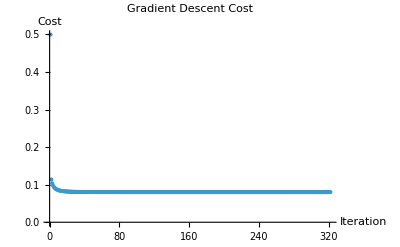

Gradient Descent Parameters: {169143.,27573.,27473.6,8125.89,13485.2,-3408.9,10510.4,2691.6,8962.57,1794.58,1422.89,494.421,3506.3,-1538.79,-2540.66}

Final Cost: 5.15358×10^8

LeastSquares Parameters: {169143.,27572.7,27474.2,8125.87,13485.9,-3409.04,10510.5,2690.8,8962.6,1794.48,1422.86,494.518,3506.31,-1538.82,-2540.66}

```mathematica
ClearAll[h,costJ,gradJ,thetaCurr,costs,alpha,step];

(*1. Use training data from Question 5*)
xGD=N[xTrainPoly];
yGD=N[yTrain];

{mGD,nGD}=Dimensions[xGD];

(*2. Normalize the data*)
polyMeans=Mean/@Transpose[xGD[[All,2;;]]];
polySDs=StandardDeviation/@Transpose[xGD[[All,2;;]]];
polySDs=polySDs/. 0.->1.;

x=Map[Prepend[(#-polyMeans)/polySDs,1]&,xGD[[All,2;;]]];

yMean=Mean[yGD];
ySD=StandardDeviation[yGD];
y=(yGD-yMean)/ySD;

(*3. Define hypothesis,cost and gradient*)
h[xInput_,t_]:=xInput.t;

costJ[t_]:=Total[(Map[h[#,t]&,x]-y)^2]/(2 mGD);

gradJ[t_]:=Transpose[x].(Map[h[#,t]&,x]-y)/mGD;

(*4. Set learning rate and starting parameters*)
alpha=1./Max[Eigenvalues[Transpose[x].x/mGD]];

thetaCurr=Table[0.,{i,1,nGD}];

Print["Learning Rate: ",alpha];
Print["Initial Theta: ",MatrixForm[thetaCurr]];

(*5. Apply Gradient Descent*)
costs={costJ[thetaCurr]};

step=0;
maxIterations=20000;

While[step<maxIterations,thetaCurr=thetaCurr-alpha gradJ[thetaCurr];
AppendTo[costs,costJ[thetaCurr]];
step++;
If[Abs[costs[[-1]]-costs[[-2]]]<10^-12,Break[]];];

(*6. Display iterations and cost graph*)
Print["Iterations: ",step];
Print["Final Normalized Cost: ",Last[costs]];

Print[ListPlot[costs,AxesLabel->{"Iteration","Cost"},PlotRange->All,PlotLabel->"Gradient Descent Cost"]];

(*7. Convert parameters back to Question 5 scale*)
coeffGD=ySD Rest[thetaCurr]/polySDs;

thetaGD=Prepend[coeffGD,yMean+ySD First[thetaCurr]-Total[coeffGD polyMeans]];

(*8. Display final results*)
Print["Gradient Descent Parameters: ",thetaGD];

Print["Final Cost: ",Total[(xGD.thetaGD-yGD)^2]/(2 mGD)];

Print["LeastSquares Parameters: ",thetaPoly];
```

Question 7

```mathematica
testData=Import["C:\\Users\\dylan\\Downloads\\archive\\test.csv"];

(*Get headers and data*)
testHeaders=First[testData];
testRows=Rest[testData];

(*Select the same features as Question 5*)
testColumns=Flatten[Position[testHeaders,#]]&/@featureNames;

xNew=N[testRows[[All,Flatten[testColumns]]]];

(*Normalize using Question 5 training values*)
xNewScaled=Map[(#-featureMeans)/featureSDs&,xNew];

(*Create polynomial features*)
xNewPoly=Map[Prepend[Join[#,#^2],1]&,xNewScaled];

(*Predict using Gradient Descent parameters*)
(*Define the regression hypothesis*)h[xInput_,t_]:=xInput.t;

(*Predict house prices*)
predictedPrices=Map[h[#,thetaGD]&,xNewPoly];

(*Get house IDs*)
idColumn=First[Flatten[Position[testHeaders,"Id"]]];
houseIDs=testRows[[All,idColumn]];

(*Display predictions*)
resultsQ7=Transpose[{houseIDs,predictedPrices}];

Print["Number of predictions: ",Length[predictedPrices]];

Grid[Prepend[Take[resultsQ7,20],{"House ID","Predicted Price"}],Frame->All]
```

Number of predictions: 1459

House ID | Predicted Price
1461 | 110456.
1462 | 162732.
1463 | 162493.
1464 | 175549.
1465 | 228399.
1466 | 168954.
1467 | 162894.
1468 | 161332.
1469 | 206362.
1470 | 117506.
1471 | 204402.
1472 | 110567.
1473 | 103765.
1474 | 157346.
1475 | 148237.
1476 | 359747.
1477 | 269438.
1478 | 323469.
1479 | 290720.
1480 | 400273.

Question 8

Metric | Linear Regression | Polynomial Regression
MSE | 2.38065×10^9 | 2.09377×10^9
RMSE | 48791.9 | 45757.8
R Squared | 0.595583 | 0.644316

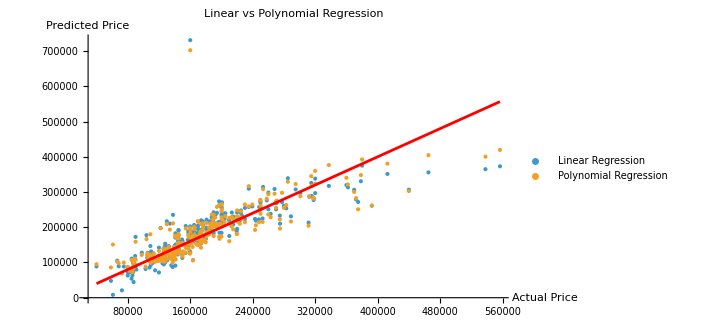

```mathematica
(*Question 8-Compare Linear and Non-Linear Regression*)(*Train linear regression on the same training data*)
xTrainLinear=Map[Prepend[#,1]&,xTrainScaled];
xTestLinear=Map[Prepend[#,1]&,xTestScaled];

thetaLinear=LeastSquares[xTrainLinear,yTrain];

(*Predict house prices*)
predictionsLinear=xTestLinear.thetaLinear;
predictionsPoly=xTestPoly.thetaPoly;

(*Calculate Linear Regression performance*)
mseLinear=Mean[(yTest-predictionsLinear)^2];
rmseLinear=Sqrt[mseLinear];

rSquaredLinear=1-Total[(yTest-predictionsLinear)^2]/Total[(yTest-Mean[yTest])^2];

(*Calculate Polynomial Regression performance*)
msePoly=Mean[(yTest-predictionsPoly)^2];
rmsePoly=Sqrt[msePoly];

rSquaredPoly=1-Total[(yTest-predictionsPoly)^2]/Total[(yTest-Mean[yTest])^2];

(*Display results*)
Grid[{{"Metric","Linear Regression","Polynomial Regression"},{"MSE",mseLinear,msePoly},{"RMSE",rmseLinear,rmsePoly},{"R Squared",rSquaredLinear,rSquaredPoly}},Frame->All]

(*Compare actual and predicted prices*)
Show[ListPlot[{Transpose[{yTest,predictionsLinear}],Transpose[{yTest,predictionsPoly}]},PlotLegends->{"Linear Regression","Polynomial Regression"},AxesLabel->{"Actual Price","Predicted Price"},PlotLabel->"Linear vs Polynomial Regression",PlotRange->All],Plot[x,{x,Min[yTest],Max[yTest]},PlotStyle->{Red}]]
```